```mathematica
Quit[];
```

This notebook is used to demonstrate how to use the package BaikovLetter.wl (it depends on previous package BaikovAll.wl). Several simple examples will be used to show this. You can put the package under  the same directory with this notebook.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["BaikovAll.wl"];
```

x::shdw: Symbol x appears in multiple contexts {Baikov`,Global`}; definitions in context Baikov` may shadow or be shadowed by other definitions.

y::shdw: Symbol y appears in multiple contexts {Baikov`,Global`}; definitions in context Baikov` may shadow or be shadowed by other definitions.

ϵ::shdw: Symbol ϵ appears in multiple contexts {Baikov`,Global`}; definitions in context Baikov` may shadow or be shadowed by other definitions.

```mathematica
(*specifying the relevant path for Singular. $SingularFilePath is the path where we store the input files for Singular. $SingularPath is the path of the excutable file of Singular, it is usually under bin/*)
```

```mathematica
$SingularFilePath="/Users/windfolgen/GitRepos/Notes/Singular/dimension/";
$SingularPath="/opt/homebrew/bin/Singular";
```

```mathematica
Get["BaikovLetter.wl"];
```

## Some basic information

To be familiar with the operation performed below, we introduce some basic functions and their usage:
PD[k,p,-msq]: It defines the inverse propagator. First argument is loop momentum, second argument is external momentum and the last one is a constant term. PD[k,p,-msq]=(k+p)^2-msq.
LPD[k,p,-msq]: It defines the linear inverse propagator. First argument is loop momentum, second argument is external momentum and the last one is a constant term. LPD[k,p,-msq]=k.p-msq.
BaikovTrans[propagators list]: it gives the transformation from scalar products to Baikov variables x_i which are those inverse propagators.
BaikovRep[propagators list,loop momenta list,  independent external momenta list]: it gives the standard Baikov representations for a given family defined by propagators list.
AllSectorBaikovMat[standard rep., replacement rule, Exc->{__}]: it generates all the Baikov representations for a given integral family by integrating Baikov variables out from standard representation one by one. replacement rule is a replacement rule from scalar products to Baikov variables and Mandelstam variables. Exc->{} is an option. The Baikov variables in this list will not be integrated out all the time. Note here that, when one sector is identified to be zero sector, we won’t continue the integrate-out operation any more and we don’t remove those reducible sectors and symmetric sectors.
ReformRep[result]: it extracts all the Gram determinants from the output of AllSectorBaikovMat[_] except those zero sectors.

Many other functions can be looked up by ?Baikov`*

## One-loop hexagon

A one-loop example. One-loop symbol letters are well studied.

### configurations

```mathematica
dlist={PD[k1,0,0],PD[k1,p1,0],PD[k1,p1+p2,0],PD[k1,p1+p2+p3,0],PD[k1,p1+p2+p3+p4,0],PD[k1,p1+p2+p3+p4+p5,0]};
kinerep={p1·p1->0,p2·p2->0,p3·p3->0,p4·p4->0,p5·p5->0,p6·p6->0,p1·p2->s12/2,p1·p3->1/2 (-s12+s123-s23),p1·p4->1/2 (-s123+s23-s234+s56),p1·p5->1/2 (s234-s56-s61),p1·p6->s61/2,p2·p3->s23/2,p2·p4->1/2 (-s23+s234-s34),p2·p5->1/2 (-s234+s34-s345+s61),p2·p6->1/2 (-s12+s345-s61),p3·p4->s34/2,p3·p5->1/2 (-s34+s345-s45),p3·p6->1/2 (s12-s123-s345+s45),p4·p5->s45/2,p4·p6->1/2 (s123-s45-s56),p5·p6->s56/2};
rep=BaikovTrans[dlist/.kinerep];
krep=Join[rep[[2]],kinerep];
```

```mathematica
intStd=BaikovRep[dlist,{k1},{p1,p2,p3,p4,p5}];
```

```mathematica
intStd
```

{{{G[{p1,p2,p3,p4,p5},{p1,p2,p3,p4,p5}],1/2 (2+2 ϵ)},{G[{k1,p1,p2,p3,p4,p5},{k1,p1,p2,p3,p4,p5}],1/2 (-3-2 ϵ)}},1/(32 π^(5/2) Gamma[1/2 (-1-2 ϵ)])}

```mathematica
resultmat=AllSectorBaikovMat[intStd,krep,Exc->{}(*,deBug->True*)];
```

```mathematica
reformmat=ReformRep[resultmat];
```

### all symbol letters

Analyze  the pole structure in this family

```mathematica
polestructure=PolesAnalyze[resultmat,{1,2,3,4,5,6},krep,6];
```

totally 51 sectors need to be analyzed!

```mathematica
rllist=AllRationalLetters[polestructure]//SortBy[#,LeafCount]&
```

{s12,s123,s23,s234,s34,s345,s45,s56,s61,s12-s123,s123-s23,s23-s234,s234-s34,s12-s345,s34-s345,s123-s45,s345-s45,s123-s56,s234-s56,s234-s61,s345-s61,s12-s123+s23,s23-s234+s34,s34-s345+s45,s12-s345+s61,s123 s345-s12 s45,s123-s45-s56,s123 s234-s23 s56,s234-s56-s61,s234 s345-s34 s61,s12-s123-s345+s45,s123-s23+s234-s56,s234-s34+s345-s61,s12 s234+s234^2-s234 s34-s234 s56+s34 s56,s12 s34-s12 s345-s34 s345+s345^2+s345 s56,s123^2-s123 s23-s123 s45+s23 s45+s123 s61,s23 s345+s345^2-s345 s45-s345 s61+s45 s61,s12 s123-s123^2-s123 s34-s12 s56+s123 s56,s23 s234-s234^2-s234 s45-s23 s61+s234 s61,s12^2-2 s12 s34+s34^2-2 s12 s56-2 s34 s56+s56^2,s23^2-2 s23 s45+s45^2-2 s23 s61-2 s45 s61+s61^2,s123^2 s234^2 s345^2-2 s12 s123 s234^2 s345 s45+s12^2 s234^2 s45^2-2 s123 s23 s234 s345^2 s56+2 s12 s23 s234 s345 s45 s56+s23^2 s345^2 s56^2-2 s123^2 s234 s34 s345 s61+2 s12 s123 s234 s34 s45 s61+2 s123 s23 s34 s345 s56 s61-4 s12 s23 s34 s45 s56 s61+s123^2 s34^2 s61^2,s12^2 s23^2-2 s12^2 s23 s234+2 s12 s123 s23 s234+s12^2 s234^2-2 s12 s123 s234^2+s123^2 s234^2+2 s12 s123 s23 s34-2 s12 s23^2 s34+2 s12 s123 s234 s34-2 s123^2 s234 s34+2 s12 s23 s234 s34+2 s123 s23 s234 s34+s123^2 s34^2-2 s123 s23 s34^2+s23^2 s34^2-2 s12 s23^2 s56+2 s12 s23 s234 s56-2 s123 s23 s234 s56-4 s12 s23 s34 s56+2 s123 s23 s34 s56-2 s23^2 s34 s56+s23^2 s56^2,s123^2 s34^2-2 s123^2 s34 s345+s123^2 s345^2+2 s12 s123 s34 s45-2 s123 s34^2 s45-2 s12 s123 s345 s45+2 s123 s34 s345 s45+s12^2 s45^2-2 s12 s34 s45^2+s34^2 s45^2+2 s123 s34 s345 s56-2 s123 s345^2 s56-4 s12 s34 s45 s56+2 s123 s34 s45 s56+2 s12 s345 s45 s56+2 s123 s345 s45 s56+2 s34 s345 s45 s56-2 s12 s45^2 s56-2 s34 s45^2 s56+s345^2 s56^2-2 s345 s45 s56^2+s45^2 s56^2,s12^2 s23^2+2 s12 s123 s23 s345-2 s12 s23^2 s345+s123^2 s345^2-2 s123 s23 s345^2+s23^2 s345^2-2 s12^2 s23 s45-2 s12 s123 s345 s45+2 s12 s23 s345 s45+s12^2 s45^2-2 s12^2 s23 s61+2 s12 s123 s23 s61+2 s12 s123 s345 s61-2 s123^2 s345 s61+2 s12 s23 s345 s61+2 s123 s23 s345 s61-2 s12^2 s45 s61+2 s12 s123 s45 s61-4 s12 s23 s45 s61+s12^2 s61^2-2 s12 s123 s61^2+s123^2 s61^2,s23^2 s34^2-2 s23^2 s34 s345+2 s23 s234 s34 s345+s23^2 s345^2-2 s23 s234 s345^2+s234^2 s345^2+2 s23 s234 s34 s45-2 s23 s34^2 s45+2 s23 s234 s345 s45-2 s234^2 s345 s45+2 s23 s34 s345 s45+2 s234 s34 s345 s45+s234^2 s45^2-2 s234 s34 s45^2+s34^2 s45^2-2 s23 s34^2 s61+2 s23 s34 s345 s61-2 s234 s34 s345 s61-4 s23 s34 s45 s61+2 s234 s34 s45 s61-2 s34^2 s45 s61+s34^2 s61^2,s123^2 s234^2-2 s123 s234^2 s45+s234^2 s45^2-2 s123 s23 s234 s56+2 s123 s234 s45 s56+2 s23 s234 s45 s56-2 s234 s45^2 s56+s23^2 s56^2-2 s23 s45 s56^2+s45^2 s56^2-2 s123^2 s234 s61+2 s123 s234 s45 s61+2 s123 s23 s56 s61+2 s123 s234 s56 s61+2 s123 s45 s56 s61-4 s23 s45 s56 s61+2 s234 s45 s56 s61-2 s23 s56^2 s61-2 s45 s56^2 s61+s123^2 s61^2-2 s123 s56 s61^2+s56^2 s61^2,s12^2 s234^2-2 s12 s234^2 s345+s234^2 s345^2+2 s12 s234 s345 s56-2 s234 s345^2 s56+s345^2 s56^2-2 s12^2 s234 s61+2 s12 s234 s34 s61+2 s12 s234 s345 s61-2 s234 s34 s345 s61+2 s12 s234 s56 s61-4 s12 s34 s56 s61+2 s12 s345 s56 s61+2 s234 s345 s56 s61+2 s34 s345 s56 s61-2 s345 s56^2 s61+s12^2 s61^2-2 s12 s34 s61^2+s34^2 s61^2-2 s12 s56 s61^2-2 s34 s56 s61^2+s56^2 s61^2,s12 s123 s23 s234 s34-s12 s123 s23 s234 s345+s12 s123 s234^2 s345-s123^2 s234^2 s345+s123^2 s234 s34 s345-s123 s23 s234 s34 s345-s123^2 s234 s345^2+s123 s23 s234 s345^2-s123 s234^2 s345^2+s12^2 s23 s234 s45-s12^2 s234^2 s45+s12 s123 s234^2 s45-s12 s123 s234 s34 s45-s12 s23 s234 s34 s45+2 s12 s123 s234 s345 s45-s12 s23 s234 s345 s45+s12 s234^2 s345 s45+s123 s234^2 s345 s45-s123 s234 s34 s345 s45+s23 s234 s34 s345 s45-s12^2 s234 s45^2-s12 s234^2 s45^2+s12 s234 s34 s45^2-s12 s23^2 s34 s56+s12 s23^2 s345 s56-s12 s23 s234 s345 s56+2 s123 s23 s234 s345 s56-s123 s23 s34 s345 s56+s23^2 s34 s345 s56+s123 s23 s345^2 s56-s23^2 s345^2 s56+s123 s234 s345^2 s56+s23 s234 s345^2 s56-s12 s23 s234 s45 s56+2 s12 s23 s34 s45 s56-s12 s23 s345 s45 s56-s12 s234 s345 s45 s56-s123 s234 s345 s45 s56-s23 s234 s345 s45 s56+s123 s34 s345 s45 s56-s23 s34 s345 s45 s56+s12 s234 s45^2 s56-s12 s34 s45^2 s56-s23^2 s345 s56^2-s23 s345^2 s56^2+s23 s345 s45 s56^2-s12 s123 s23 s34 s61-s12 s123 s234 s34 s61+s123^2 s234 s34 s61-s123^2 s34^2 s61+s123 s23 s34^2 s61+s12 s123 s23 s345 s61-s12 s123 s234 s345 s61+s123^2 s234 s345 s61+s123^2 s34 s345 s61-s123 s23 s34 s345 s61+2 s123 s234 s34 s345 s61-s12^2 s23 s45 s61+s12^2 s234 s45 s61-s12 s123 s234 s45 s61-s12 s123 s34 s45 s61+2 s12 s23 s34 s45 s61-s12 s234 s34 s45 s61-s123 s234 s34 s45 s61+s123 s34^2 s45 s61-s23 s34^2 s45 s61+2 s12 s23 s34 s56 s61-s123 s23 s34 s56 s61-s12 s23 s345 s56 s61-s123 s23 s345 s56 s61+s12 s234 s345 s56 s61-s123 s234 s345 s56 s61-s123 s34 s345 s56 s61-s23 s34 s345 s56 s61+2 s12 s23 s45 s56 s61-s12 s234 s45 s56 s61+s123 s234 s45 s56 s61+2 s12 s34 s45 s56 s61-s123 s34 s45 s56 s61+2 s23 s34 s45 s56 s61+s23 s345 s56^2 s61-s23 s45 s56^2 s61+s12 s123 s34 s61^2-s123^2 s34 s61^2-s123 s34^2 s61^2-s12 s34 s56 s61^2+s123 s34 s56 s61^2}

```mathematica
rllist//Length
```

49

Note that in above list, Δ_6/(G(p1,p2,p3,p4,p5)) is split into two terms Δ_6 and G(p1,p2,p3,p4,p5), so the number above is one more than that in 2210.13505

```mathematica
testalg=ExtractAlgLetter[resultmat,{1,2,3,4,5,6},6,KineVar->{p1,p2,p3,p4,p5},OneLoop->True];
```

totally 51 sectors need to be analyzed!

```mathematica
poles=ExtractPoleInfo[polestructure,6];
```

All possible square roots when constructing UT basis are needed as an input.

```mathematica
permsqlist=ExtractSquareRoots[polestructure](*the possible square roots in UT basis*)
```

{s123^2 s234^2 s345^2-2 s12 s123 s234^2 s345 s45+s12^2 s234^2 s45^2-2 s123 s23 s234 s345^2 s56+2 s12 s23 s234 s345 s45 s56+s23^2 s345^2 s56^2-2 s123^2 s234 s34 s345 s61+2 s12 s123 s234 s34 s45 s61+2 s123 s23 s34 s345 s56 s61-4 s12 s23 s34 s45 s56 s61+s123^2 s34^2 s61^2,s23^2 s34^2-2 s23^2 s34 s345+2 s23 s234 s34 s345+s23^2 s345^2-2 s23 s234 s345^2+s234^2 s345^2+2 s23 s234 s34 s45-2 s23 s34^2 s45+2 s23 s234 s345 s45-2 s234^2 s345 s45+2 s23 s34 s345 s45+2 s234 s34 s345 s45+s234^2 s45^2-2 s234 s34 s45^2+s34^2 s45^2-2 s23 s34^2 s61+2 s23 s34 s345 s61-2 s234 s34 s345 s61-4 s23 s34 s45 s61+2 s234 s34 s45 s61-2 s34^2 s45 s61+s34^2 s61^2,s123^2 s34^2-2 s123^2 s34 s345+s123^2 s345^2+2 s12 s123 s34 s45-2 s123 s34^2 s45-2 s12 s123 s345 s45+2 s123 s34 s345 s45+s12^2 s45^2-2 s12 s34 s45^2+s34^2 s45^2+2 s123 s34 s345 s56-2 s123 s345^2 s56-4 s12 s34 s45 s56+2 s123 s34 s45 s56+2 s12 s345 s45 s56+2 s123 s345 s45 s56+2 s34 s345 s45 s56-2 s12 s45^2 s56-2 s34 s45^2 s56+s345^2 s56^2-2 s345 s45 s56^2+s45^2 s56^2,s123^2 s234^2-2 s123 s234^2 s45+s234^2 s45^2-2 s123 s23 s234 s56+2 s123 s234 s45 s56+2 s23 s234 s45 s56-2 s234 s45^2 s56+s23^2 s56^2-2 s23 s45 s56^2+s45^2 s56^2-2 s123^2 s234 s61+2 s123 s234 s45 s61+2 s123 s23 s56 s61+2 s123 s234 s56 s61+2 s123 s45 s56 s61-4 s23 s45 s56 s61+2 s234 s45 s56 s61-2 s23 s56^2 s61-2 s45 s56^2 s61+s123^2 s61^2-2 s123 s56 s61^2+s56^2 s61^2,s12^2 s234^2-2 s12 s234^2 s345+s234^2 s345^2+2 s12 s234 s345 s56-2 s234 s345^2 s56+s345^2 s56^2-2 s12^2 s234 s61+2 s12 s234 s34 s61+2 s12 s234 s345 s61-2 s234 s34 s345 s61+2 s12 s234 s56 s61-4 s12 s34 s56 s61+2 s12 s345 s56 s61+2 s234 s345 s56 s61+2 s34 s345 s56 s61-2 s345 s56^2 s61+s12^2 s61^2-2 s12 s34 s61^2+s34^2 s61^2-2 s12 s56 s61^2-2 s34 s56 s61^2+s56^2 s61^2,s12^2 s23^2+2 s12 s123 s23 s345-2 s12 s23^2 s345+s123^2 s345^2-2 s123 s23 s345^2+s23^2 s345^2-2 s12^2 s23 s45-2 s12 s123 s345 s45+2 s12 s23 s345 s45+s12^2 s45^2-2 s12^2 s23 s61+2 s12 s123 s23 s61+2 s12 s123 s345 s61-2 s123^2 s345 s61+2 s12 s23 s345 s61+2 s123 s23 s345 s61-2 s12^2 s45 s61+2 s12 s123 s45 s61-4 s12 s23 s45 s61+s12^2 s61^2-2 s12 s123 s61^2+s123^2 s61^2,s12^2 s23^2-2 s12^2 s23 s234+2 s12 s123 s23 s234+s12^2 s234^2-2 s12 s123 s234^2+s123^2 s234^2+2 s12 s123 s23 s34-2 s12 s23^2 s34+2 s12 s123 s234 s34-2 s123^2 s234 s34+2 s12 s23 s234 s34+2 s123 s23 s234 s34+s123^2 s34^2-2 s123 s23 s34^2+s23^2 s34^2-2 s12 s23^2 s56+2 s12 s23 s234 s56-2 s123 s23 s234 s56-4 s12 s23 s34 s56+2 s123 s23 s34 s56-2 s23^2 s34 s56+s23^2 s56^2,s23^2-2 s23 s45+s45^2-2 s23 s61-2 s45 s61+s61^2,s12^2-2 s12 s34+s34^2-2 s12 s56-2 s34 s56+s56^2}

Generate all algebraic letters

```mathematica
(*above are all input, here we set a different ansatz for one-loop case by KinePath->True and LoopPath->False*)
```

```mathematica
testresult=AllAlgLetters[poles,testalg,reformmat,krep,PermSq->permsqlist];
```

totally 51 sectors need to be analyzed

analyzing first type construction...

session time: 11.5739

Substituting poles into expressions...

session time: 16.26312

analyzing second type construction...

session time: 21.02624

```mathematica
LetterInfo[s12^2-2 s12 s34+s34^2-2 s12 s56-2 s34 s56+s56^2,testresult,polestructure]
```

This letter can be generated from following sectors: {{1,3,5}}

The corresponding path is: {{{x_6,x_4,x_2}}}

To see more information, search the following position of output of PolesAnalyze[]: {37}

```mathematica
LetterInfo[s12^2 s23^2-2 s12^2 s23 s234+2 s12 s123 s23 s234+s12^2 s234^2-2 s12 s123 s234^2+s123^2 s234^2+2 s12 s123 s23 s34-2 s12 s23^2 s34+2 s12 s123 s234 s34-2 s123^2 s234 s34+2 s12 s23 s234 s34+2 s123 s23 s234 s34+s123^2 s34^2-2 s123 s23 s34^2+s23^2 s34^2-2 s12 s23^2 s56+2 s12 s23 s234 s56-2 s123 s23 s234 s56-4 s12 s23 s34 s56+2 s123 s23 s34 s56-2 s23^2 s34 s56+s23^2 s56^2,testresult,polestructure]
```

This letter can be generated from following sectors: {{1,2,3,4,5}}

The corresponding path is: {{{x_6}}}

To see more information, search the following position of output of PolesAnalyze[]: {7}

```mathematica
algcand=Cases[testresult,Log[_?(FreeQ[#,G]&)],Infinity]//DeleteCases[#,_?(FreeQ[#,Power[_,1/2]]&)]&//DeleteSameAlgLetter;
```

The warning above can be omitted. Under some special point, some expression will be 0 in the denominator with the numeric values we take in the program  but they are not 0 in general.

```mathematica
algselect=SelectAlgLetter[algcand,rllist];
```

```mathematica
algselect//Length
```

62

```mathematica
algind=GetAllAlgIndepLetter[algselect];
```

totally 21 different square roots

```mathematica
algind//Flatten//Length
```

55

```mathematica
Length/@algind
```

{1,1,1,1,1,1,5,5,5,3,5,5,5,5,1,1,1,5,1,1,1}

Compared to 2210.13505, we can find above is exactly all the algebraic letters set. For example, the following is W89

```mathematica
algind[[-3]](*W89*)
```

{Log[-((s12^2 s23-s12^2 s234+s12 s123 s234+s12 s123 s34-2 s12 s23 s34+s12 s234 s34+s123 s234 s34-s123 s34^2+s23 s34^2-2 s12 s23 s56+s12 s234 s56-s123 s234 s56-2 s12 s34 s56+s123 s34 s56-2 s23 s34 s56+s23 s56^2+√((s12^2-2 s12 s34+s34^2-2 s12 s56-2 s34 s56+s56^2) (s12^2 s23^2-2 s12^2 s23 s234+2 s12 s123 s23 s234+s12^2 s234^2-2 s12 s123 s234^2+s123^2 s234^2+2 s12 s123 s23 s34-2 s12 s23^2 s34+2 s12 s123 s234 s34-2 s123^2 s234 s34+2 s12 s23 s234 s34+2 s123 s23 s234 s34+s123^2 s34^2-2 s123 s23 s34^2+s23^2 s34^2-2 s12 s23^2 s56+2 s12 s23 s234 s56-2 s123 s23 s234 s56-4 s12 s23 s34 s56+2 s123 s23 s34 s56-2 s23^2 s34 s56+s23^2 s56^2)))/(-s12^2 s23+s12^2 s234-s12 s123 s234-s12 s123 s34+2 s12 s23 s34-s12 s234 s34-s123 s234 s34+s123 s34^2-s23 s34^2+2 s12 s23 s56-s12 s234 s56+s123 s234 s56+2 s12 s34 s56-s123 s34 s56+2 s23 s34 s56-s23 s56^2+√((s12^2-2 s12 s34+s34^2-2 s12 s56-2 s34 s56+s56^2) (s12^2 s23^2-2 s12^2 s23 s234+2 s12 s123 s23 s234+s12^2 s234^2-2 s12 s123 s234^2+s123^2 s234^2+2 s12 s123 s23 s34-2 s12 s23^2 s34+2 s12 s123 s234 s34-2 s123^2 s234 s34+2 s12 s23 s234 s34+2 s123 s23 s234 s34+s123^2 s34^2-2 s123 s23 s34^2+s23^2 s34^2-2 s12 s23^2 s56+2 s12 s23 s234 s56-2 s123 s23 s234 s56-4 s12 s23 s34 s56+2 s123 s23 s34 s56-2 s23^2 s34 s56+s23^2 s56^2))))]}

```mathematica
R3=s12^2*(s23-s234)+s12*(-2s23*(s34+s56)+s34*(-2s56+s123)+(s34+s56+s123)*s234)+(s34-s56)*(s23*(s34-s56)+s123*(-s34+s234));
```

```mathematica
R3-(s12^2 s23-s12^2 s234+s12 s123 s234+s12 s123 s34-2 s12 s23 s34+s12 s234 s34+s123 s234 s34-s123 s34^2+s23 s34^2-2 s12 s23 s56+s12 s234 s56-s123 s234 s56-2 s12 s34 s56+s123 s34 s56-2 s23 s34 s56+s23 s56^2)//Factor
```

0

## Sunrise with two different masses

### configurations

```mathematica
dlist={PD[k1,0,-m12],PD[k1-k2,0,0],PD[k2,-p,-m22],PD[k2,0,0],PD[k1,-p,0]};
kinerep={SProd[p,p]->s};
krep=Join[BaikovTrans[dlist/.kinerep][[2]],kinerep];
```

```mathematica
gmat=GramMat[{k1,k2,p},{k1,k2,p},krep];
gmat//MatrixForm
```

(m12+x_1 | 1/2 (m12+x_1-x_2+x_4) | 1/2 (m12+s+x_1-x_5)
1/2 (m12+x_1-x_2+x_4) | x_4 | 1/2 (-m22+s-x_3+x_4)
1/2 (m12+s+x_1-x_5) | 1/2 (-m22+s-x_3+x_4) | s)

```mathematica
(*check the distribution of Baikov variables in a Gram matrix. We hope every Baikov variable only appear in one column and one row. This can be usually achieved in planar Feynman integrals by proper definition of ISPs.*)
```

```mathematica
CheckPosition[Position[gmat,#][[All,{1,2}]]&/@Table[Subscript[x,i],{i,1,5}]]
```

True: all in one column and one row; False: not in the preferred configuration

{True,True,True,True,True}

```mathematica
krep
```

{k1·k1→m12+x_1,k1·k2→1/2 (m12+x_1-x_2+x_4),k2·k2→x_4,k2·p→1/2 (-m22+s-x_3+x_4),k1·p→1/2 (m12+s+x_1-x_5),p·p→s}

```mathematica
stdrep=BaikovRep[dlist,{k1,k2},{p}]
```

{{{G[{p},{p}],1/2 (-2+2 ϵ)},{G[{k1,k2,p},{k1,k2,p}],-ϵ}},1/(8 π^(3/2) Gamma[1/2 (2-2 ϵ)] Gamma[1/2 (3-2 ϵ)])}

```mathematica
resultmat=AllSectorBaikovMat[stdrep,krep,Exc->{}];
```

```mathematica
reformmat=ReformRep[resultmat];
```

### all symbol letters

Analyze  the pole structure in this family

```mathematica
polestructure=PolesAnalyze[resultmat,{1,2,3},krep,5]
```

totally 2 sectors need to be analyzed!

{{{{{{x_4→0},{x_4→m12},{x_4→∞}},{s,m12,m22-s,-m12^2+2 m12 m22-m22^2+2 m12 s+2 m22 s-s^2},{-1,-m12^2+2 m12 m22-m22^2+2 m12 s+2 m22 s-s^2},{x_5}},{{{x_5→0},{x_5→m22},{x_5→∞}},{s,m22,m12-s,-m12^2+2 m12 m22-m22^2+2 m12 s+2 m22 s-s^2},{-1,-m12^2+2 m12 m22-m22^2+2 m12 s+2 m22 s-s^2},{x_4}}},{s,m12^2-2 m12 m22+m22^2-2 m12 s-2 m22 s+s^2},{m12,m22,s,m12^2-2 m12 m22+m22^2-2 m12 s-2 m22 s+s^2},{-1,-m12^2+2 m12 m22-m22^2+2 m12 s+2 m22 s-s^2},{1,2,3}},{{{{},{m12,m22},1,{x_5,x_4,x_2}}},{m12,m22},{m12,m22},{1},{1,3}}}

```mathematica
rllist=AllRationalLetters[polestructure]//SortBy[#,LeafCount]&
```

{m12,m22,s,m12^2-2 m12 m22+m22^2-2 m12 s-2 m22 s+s^2}

The rational letters will be more than that appear in CDE. This is a common feature of families with massive propagators as we will see in the next example: inner massive double box.

```mathematica
testalg=ExtractAlgLetter[resultmat,{1,2,3},5];
```

totally 2 sectors need to be analyzed!

```mathematica
poles=ExtractPoleInfo[polestructure,5];
```

original total 6 poles

final total 6 poles

maximal clique: 2; # of cliques: 9

```mathematica
poles
```

{{{{x_1→0,x_2→0,x_3→0},{x_4→0}},{{x_1→0,x_2→0,x_3→0},{x_4→m12}},{{x_1→0,x_2→0,x_3→0},{x_4→∞}},{{x_1→0,x_2→0,x_3→0},{x_5→0}},{{x_1→0,x_2→0,x_3→0},{x_5→m22}},{{x_1→0,x_2→0,x_3→0},{x_5→∞}}},{1<->4,1<->5,1<->6,2<->4,2<->5,2<->6,3<->4,3<->5,3<->6},{{1,4},{1,5},{1,6},{4,2},{5,2},{6,2},{4,3},{5,3},{6,3}}}

All possible square roots when constructing UT basis. There is only one in this example

```mathematica
permsqlist=ExtractSquareRoots[polestructure]
```

{m12^2-2 m12 m22+m22^2-2 m12 s-2 m22 s+s^2}

Generate all algebraic letters

```mathematica
testresult=AllAlgLetters[poles,testalg,reformmat,krep,PermSq->permsqlist];
```

totally 2 sectors need to be analyzed

analyzing first type construction...

session time: 0.29724

Substituting poles into expressions...

session time: 0.41616

analyzing second type construction...

session time: 0.48168

```mathematica
algcand=Cases[testresult,Log[_?(FreeQ[#,G]&)],Infinity]//DeleteCases[#,_?(FreeQ[#,Power[_,1/2]]&)]&//DeleteSameAlgLetter;
```

```mathematica
algselect=SelectAlgLetter[algcand,rllist];
```

```mathematica
algselect//Length
```

6

```mathematica
algind=GetAllAlgIndepLetter[algselect];
```

totally 1 different square roots

```mathematica
algind
```

{{Log[-(m12+m22-s+√(m12^2-2 m12 m22+m22^2-2 m12 s-2 m22 s+s^2))/(-m12-m22+s+√(m12^2-2 m12 m22+m22^2-2 m12 s-2 m22 s+s^2))],Log[-(m12-m22+s+√(m12^2-2 m12 m22+m22^2-2 m12 s-2 m22 s+s^2))/(-m12+m22-s+√(m12^2-2 m12 m22+m22^2-2 m12 s-2 m22 s+s^2))]}}

Above algebraic letters are the only two independent algebraic letters in this family

```mathematica
(*the following function can be used to find relations among letters with the same square root*)
```

```mathematica
FindLetterLinearRelation[{Log[-(-m12^2+m12 m22+2 m12 s+m22 s-s^2+(m12-s) √(m12^2-2 m12 m22+m22^2-2 m12 s-2 m22 s+s^2))/(m12^2-m12 m22-2 m12 s-m22 s+s^2+(m12-s) √(m12^2-2 m12 m22+m22^2-2 m12 s-2 m22 s+s^2))],Log[-(m12 m22-m22^2+m12 s+2 m22 s-s^2+(m22-s) √(m12^2-2 m12 m22+m22^2-2 m12 s-2 m22 s+s^2))/(-m12 m22+m22^2-m12 s-2 m22 s+s^2+(m22-s) √(m12^2-2 m12 m22+m22^2-2 m12 s-2 m22 s+s^2))]},Log[(m12+s-m22-√(m12^2-2 m12 m22+m22^2-2 m12 s-2 m22 s+s^2))/(m12+s-m22+√(m12^2-2 m12 m22+m22^2-2 m12 s-2 m22 s+s^2))]]
```

{{1,-2,-3}}

```mathematica
LetterInfo[m12^2-2 m12 m22+m22^2-2 m12 s-2 m22 s+s^2,testresult,polestructure]
```

This letter can be generated from following sectors: {{1,2,3}}

The corresponding path is: {{{x_5},{x_4}}}

To see more information, search the following position of output of PolesAnalyze[]: {1}

We can see that this square root exactly comes from above sectors from the UT basis

```mathematica
LetterInfo[Log[-(m12+m22-s+√(m12^2-2 m12 m22+m22^2-2 m12 s-2 m22 s+s^2))/(-m12-m22+s+√(m12^2-2 m12 m22+m22^2-2 m12 s-2 m22 s+s^2))],testresult,polestructure]
```

This letter comes from the first type construction.

It can come from the following gram and poles: {{Log[(G[{k1},{k1-p}]+√(-G[{},{}] G[{k1,k1-p},{k1,k1-p}]))/(G[{k1},{k1-p}]-√(-G[{},{}] G[{k1,k1-p},{k1,k1-p}]))],{{x_1→0,x_2→0,x_3→0,x_4→0},{x_5→m22}}},{Log[(G[{k2-p},{k2}]+√(-G[{},{}] G[{k2,k2-p},{k2,k2-p}]))/(G[{k2-p},{k2}]-√(-G[{},{}] G[{k2,k2-p},{k2,k2-p}]))],{{x_1→0,x_2→0,x_3→0,x_5→0},{x_4→m12}}}}

```mathematica
LetterInfo[Log[-(m12-m22+s+√(m12^2-2 m12 m22+m22^2-2 m12 s-2 m22 s+s^2))/(-m12+m22-s+√(m12^2-2 m12 m22+m22^2-2 m12 s-2 m22 s+s^2))],testresult,polestructure]
```

This letter comes from the first type construction.

It can come from the following gram and poles: {{Log[(G[{k2},{p}]+√(-G[{},{}] G[{k2,p},{k2,p}]))/(G[{k2},{p}]-√(-G[{},{}] G[{k2,p},{k2,p}]))],{{x_1→0,x_2→0,x_3→0,x_5→0},{x_4→m12}}},{Log[(G[{p},{k2}]+√(-G[{},{}] G[{k2,p},{k2,p}]))/(G[{p},{k2}]-√(-G[{},{}] G[{k2,p},{k2,p}]))],{{x_1→0,x_2→0,x_3→0,x_5→0},{x_4→m12}}},{Log[(G[{k1},{p}]+√(-G[{},{}] G[{k1,p},{k1,p}]))/(G[{k1},{p}]-√(-G[{},{}] G[{k1,p},{k1,p}]))],{{x_1→0,x_2→0,x_3→0,x_4→0},{x_5→m22}}}}

```mathematica
ApplyPoleToLetter[{{Subscript[x, 1]->0,Subscript[x, 2]->0,Subscript[x, 3]->0},{Subscript[x, 4]->m12,Subscript[x, 5]->m22}},Log[(G[{k1},{p}]+√(-G[{},{}] G[{k1,p},{k1,p}]))/(G[{k1},{p}]-√(-G[{},{}] G[{k1,p},{k1,p}]))],krep]
```

Log[-(m12-m22+s+√(m12^2-2 m12 m22+m22^2-2 m12 s-2 m22 s+s^2))/(-m12+m22-s+√(m12^2-2 m12 m22+m22^2-2 m12 s-2 m22 s+s^2))]

```mathematica
ApplyPoleToLetter[{{Subscript[x, 1]->0,Subscript[x, 2]->0,Subscript[x, 3]->0},{Subscript[x, 4]->m12,Subscript[x, 5]->m22}},Log[(G[{k1},{k1-p}]+√(-G[{},{}] G[{k1,k1-p},{k1,k1-p}]))/(G[{k1},{k1-p}]-√(-G[{},{}] G[{k1,k1-p},{k1,k1-p}]))],krep]
```

Log[-(m12+m22-s+√(m12^2-2 m12 m22+m22^2-2 m12 s-2 m22 s+s^2))/(-m12-m22+s+√(m12^2-2 m12 m22+m22^2-2 m12 s-2 m22 s+s^2))]

## Inner massive double box

### configurations

```mathematica
-Graphics-(*2202.08127*)
```

```mathematica
dlist={PD[k1,0,0],PD[k1,-p1,0],PD[k1,-p1-p2,0],PD[k1-k2,0,-m2],PD[k2,-p1-p2,-m2],PD[k2,-p1-p2-p3,-m2],PD[k2,0,-m2],PD[k2,-p1,-m2],PD[k1,-p1-p2-p3,0]};
kinerep={SProd[p1,p1]->0,SProd[p2,p2]->0,SProd[p3,p3]->0,SProd[p1,p2]->s/2,SProd[p2,p3]->t/2,SProd[p1,p3]->-(s+t)/2};
krep=Join[BaikovTrans[dlist/.kinerep][[2]],kinerep];
```

```mathematica
krep
```

{k1·k1→x_1,k1·p1→1/2 (x_1-x_2),k1·p2→1/2 (s+x_2-x_3),k1·k2→1/2 (x_1-x_4+x_7),k2·k2→m2+x_7,k2·p1→1/2 (x_7-x_8),k2·p2→1/2 (s-x_5+x_8),k2·p3→1/2 (-s+x_5-x_6),k1·p3→1/2 (-s+x_3-x_9),p1·p1→0,p2·p2→0,p3·p3→0,p1·p2→s/2,p2·p3→t/2,p1·p3→1/2 (-s-t)}

```mathematica
gmat=GramMat[{k1,k2,p1,p2,p3},{k1,k2,p1,p2,p3},krep];
gmat//MatrixForm
```

(x_1 | 1/2 (x_1-x_4+x_7) | 1/2 (x_1-x_2) | 1/2 (s+x_2-x_3) | 1/2 (-s+x_3-x_9)
1/2 (x_1-x_4+x_7) | m2+x_7 | 1/2 (x_7-x_8) | 1/2 (s-x_5+x_8) | 1/2 (-s+x_5-x_6)
1/2 (x_1-x_2) | 1/2 (x_7-x_8) | 0 | s/2 | 1/2 (-s-t)
1/2 (s+x_2-x_3) | 1/2 (s-x_5+x_8) | s/2 | 0 | t/2
1/2 (-s+x_3-x_9) | 1/2 (-s+x_5-x_6) | 1/2 (-s-t) | t/2 | 0)

```mathematica
CheckPosition[Position[gmat,#][[All,{1,2}]]&/@Table[Subscript[x,i],{i,1,Length[dlist]}]]
```

True: all in one column and one row; False: not in the preferred configuration

{True,True,True,True,True,True,True,True,True}

Generate the top sector standard Baikov representations

```mathematica
intStd=BaikovRep[dlist,{k1,k2},{p1,p2,p3}];
```

```mathematica
intStd//Simplify
```

{{{G[{p1,p2,p3},{p1,p2,p3}],ϵ},{G[{k1,k2,p1,p2,p3},{k1,k2,p1,p2,p3}],-1-ϵ}},-1/(128 π^(7/2) Gamma[1/2-ϵ] Gamma[-ϵ])}

Generate all Baikov representations for this family. This will include all loop-by-loop and sub-sector Baikov representations.

```mathematica
resultmat=AllSectorBaikovMat[intStd,krep,Exc->{}];
```

```mathematica
reformmat=ReformRep[resultmat];
```

### all symbol letters

Analyze  the pole structure in this family

```mathematica
polestructure=PolesAnalyze[resultmat,{1,2,3,4,5,6,7},krep,9];
```

totally 57 sectors need to be analyzed!

PerfectSquareSplit::warning: Power odd appear under the square root: s^3.

then we can generate all possible rational letters (Note that when the propagators are massive, this set may be larger than the set got from canonical differential equations.)

```mathematica
rllist=AllRationalLetters[polestructure]//SortBy[#,LeafCount]&
```

{m2,s,t,s+t,4 m2+s,4 m2-s,4 m2-t,4 m2 s+4 m2 t-s t,m2^2 s-2 m2 s t-4 m2 t^2+s t^2}

Above are all possible rational letters. Then we construct all possible algebraic letters.

```mathematica
testalg=ExtractAlgLetter[resultmat,{1,2,3,4,5,6,7},9];
```

totally 57 sectors need to be analyzed!

```mathematica
testalg[[1,1,1]](*a basic element of the output*)
```

{Log[(G[{p1+p2,p3,k1},{p1+p2,p3,p2}]+√(-G[{p1+p2,p3},{p1+p2,p3}] G[{k1,p2,p1+p2,p3},{k1,p2,p1+p2,p3}]))/(G[{p1+p2,p3,k1},{p1+p2,p3,p2}]-√(-G[{p1+p2,p3},{p1+p2,p3}] G[{k1,p2,p1+p2,p3},{k1,p2,p1+p2,p3}]))],G[{p1+p2,p3,k1},{p1+p2,p3,k1}] G[{p1+p2,p3,p2},{p1+p2,p3,p2}],{},2}

```mathematica
poles=ExtractPoleInfo[polestructure,9];(*all the poles we will use*)
```

All possible square roots when constructing UT basis are needed as an input. This can be extracted from the output of PolesAnalyze[]

```mathematica
permsqlist=ExtractSquareRoots[polestructure]
```

{(4 m2-s) s,s t (-4 m2 s-4 m2 t+s t),s (-4 m2+s),s (m2^2 s-2 m2 s t-4 m2 t^2+s t^2),(4 m2-t) t,s (4 m2+s)}

```mathematica
(*some repeated elements in above list is OK*)
```

Generate all algebraic letters

```mathematica
(*the parallel version of AllAlgLetters[] is AllAlgLettersPL[]*)
```

```mathematica
testresult=AllAlgLettersPL[poles,testalg,reformmat,krep,PermSq->permsqlist];
```

totally 57 sectors need to be analyzed

analyzing first type construction...

session time: 66.63822

Substituting poles into expressions...

session time: 74.161107

analyzing second type construction...

session time: 80.378965

```mathematica
testresult[[1,1]](*basic element of the output*)
```

{Log[-(-s t+√(s t (-4 m2 s-4 m2 t+s t)))/(s t+√(s t (-4 m2 s-4 m2 t+s t)))],Log[(G[{k2,p1+p2,p3},{k1,p1+p2,p3}]+√(-G[{p1+p2,p3},{p1+p2,p3}] G[{k1,k2,p1+p2,p3},{k1,k2,p1+p2,p3}]))/(G[{k2,p1+p2,p3},{k1,p1+p2,p3}]-√(-G[{p1+p2,p3},{p1+p2,p3}] G[{k1,k2,p1+p2,p3},{k1,k2,p1+p2,p3}]))],{{x_2→0,x_3→0,x_4→0,x_5→0,x_6→0,x_7→0,x_8→0},{x_1→x_9,x_9→(s t)/(s+t)}}}

Next remove equivalent letters

```mathematica
algcandim=Cases[testresult,Log[_?(FreeQ[#,G]&)],Infinity]//DeleteCases[#,_?(FreeQ[#,Power[_,1/2]]&)]&//DeleteSameAlgLetter;
```

Put on the constraints from rational letters

```mathematica
algselect=SelectAlgLetter[algcandim,rllist];
```

```mathematica
algselect//Length
```

21

Perform the variable transformation s->-4m2/u,t->-4m2/v to compare with CDE results

```mathematica
algselectsim=(Refine[algselect/.{Log[z_]:>z}/.{s->-4m2/u,t->-4m2/v}//Simplify//PowerExpand//Factor//PowerExpand//Factor//Map[Collect[#,Power[_,1/2],Factor]&,#,3]&,{u>0,v>0,m2>0}])/.{Power[-1+u,1/2]->I*Power[1-u,1/2]}//Factor
```

{-(-1+√(1+u+v))/(1+√(1+u+v)),-(-2-2 u-v+2 √((1+u) (1+u+v)))/(2+2 u+v+2 √((1+u) (1+u+v))),-(-4-4 u-v+√((1+u) (16+16 u+8 v+v^2)))/(4+4 u+v+√((1+u) (16+16 u+8 v+v^2))),-(1+√(1+u))/(-1+√(1+u)),-(-1+√(1+v))/(1+√(1+v)),-(4+v+√(16+16 u+8 v+v^2))/(-4-v+√(16+16 u+8 v+v^2)),-(4-v+√(16+16 u+8 v+v^2))/(-4+v+√(16+16 u+8 v+v^2)),-(2+v+2 √(1+v))/(-2-v+2 √(1+v)),(8 u+4 v+v^2+v √(16+16 u+8 v+v^2))/(8 u+4 v+v^2-v √(16+16 u+8 v+v^2)),-(2+u+2 √(1+u))/(-2-u+2 √(1+u)),-(2+u+2 v+2 √((1+v) (1+u+v)))/(-2-u-2 v+2 √((1+v) (1+u+v))),-(1+u+√((1+u) (1+u+v)))/(-1-u+√((1+u) (1+u+v))),(16+8 u+8 v+v^2-4 √(16+16 u+8 v+v^2)-v √(16+16 u+8 v+v^2))/(16+8 u+8 v+v^2+4 √(16+16 u+8 v+v^2)+v √(16+16 u+8 v+v^2)),-(-2-u-v+2 √(1+u+v))/(2+u+v+2 √(1+u+v)),-(-2+2 √(1-u)+u)/(2+2 √(1-u)-u),-(-4-3 u+4 √(1+u)+u √(1+u))/(4+3 u+4 √(1+u)+u √(1+u)),-(-1+√(1-u))/(1+√(1-u)),-(1+v+√((1+v) (1+u+v)))/(-1-v+√((1+v) (1+u+v))),-(-4-3 v+4 √(1+v)+v √(1+v))/(4+3 v+4 √(1+v)+v √(1+v)),-(2-u+v+2 √(1-u) √(1+v))/(-2+u-v+2 √(1-u) √(1+v)),-(-4-4 u-3 v+√(16+32 u+16 u^2+24 v+24 u v+9 v^2+u v^2+v^3))/(4+4 u+3 v+√(16+32 u+16 u^2+24 v+24 u v+9 v^2+u v^2+v^3))}

To get all independent algebraic letters.

```mathematica
algind=GetAllAlgIndepLetter[Log/@algselectsim];
```

totally 10 different square roots

```mathematica
algind
```

{{Log[-(-1+√(1+u+v))/(1+√(1+u+v))]},{Log[-(1+u+√((1+u) (1+u+v)))/(-1-u+√((1+u) (1+u+v)))]},{Log[-(-4-4 u-v+√((1+u) (16+16 u+8 v+v^2)))/(4+4 u+v+√((1+u) (16+16 u+8 v+v^2)))]},{Log[-(1+√(1+u))/(-1+√(1+u))]},{Log[-(-1+√(1+v))/(1+√(1+v))]},{Log[-(4-v+√(16+16 u+8 v+v^2))/(-4+v+√(16+16 u+8 v+v^2))],Log[-(4+v+√(16+16 u+8 v+v^2))/(-4-v+√(16+16 u+8 v+v^2))]},{Log[-(1+v+√((1+v) (1+u+v)))/(-1-v+√((1+v) (1+u+v)))]},{Log[-(-1+√(1-u))/(1+√(1-u))]},{Log[-(2-u+v+2 √(1-u) √(1+v))/(-2+u-v+2 √(1-u) √(1+v))]},{Log[-(-4-4 u-3 v+√(16+32 u+16 u^2+24 v+24 u v+9 v^2+u v^2+v^3))/(4+4 u+3 v+√(16+32 u+16 u^2+24 v+24 u v+9 v^2+u v^2+v^3))]}}

```mathematica
16+32 u+16 u^2+24 v+24 u v+9 v^2+u v^2+v^3//Factor
```

(1+u+v) (16+16 u+8 v+v^2)

```mathematica
(*find relations between letters*)
```

```mathematica
FindLetterLinearRelation[{Log[-(-1-u+√((1+u) (1+u+v)))/(1+u+√((1+u) (1+u+v)))]},Log[-(-2-2 u-v+2 √((1+u) (1+u+v)))/(2+2 u+v+2 √((1+u) (1+u+v)))]]
```

{{2,-1}}

Above results agree with the CDE.

Look up for relevant information for a rational letter or algebraic letter.

```mathematica
LetterInfo[Log[-(-t (3 m2 s+4 m2 t-s t)+√(t (4 m2 s+4 m2 t-s t) (-m2^2 s+2 m2 s t+4 m2 t^2-s t^2)))/(t (3 m2 s+4 m2 t-s t)+√(t (4 m2 s+4 m2 t-s t) (-m2^2 s+2 m2 s t+4 m2 t^2-s t^2)))],testresult,polestructure]
```

This letter comes from the second type construction.

It can come from the following gram and poles: {{G[{k2,p1,p2,p3},{k2,p1,p2,p3}],{{{x_1→0,x_2→0,x_3→0,x_4→0,x_5→0,x_6→0,x_7→0,x_9→0},{x_8→0}},{{x_1→0,x_2→0,x_3→0,x_4→0,x_5→0,x_6→0,x_7→0,x_9→0},{x_8→-m2}}}}}

## Four mass double box

### configurations

```mathematica
-Graphics-(*2206.04609*)
```

```mathematica
dlist={PD[k1,0,0],PD[k1,-p1,0],PD[k1,-p1-p2,0],PD[k2,p1+p2,0],PD[k2,p1+p2+p3,0],PD[k2,0,0],PD[k1+k2,0,0],PD[k1,-p1-p2-p3,0],PD[k2,p1,0]};
kinerep={SProd[p1,p1]->m12,SProd[p2,p2]->m22,SProd[p3,p3]->m32,SProd[p1,p2]->(s-m12-m22)/2,SProd[p2,p3]->(t-m22-m32)/2,SProd[p1,p3]->(m22+m42-s-t)/2};
krep=Join[BaikovTrans[dlist/.kinerep][[2]],kinerep];
```

```mathematica
krep
```

{k1·k1→x_1,k1·p1→1/2 (m12+x_1-x_2),k1·p2→1/2 (-m12+s+x_2-x_3),k2·k2→x_6,k2·p1→1/2 (-m12-x_6+x_9),k2·p2→1/2 (m12-s+x_4-x_9),k2·p3→1/2 (-m42+s-x_4+x_5),k1·k2→1/2 (-x_1-x_6+x_7),k1·p3→1/2 (m42-s+x_3-x_8),p1·p1→m12,p2·p2→m22,p3·p3→m32,p1·p2→1/2 (-m12-m22+s),p2·p3→1/2 (-m22-m32+t),p1·p3→1/2 (m22+m42-s-t)}

```mathematica
gmat=GramMat[{k1,k2,p1,p2,p3},{k1,k2,p1,p2,p3},krep];
gmat//MatrixForm
```

(x_1 | 1/2 (-x_1-x_6+x_7) | 1/2 (m12+x_1-x_2) | 1/2 (-m12+s+x_2-x_3) | 1/2 (m42-s+x_3-x_8)
1/2 (-x_1-x_6+x_7) | x_6 | 1/2 (-m12-x_6+x_9) | 1/2 (m12-s+x_4-x_9) | 1/2 (-m42+s-x_4+x_5)
1/2 (m12+x_1-x_2) | 1/2 (-m12-x_6+x_9) | m12 | 1/2 (-m12-m22+s) | 1/2 (m22+m42-s-t)
1/2 (-m12+s+x_2-x_3) | 1/2 (m12-s+x_4-x_9) | 1/2 (-m12-m22+s) | m22 | 1/2 (-m22-m32+t)
1/2 (m42-s+x_3-x_8) | 1/2 (-m42+s-x_4+x_5) | 1/2 (m22+m42-s-t) | 1/2 (-m22-m32+t) | m32)

```mathematica
CheckPosition[Position[gmat,#][[All,{1,2}]]&/@Table[Subscript[x,i],{i,1,Length[dlist]}]]
```

True: all in one column and one row; False: not in the preferred configuration

{True,True,True,True,True,True,True,True,True}

```mathematica
intStd=BaikovRep[dlist,{k1,k2},{p1,p2,p3},Abst->True]//Factor
```

{{{G[{p1,p2,p3},{p1,p2,p3}],ϵ},{G[{k1,k2,p1,p2,p3},{k1,k2,p1,p2,p3}],-1-ϵ}},-1/(128 π^(7/2) Gamma[1/2 (1-2 ϵ)] Gamma[-ϵ])}

```mathematica
resultmat=AllSectorBaikovMat[intStd,krep,Exc->{}(*,deBug->True*)];
```

```mathematica
Export["/Users/windfolgen/Documents/datafile/fourmassivedb_allbaikov_mat.m",resultmat];
```

```mathematica
resultmat=Import["/Users/windfolgen/Documents/datafile/fourmassivedb_allbaikov_mat.m"];
```

```mathematica
reformmat=ReformRep[resultmat];
```

### all symbol letters

Analyze  the pole structure in this family

```mathematica
polestructure=PolesAnalyze[resultmat,{1,2,3,4,5,6,7},krep,9];
```

totally 63 sectors need to be analyzed!

then we can generate all possible rational letters (Note that when the propagators are massive, this set may be larger than the set got from canonical differential equations.)

```mathematica
rllist=AllRationalLetters[polestructure]//SortBy[#,LeafCount]&
```

{m12,m22,m32,m42,s,t,m12^2-2 m12 m22+m22^2-2 m12 s-2 m22 s+s^2,m32^2-2 m32 m42+m42^2-2 m32 s-2 m42 s+s^2,m22^2-2 m22 m32+m32^2-2 m22 t-2 m32 t+t^2,m12^2-2 m12 m42+m42^2-2 m12 t-2 m42 t+t^2,m12^2 m32^2-2 m12 m22 m32 m42+m22^2 m42^2-2 m12 m32 s t-2 m22 m42 s t+s^2 t^2,m12^2+2 m12 m32+m32^2-4 m22 m42-2 m12 s-2 m32 s+s^2-2 m12 t-2 m32 t+2 s t+t^2,m22^2-4 m12 m32+2 m22 m42+m42^2-2 m22 s-2 m42 s+s^2-2 m22 t-2 m42 t+2 s t+t^2,m12^2 m42^2-2 m12 m22 m42^2+m22^2 m42^2-2 m12^2 m42 s+2 m12 m22 m42 s-4 m12 m32 m42 s+m12^2 s^2+2 m12 m42 s t-2 m22 m42 s t-2 m12 s^2 t+s^2 t^2,m12^2 m32^2-2 m12 m22 m32^2+m22^2 m32^2+2 m12 m22 m32 s-2 m22^2 m32 s-4 m22 m32 m42 s+m22^2 s^2-2 m12 m32 s t+2 m22 m32 s t-2 m22 s^2 t+s^2 t^2,m22^2 m32^2-2 m22^2 m32 m42+m22^2 m42^2-4 m12 m22 m32 s-2 m22 m32^2 s+2 m22 m32 m42 s+m32^2 s^2+2 m22 m32 s t-2 m22 m42 s t-2 m32 s^2 t+s^2 t^2,m12^2 m32^2-2 m12^2 m32 m42+m12^2 m42^2-4 m12 m22 m42 s+2 m12 m32 m42 s-2 m12 m42^2 s+m42^2 s^2-2 m12 m32 s t+2 m12 m42 s t-2 m42 s^2 t+s^2 t^2,m12^2 m32-m12 m22 m32+m12 m32^2-m12 m22 m42+m22^2 m42-m12 m32 m42-m22 m32 m42+m22 m42^2+m12 m22 s-m12 m32 s-m22 m42 s+m32 m42 s-m12 m32 t+m22 m32 t+m12 m42 t-m22 m42 t-m12 s t-m22 s t-m32 s t-m42 s t+s^2 t+s t^2}

```mathematica
rllist//Length
```

18

Above are exactly all 18 rational letters in this family.

```mathematica
testalg=ExtractAlgLetter[resultmat,{1,2,3,4,5,6,7},9];
```

totally 63 sectors need to be analyzed!

```mathematica
poles=ExtractPoleInfo[polestructure,9];(*all the poles we will use*)
```

All possible square roots when constructing UT basis are needed as an input. They can be extracted from the output of PolesAnalyze[]. These are indeed the square roots appearing in UT basis. There is one redundant expression (the first one, it can be got from another two polynomials, actually, it is the square root before I9 in 2206.04609, the only UT integral with two square root).

```mathematica
permsqlist=ExtractSquareRoots[polestructure]
```

{(m12^2-2 m12 m22+m22^2-2 m12 s-2 m22 s+s^2) (m32^2-2 m32 m42+m42^2-2 m32 s-2 m42 s+s^2),m12^2-2 m12 m22+m22^2-2 m12 s-2 m22 s+s^2,m12^2 m32^2-2 m12 m22 m32 m42+m22^2 m42^2-2 m12 m32 s t-2 m22 m42 s t+s^2 t^2,m32^2-2 m32 m42+m42^2-2 m32 s-2 m42 s+s^2,m12^2 m32^2-2 m12 m22 m32^2+m22^2 m32^2+2 m12 m22 m32 s-2 m22^2 m32 s-4 m22 m32 m42 s+m22^2 s^2-2 m12 m32 s t+2 m22 m32 s t-2 m22 s^2 t+s^2 t^2,m12^2 m42^2-2 m12 m22 m42^2+m22^2 m42^2-2 m12^2 m42 s+2 m12 m22 m42 s-4 m12 m32 m42 s+m12^2 s^2+2 m12 m42 s t-2 m22 m42 s t-2 m12 s^2 t+s^2 t^2,m12^2 m32^2-2 m12^2 m32 m42+m12^2 m42^2-4 m12 m22 m42 s+2 m12 m32 m42 s-2 m12 m42^2 s+m42^2 s^2-2 m12 m32 s t+2 m12 m42 s t-2 m42 s^2 t+s^2 t^2,m22^2 m32^2-2 m22^2 m32 m42+m22^2 m42^2-4 m12 m22 m32 s-2 m22 m32^2 s+2 m22 m32 m42 s+m32^2 s^2+2 m22 m32 s t-2 m22 m42 s t-2 m32 s^2 t+s^2 t^2,m12^2+2 m12 m32+m32^2-4 m22 m42-2 m12 s-2 m32 s+s^2-2 m12 t-2 m32 t+2 s t+t^2,m22^2-2 m22 m32+m32^2-2 m22 t-2 m32 t+t^2,m12^2-2 m12 m42+m42^2-2 m12 t-2 m42 t+t^2,m22^2-4 m12 m32+2 m22 m42+m42^2-2 m22 s-2 m42 s+s^2-2 m22 t-2 m42 t+2 s t+t^2}

Generate all algebraic letters

We can also try the parallel version AllAlgLettersPL[] here. Parallel running has only been put on in the first stage which consumes most part of time during the whole evaluation.

```mathematica
testresult=AllAlgLettersPL[poles,testalg,reformmat,krep,PermSq->permsqlist];
```

totally 63 sectors need to be analyzed

analyzing first type construction...

session time: 159.07162

Substituting poles into expressions...

session time: 254.49318

analyzing second type construction...

session time: 280.79311

Next remove equivalent letters

```mathematica
algcand=Cases[testresult,Log[_?(FreeQ[#,G]&)],Infinity]//DeleteCases[#,_?(FreeQ[#,Power[_,1/2]]&)]&//DeleteSameAlgLetter;
```

Put on the constraints from rational letters

```mathematica
algselect=SelectAlgLetter[algcand,rllist];
```

```mathematica
algselect//Length
```

81

get all independent algebraic letters.

```mathematica
algind=GetAllAlgIndepLetter[algselect];
```

totally 45 different square roots

```mathematica
algind//Flatten//Length
```

50

```mathematica
Length/@algind
```

{2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1}

Above results agree with the CDE.

Look up for relevant information for a rational letter or algebraic letter.

```mathematica
LetterInfo[m12^2 m32^2-2 m12 m22 m32 m42+m22^2 m42^2-2 m12 m32 s t-2 m22 m42 s t+s^2 t^2,testresult,polestructure]
```

This letter can be generated from following sectors: {{1,2,3,4,5,6,7},{2,4,5,6,7},{2,3,5,6,7},{1,2,4,5,7},{1,2,3,5,7}}

The corresponding path is: {{{x_9},{x_8}},{{x_8,x_3,x_1}},{{x_9,x_4},{x_8,x_1}},{{x_9,x_6},{x_8,x_3}},{{x_9,x_6,x_4}}}

To see more information, search the following position of output of PolesAnalyze[]: {1,10,11,22,25}

We can see that the square root of above polynomial exactly comes from above sectors from the UT basis in 2206.04609

```mathematica
LetterInfo[m12^2+2 m12 m32+m32^2-4 m22 m42-2 m12 s-2 m32 s+s^2-2 m12 t-2 m32 t+2 s t+t^2,testresult,polestructure]
```

This letter can be generated from following sectors: {{2,3,5,6,7}}

The corresponding path is: {{{x_9,x_4},{x_8,x_1}}}

To see more information, search the following position of output of PolesAnalyze[]: {11}

Square root of above polynomial is r6 in 2206.04609, it exactly comes from the UT basis in sector {2,3,5,6,7}

```mathematica
algind[[21]](*an example of W68*)
```

{Log[-((-m12^2 m32^2+m12^2 m32 m42+m12 m22 m32 m42-m12 m22 m42^2+2 m12 m22 m42 s-m12 m32 m42 s-m22 m42^2 s+2 m12 m32 s t-m12 m42 s t+m22 m42 s t+m42 s^2 t-s^2 t^2+√((m12^2 m32^2-2 m12 m22 m32 m42+m22^2 m42^2-2 m12 m32 s t-2 m22 m42 s t+s^2 t^2) (m12^2 m32^2-2 m12^2 m32 m42+m12^2 m42^2-4 m12 m22 m42 s+2 m12 m32 m42 s-2 m12 m42^2 s+m42^2 s^2-2 m12 m32 s t+2 m12 m42 s t-2 m42 s^2 t+s^2 t^2)))/(m12^2 m32^2-m12^2 m32 m42-m12 m22 m32 m42+m12 m22 m42^2-2 m12 m22 m42 s+m12 m32 m42 s+m22 m42^2 s-2 m12 m32 s t+m12 m42 s t-m22 m42 s t-m42 s^2 t+s^2 t^2+√((m12^2 m32^2-2 m12 m22 m32 m42+m22^2 m42^2-2 m12 m32 s t-2 m22 m42 s t+s^2 t^2) (m12^2 m32^2-2 m12^2 m32 m42+m12^2 m42^2-4 m12 m22 m42 s+2 m12 m32 m42 s-2 m12 m42^2 s+m42^2 s^2-2 m12 m32 s t+2 m12 m42 s t-2 m42 s^2 t+s^2 t^2))))]}

```mathematica
LetterInfo[algind[[21,1]],testresult,polestructure]
```

This letter comes from the first type construction.

It can come from the following gram and poles: {{Log[(G[{p1,p2,p3,k1},{p1,p2,p3,k2}]+√(G[{p1,p2,p3,k1},{p1,p2,p3,k1}] G[{p1,p2,p3,k2},{p1,p2,p3,k2}]))/(G[{p1,p2,p3,k1},{p1,p2,p3,k2}]-√(G[{p1,p2,p3,k1},{p1,p2,p3,k1}] G[{p1,p2,p3,k2},{p1,p2,p3,k2}]))],{{x_1→0,x_2→0,x_3→0,x_4→0,x_5→0,x_6→0,x_7→0,x_9→0},{x_8→m42}}}}

## One-mass Penta-box in 2005.04195

Here are the families mzz, zmz and zzz in 2005.04195. The results have been checked that they agree with CDE provided in 2005.04195.

### mzz configurations

```mathematica
-Graphics-(*2005.04195*)
```

```mathematica
dlist={PD[k1,0,0],PD[k1,p1,0],PD[k1,p1+p2,0],PD[k1,p1+p2+p3,0],PD[k2,0,0],PD[k2,p1+p2+p3,0],PD[k2,p1+p2+p3+p4,0],PD[k2-k1,0,0],PD[k1,p1+p2+p3+p4,0],PD[k2,p1,0],PD[k2,p1+p2,0]};
kinerep={p1·p1->p12,p2·p2->0,p3·p3->0,p4·p4->0,p5·p5->0,p1·p2->1/2 (-p12+s12),p1·p3->1/2 (-s12-s23+s45),p1·p4->1/2 (-s15+s23-s45),p1·p5->1/2 (-p12+s15),p2·p3->s23/2,p2·p4->1/2 (s15-s23-s34),p2·p5->1/2 (p12-s12-s15+s34),p3·p4->s34/2,p3·p5->1/2 (s12-s34-s45),p4·p5->s45/2};
krep=Join[BaikovTrans[dlist/.kinerep][[2]],kinerep];
```

```mathematica
gmat=GramMat[{k1,k2,p1,p2,p3,p4},{k1,k2,p1,p2,p3,p4},krep];
gmat//MatrixForm
```

(x_1 | 1/2 (x_1+x_5-x_8) | 1/2 (-p12-x_1+x_2) | 1/2 (p12-s12-x_2+x_3) | 1/2 (s12-s45-x_3+x_4) | 1/2 (s45-x_4+x_9)
1/2 (x_1+x_5-x_8) | x_5 | 1/2 (-p12-x_5+x_10) | 1/2 (p12-s12-x_10+x_11) | 1/2 (s12-s45+x_6-x_11) | 1/2 (s45-x_6+x_7)
1/2 (-p12-x_1+x_2) | 1/2 (-p12-x_5+x_10) | p12 | 1/2 (-p12+s12) | 1/2 (-s12-s23+s45) | 1/2 (-s15+s23-s45)
1/2 (p12-s12-x_2+x_3) | 1/2 (p12-s12-x_10+x_11) | 1/2 (-p12+s12) | 0 | s23/2 | 1/2 (s15-s23-s34)
1/2 (s12-s45-x_3+x_4) | 1/2 (s12-s45+x_6-x_11) | 1/2 (-s12-s23+s45) | s23/2 | 0 | s34/2
1/2 (s45-x_4+x_9) | 1/2 (s45-x_6+x_7) | 1/2 (-s15+s23-s45) | 1/2 (s15-s23-s34) | s34/2 | 0)

```mathematica
CheckPosition[Position[gmat,#][[All,{1,2}]]&/@Table[Subscript[x,i],{i,1,Length[dlist]}]]
```

True: all in one column and one row; False: not in the preferred configuration

{True,True,True,True,True,True,True,True,True,True,True}

```mathematica
intStd=BaikovRep[dlist,{k1,k2},{p1,p2,p3,p4},Abst->True]//Factor
```

{{{G[{p1,p2,p3,p4},{p1,p2,p3,p4}],1/2 (1+2 ϵ)},{G[{k1,k2,p1,p2,p3,p4},{k1,k2,p1,p2,p3,p4}],1/2 (-3-2 ϵ)}},-1/(512 π^(9/2) Gamma[1/2 (-1-2 ϵ)] Gamma[-ϵ])}

```mathematica
resultmatmzz=AllSectorBaikovMat[intStd,krep,Exc->{}];
```

```mathematica
Export["/Users/windfolgen/Documents/datafile/pentagon1m_mzz_baikov_all.m",resultmatmzz];
```

```mathematica
resultmatmzz=Import["/Users/windfolgen/Documents/datafile/pentagon1m_mzz_baikov_all.m"];
```

```mathematica
reformmatmzz=ReformRep[resultmatmzz];
```

### all symbol letters

Analyze  the pole structure in this family

```mathematica
polestructure=PolesAnalyze[resultmatmzz,{1,2,3,4,5,6,7,8},krep,11];
```

totally 115 sectors need to be analyzed!

then we can generate all possible rational letters (Note that when the propagators are massive, this set may be larger than the set got from canonical differential equations.)

```mathematica
rllist=AllRationalLetters[polestructure]//SortBy[#,LeafCount]&
```

{p12,s12,s15,s23,s34,s45,s34+s45,p12-s12,p12-s15,s15-s23,s12-s34,s15-s34,s12-s45,s15-s23+s45,p12-s12-s23,s15-s23-s34,s12 s15-p12 s34,p12-s15-s45,s12-s34-s45,p12-s12-s15+s34,s12 s23+p12 s45-s12 s45,s12 s15-s12 s23-p12 s34,s12 s15-s12 s23-p12 s34-p12 s45+s12 s45,p12 s12-s12^2-s12 s23-p12 s45+s12 s45,p12 s15-s15^2-p12 s23+s15 s23-s15 s45,p12^2-2 p12 s23+s23^2-2 p12 s45-2 s23 s45+s45^2,s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2}

```mathematica
rllist//Length
```

27

Above are exactly all 27 rational letters in this family.

```mathematica
testalg=ExtractAlgLetter[resultmatmzz,{1,2,3,4,5,6,7,8},11];
```

totally 115 sectors need to be analyzed!

```mathematica
poles=ExtractPoleInfo[polestructure,11];(*all the poles we will use, pay attention the second argument need to be the number of all Baikov variables in this family which is 11 in this case.*)
```

All possible square roots when constructing UT basis are needed as an input. They can be extracted from the output of PolesAnalyze[]

```mathematica
permsqlist=ExtractSquareRoots[polestructure]
```

{s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2,p12^2-2 p12 s23+s23^2-2 p12 s45-2 s23 s45+s45^2}

Generate all algebraic letters

Here we use the parallel version of AllAlgLetters[].

```mathematica
testresult=AllAlgLettersPL[poles,testalg,reformmatmzz,krep,PermSq->permsqlist];
```

totally 115 sectors need to be analyzed

analyzing first type construction...

session time: 865.908472

Substituting poles into expressions...

session time: 1089.0027

analyzing second type construction...

session time: 1117.85068

Next remove equivalent letters

```mathematica
algcand=Cases[testresult,Log[_?(FreeQ[#,G]&)],Infinity]//DeleteCases[#,_?(FreeQ[#,Power[_,1/2]]&)]&//DeleteSameAlgLetter;
```

Put on the constraints from rational letters

```mathematica
algselect=SelectAlgLetter[algcand,rllist];
```

```mathematica
algselect//Length
```

80

get all independent algebraic letters. The warnings in this step can be ignored because we have used random prime number generating algorithms, some random number set is not so good. We generate several random number set to make sure the results are reliable. If you want to remove all warnings, run the same code several times.

```mathematica
algind=GetAllAlgIndepLetter[algselect];
```

totally 3 different square roots

```mathematica
algind//Flatten//Length
```

11

Above results agree with the CDE.

Look up for relevant information for a rational letter or algebraic letter.

```mathematica
LetterInfo[p12^2-2 p12 s23+s23^2-2 p12 s45-2 s23 s45+s45^2,testresult,polestructure]
```

This letter can be generated from following sectors: {{1,2,4,5,6,7,8},{1,2,4,6,7,8},{1,2,4,5,7,8},{1,2,4,5,6,8},{1,2,4,5,6,7},{2,4,5,6,8},{1,2,5,6,8},{1,2,4,7,8},{1,2,4,6,8},{1,2,4,5,8},{1,2,4,5,6},{2,5,6,8},{2,4,5,8},{1,2,6,8}}

The corresponding path is: {{{x_11,x_10,x_3},{x_11,x_9,x_3}},{{x_11,x_10,x_5,x_3}},{{x_11,x_10,x_6,x_3}},{{x_11,x_10,x_9,x_7,x_3}},{{x_11,x_10,x_9,x_8,x_3}},{{x_11,x_10,x_9,x_7,x_3},{x_11,x_9,x_7,x_3,x_1}},{{x_11,x_10,x_9,x_7,x_3},{x_11,x_9,x_7,x_4,x_3}},{{x_11,x_10,x_6,x_5,x_3}},{{x_11,x_10,x_9,x_7,x_5,x_3}},{{x_11,x_10,x_9,x_7,x_6,x_3}},{{x_11,x_10,x_9,x_8,x_7,x_3}},{{x_11,x_9,x_7,x_4,x_3,x_1}},{{x_11,x_10,x_9,x_7,x_6,x_3}},{{x_11,x_10,x_9,x_7,x_5,x_3}}}

To see more information, search the following position of output of PolesAnalyze[]: {4,24,25,26,27,44,68,70,71,72,73,87,90,106}

```mathematica
Length/@algind
```

{6,1,4}

```mathematica
algind[[1,1]]
```

Log[-((s12 s15-s12 s23-p12 s34-s23 s34-s15 s45+s34 s45+√(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2))/(-s12 s15+s12 s23+p12 s34+s23 s34+s15 s45-s34 s45+√(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2)))]

```mathematica
LetterInfo[algind[[1,1]],testresult,polestructure]
```

This letter comes from the first type construction.

It can come from the following gram and poles: {{Log[(G[{p1+p2,p3,p4,p2},{p1+p2,p3,p4,k1}]+√(G[{p1+p2,p3,p4,k1},{p1+p2,p3,p4,k1}] G[{p1+p2,p3,p4,p2},{p1+p2,p3,p4,p2}]))/(G[{p1+p2,p3,p4,p2},{p1+p2,p3,p4,k1}]-√(G[{p1+p2,p3,p4,k1},{p1+p2,p3,p4,k1}] G[{p1+p2,p3,p4,p2},{p1+p2,p3,p4,p2}]))],{{x_1→0,x_2→0,x_3→0,x_4→0,x_5→0,x_6→0,x_7→0,x_8→0,x_10→0,x_11→0},{x_9→-s45}}},{Log[(G[{p1,p2,p3,p4,k1},{p1,p2,p3,p4,k2}]+√(-G[{p1,p2,p3,p4},{p1,p2,p3,p4}] G[{k1,k2,p1,p2,p3,p4},{k1,k2,p1,p2,p3,p4}]))/(G[{p1,p2,p3,p4,k1},{p1,p2,p3,p4,k2}]-√(-G[{p1,p2,p3,p4},{p1,p2,p3,p4}] G[{k1,k2,p1,p2,p3,p4},{k1,k2,p1,p2,p3,p4}]))],{{x_1→0,x_2→0,x_3→0,x_5→0,x_6→0,x_7→0,x_8→0,x_10→0,x_11→0},{x_4→s45+x_9,x_9→0}}},{Log[(G[{p1,p2,p3,p4,k1},{p1,p2,p3,p4,k2}]+√(-G[{p1,p2,p3,p4},{p1,p2,p3,p4}] G[{k1,k2,p1,p2,p3,p4},{k1,k2,p1,p2,p3,p4}]))/(G[{p1,p2,p3,p4,k1},{p1,p2,p3,p4,k2}]-√(-G[{p1,p2,p3,p4},{p1,p2,p3,p4}] G[{k1,k2,p1,p2,p3,p4},{k1,k2,p1,p2,p3,p4}]))],{{x_1→0,x_2→0,x_3→0,x_5→0,x_6→0,x_7→0,x_8→0,x_9→0,x_10→0,x_11→0},{x_4→s45}}},{Log[(G[{p1,p2,p3,p4,k1},{p1,p2,p3,p4,k2}]+√(-G[{p1,p2,p3,p4},{p1,p2,p3,p4}] G[{k1,k2,p1,p2,p3,p4},{k1,k2,p1,p2,p3,p4}]))/(G[{p1,p2,p3,p4,k1},{p1,p2,p3,p4,k2}]-√(-G[{p1,p2,p3,p4},{p1,p2,p3,p4}] G[{k1,k2,p1,p2,p3,p4},{k1,k2,p1,p2,p3,p4}]))],{{x_1→0,x_2→0,x_3→0,x_4→0,x_5→0,x_7→0,x_8→0,x_9→0,x_10→0,x_11→0},{x_6→s45}}},{Log[(G[{p1+p2,p3,p4,k1},{p1+p2,p3,p4,p2}]+√(G[{p1+p2,p3,p4,k1},{p1+p2,p3,p4,k1}] G[{p1+p2,p3,p4,p2},{p1+p2,p3,p4,p2}]))/(G[{p1+p2,p3,p4,k1},{p1+p2,p3,p4,p2}]-√(G[{p1+p2,p3,p4,k1},{p1+p2,p3,p4,k1}] G[{p1+p2,p3,p4,p2},{p1+p2,p3,p4,p2}]))],{{x_1→0,x_2→0,x_3→0,x_4→0,x_5→0,x_6→0,x_7→0,x_8→0,x_10→0,x_11→0},{x_9→-s45}}},{Log[(G[{p1+p2+p3,p3,p4,k1},{p1+p2+p3,p3,p4,p2}]+√(G[{p1+p2+p3,p3,p4,k1},{p1+p2+p3,p3,p4,k1}] G[{p1+p2+p3,p3,p4,p2},{p1+p2+p3,p3,p4,p2}]))/(G[{p1+p2+p3,p3,p4,k1},{p1+p2+p3,p3,p4,p2}]-√(G[{p1+p2+p3,p3,p4,k1},{p1+p2+p3,p3,p4,k1}] G[{p1+p2+p3,p3,p4,p2},{p1+p2+p3,p3,p4,p2}]))],{{x_1→0,x_2→0,x_3→0,x_4→0,x_5→0,x_6→0,x_7→0,x_8→0,x_10→0,x_11→0},{x_9→-s45}}},{Log[(G[{p1+p2+p3,p3,p4,k1},{p1+p2+p3,p3,p4,p2+p3}]+√(G[{p1+p2+p3,p3,p4,k1},{p1+p2+p3,p3,p4,k1}] G[{p1+p2+p3,p3,p4,p2+p3},{p1+p2+p3,p3,p4,p2+p3}]))/(G[{p1+p2+p3,p3,p4,k1},{p1+p2+p3,p3,p4,p2+p3}]-√(G[{p1+p2+p3,p3,p4,k1},{p1+p2+p3,p3,p4,k1}] G[{p1+p2+p3,p3,p4,p2+p3},{p1+p2+p3,p3,p4,p2+p3}]))],{{x_1→0,x_2→0,x_3→0,x_4→0,x_5→0,x_6→0,x_7→0,x_8→0,x_10→0,x_11→0},{x_9→-s45}}}}

### zmz configurations

```mathematica
-Graphics-(*2005.04195*)
```

```mathematica
dlist={PD[k1,0,0],PD[k1,-p1-p2-p3-p4,0],PD[k1,-p2-p3-p4,0],PD[k1,-p3-p4,0],PD[k2,0,0],PD[k2,-p3-p4,0],PD[k2,-p4,0],PD[k2-k1,0,0],PD[k2,-p1-p2-p3-p4,0],PD[k2,-p2-p3-p4,0],PD[k1,-p4,0]};
kinerep={p1·p1->p12,p2·p2->0,p3·p3->0,p4·p4->0,p5·p5->0,p1·p2->1/2 (-p12+s12),p1·p3->1/2 (-s12-s23+s45),p1·p4->1/2 (-s15+s23-s45),p1·p5->1/2 (-p12+s15),p2·p3->s23/2,p2·p4->1/2 (s15-s23-s34),p2·p5->1/2 (p12-s12-s15+s34),p3·p4->s34/2,p3·p5->1/2 (s12-s34-s45),p4·p5->s45/2};
rep=BaikovTrans[dlist/.kinerep];
krep=Join[rep[[2]],kinerep];
```

```mathematica
intStd=BaikovRep[dlist,{k1,k2},{p1,p2,p3,p4},Abst->True]//Factor
```

{{{G[{p1,p2,p3,p4},{p1,p2,p3,p4}],1/2 (1+2 ϵ)},{G[{k1,k2,p1,p2,p3,p4},{k1,k2,p1,p2,p3,p4}],1/2 (-3-2 ϵ)}},-1/(512 π^(9/2) Gamma[1/2 (-1-2 ϵ)] Gamma[-ϵ])}

```mathematica
resultmattest=AllSectorBaikovMat[intStd,krep,Exc->{}];
```

```mathematica
Export["/Users/windfolgen/Documents/datafile/pentagon1m_zmz_baikov_all.m",resultmattest];
```

```mathematica
resultmatzmz=Import["/Users/windfolgen/Documents/datafile/pentagon1m_zmz_baikov_all.m"];
```

```mathematica
reformmatzmz=ReformRep[resultmatzmz];
```

### all symbol letters

```mathematica
polestructure=PolesAnalyze[resultmatzmz,{1,2,3,4,5,6,7,8},krep,11];
```

totally 113 sectors need to be analyzed!

ResolveSingleVariable::additional: This construction may be viable by proper variable transformation but we won't include it: {poly, poly list under square root} {s12 s15 s23 s45-p12 s23 s34 s45-s12 s15 s23 x_9+s12 s23^2 x_9+p12 s23 s34 x_9-s23^2 s34 x_9-s15 s23 s45 x_9+s23 s34 s45 x_9+s15 s23 x_9^2-s23^2 x_9^2+«17»,{p12^2-2 p12 x_9+x_9^2-2 p12 x_10-2 x_9 x_10+x_10^2}}.

{s12 s15 s23 s45-p12 s23 s34 s45-s12 s15 s23 x_9+s12 s23^2 x_9+p12 s23 s34 x_9-s23^2 s34 x_9-s15 s23 s45 x_9+s23 s34 s45 x_9+s15 s23 x_9^2-s23^2 x_9^2-s23 s34 x_9^2-s12 s15 s45 x_10-s12 s23 s45 x_10+p12 s34 s45 x_10+s23 s34 s45 x_10+s15 s45^2 x_10-s34 s45^2 x_10+s12 s15 x_9 x_10-s12 s23 x_9 x_10-p12 s34 x_9 x_10+s23 s34 x_9 x_10-s15 s45 x_9 x_10+2 s23 s45 x_9 x_10+s34 s45 x_9 x_10+s12 s45 x_10^2-s34 s45 x_10^2-s45^2 x_10^2,{p12^2-2 p12 x_9+x_9^2-2 p12 x_10-2 x_9 x_10+x_10^2}}

```mathematica
rllist=AllRationalLetters[polestructure]//SortBy[#,LeafCount]&
```

{p12,s12,s15,s23,s34,s45,s23+s34,s34+s45,p12-s12,p12-s15,s15-s23,s12-s34,s15-s34,s12-s45,s12+s23-s45,s15-s23+s45,s15-s23-s34,s12 s15-p12 s34,s12-s34-s45,p12-s12-s15+s34,s12 s15-s12 s23-p12 s34,s12 s15-p12 s34-s15 s45,s12^2+2 s12 s15+s15^2-4 p12 s34,s12 s15-s12 s23-p12 s34-p12 s45+s12 s45,s12 s15-p12 s23+s15 s23-p12 s34-s15 s45,p12 s12-s12^2-s12 s23-p12 s45+s12 s45,p12 s15-s15^2-p12 s23+s15 s23-s15 s45,p12^2-2 p12 s23+s23^2-2 p12 s45-2 s23 s45+s45^2,p12^2 s12-p12 s12 s15-p12 s12 s23+s12 s15 s23-p12^2 s45+p12 s15 s45-p12 s34 s45,s12 s15-s12 s23+s15 s23-s23^2-p12 s34+s12 s45-s15 s45+2 s23 s45-s45^2,s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2}

```mathematica
rllist//Length
```

31

Note there is an extra rational letter in above list which does not appear in the CDE: p12^2 s12-p12 s12 s15-p12 s12 s23+s12 s15 s23-p12^2 s45+p12 s15 s45-p12 s34 s45

```mathematica
p12^2 s12-p12 s12 s15-p12 s12 s23+s12 s15 s23-p12^2 s45+p12 s15 s45-p12 s34 s45//Simplify
```

s12 s15 s23+p12^2 (s12-s45)-p12 (s12 (s15+s23)+(-s15+s34) s45)

```mathematica
testalg=ExtractAlgLetter[resultmatzmz,{1,2,3,4,5,6,7,8},11];
```

totally 113 sectors need to be analyzed!

Note here that we have changed the default output of function ExtractAlgLetter[]

```mathematica
poles=ExtractPoleInfo[polestructure,11];
```

```mathematica
permsqlist=ExtractSquareRoots[polestructure]
```

{s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2,s12^2+2 s12 s15+s15^2-4 p12 s34,p12^2-2 p12 s23+s23^2-2 p12 s45-2 s23 s45+s45^2}

```mathematica
(*above are all input*)
```

```mathematica
testresult=AllAlgLettersPL[poles,testalg,reformmatzmz,krep,PermSq->permsqlist];
```

session time: 873.702815

Substituting poles into expressions...

session time: 1073.58928

analyzing second type construction...

session time: 1104.06785

```mathematica
Export["/Users/windfolgen/Documents/datafile/pentaboxzmz_testresult.m",testresult];
```

```mathematica
testresult=Import["/Users/windfolgen/Documents/datafile/pentaboxzmz_testresult.m"];
```

```mathematica
LetterInfo[s12 s15-s12 s23-p12 s34-p12 s45+s12 s45,testresult,polestructure]
```

This letter can be generated from following sectors: {{2,3,4,5,6,7,8},{2,3,4,5,7,8}}

The corresponding path is: {{{x_11,x_1},{x_10,x_9}},{{x_10,x_9,x_6}}}

To see more information, search the following position of output of PolesAnalyze[]: {2,14}

```mathematica
algcand=Cases[testresult,Log[_?(FreeQ[#,G]&)],Infinity]//DeleteCases[#,_?(FreeQ[#,Power[_,1/2]]&)]&//DeleteSameAlgLetter;
```

```mathematica
algselect=SelectAlgLetter[algcand,rllist];
```

```mathematica
algselect//Length
```

112

```mathematica
algind=GetAllAlgIndepLetter[algselect];
```

totally 5 different square roots

```mathematica
algind//Flatten//Length
```

18

```mathematica
Length/@algind
```

{8,4,4,1,1}

```mathematica
algind[[-2]]
```

{Log[-((-p12 s12 s15+p12 s12 s23+s12 s15 s23-s12 s23^2+p12^2 s34-2 p12 s23 s34+s23^2 s34+p12 s15 s45+s12 s15 s45-2 p12 s23 s45+s12 s23 s45+s15 s23 s45-2 p12 s34 s45-2 s23 s34 s45-s15 s45^2+s34 s45^2+√((p12^2-2 p12 s23+s23^2-2 p12 s45-2 s23 s45+s45^2) (s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2)))/(p12 s12 s15-p12 s12 s23-s12 s15 s23+s12 s23^2-p12^2 s34+2 p12 s23 s34-s23^2 s34-p12 s15 s45-s12 s15 s45+2 p12 s23 s45-s12 s23 s45-s15 s23 s45+2 p12 s34 s45+2 s23 s34 s45+s15 s45^2-s34 s45^2+√((p12^2-2 p12 s23+s23^2-2 p12 s45-2 s23 s45+s45^2) (s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2))))]}

```mathematica
LetterInfo[algind[[-1,1]],testresult,polestructure]
```

This letter comes from the first type construction.

It can come from the following gram and poles: {{Log[(G[{p3+p4,p1,p2,p4},{p3+p4,p1,p2,k2}]+√(G[{p3+p4,p1,p2,k2},{p3+p4,p1,p2,k2}] G[{p3+p4,p1,p2,p4},{p3+p4,p1,p2,p4}]))/(G[{p3+p4,p1,p2,p4},{p3+p4,p1,p2,k2}]-√(G[{p3+p4,p1,p2,k2},{p3+p4,p1,p2,k2}] G[{p3+p4,p1,p2,p4},{p3+p4,p1,p2,p4}]))],{{x_1→0,x_2→0,x_3→0,x_4→0,x_5→0,x_6→0,x_7→0,x_8→0,x_11→0},{x_9→∞,x_10→∞,x_9→x_10,x_10→0}}},{Log[(G[{p1,p2,p3+p4,k2},{p1,p2,p3+p4,p4}]+√(G[{p1,p2,p3+p4,k2},{p1,p2,p3+p4,k2}] G[{p1,p2,p3+p4,p4},{p1,p2,p3+p4,p4}]))/(G[{p1,p2,p3+p4,k2},{p1,p2,p3+p4,p4}]-√(G[{p1,p2,p3+p4,k2},{p1,p2,p3+p4,k2}] G[{p1,p2,p3+p4,p4},{p1,p2,p3+p4,p4}]))],{{x_1→0,x_2→0,x_3→0,x_4→0,x_5→0,x_6→0,x_7→0,x_8→0,x_11→0},{x_9→∞,x_10→∞,x_9→x_10,x_10→0}}},{Log[(G[{p1,p2,p3+p4,k2-p4},{p1,p2,p3+p4,p4}]+√(G[{p1,p2,p3+p4,k2-p4},{p1,p2,p3+p4,k2-p4}] G[{p1,p2,p3+p4,p4},{p1,p2,p3+p4,p4}]))/(G[{p1,p2,p3+p4,k2-p4},{p1,p2,p3+p4,p4}]-√(G[{p1,p2,p3+p4,k2-p4},{p1,p2,p3+p4,k2-p4}] G[{p1,p2,p3+p4,p4},{p1,p2,p3+p4,p4}]))],{{x_1→0,x_2→0,x_3→0,x_4→0,x_5→0,x_6→0,x_7→0,x_8→0,x_11→0},{x_9→∞,x_10→∞,x_9→x_10,x_10→0}}},{Log[(G[{p3+p4,p2+p3+p4,p1,k2},{p3+p4,p2+p3+p4,p1,p4}]+√(G[{p3+p4,p2+p3+p4,p1,k2},{p3+p4,p2+p3+p4,p1,k2}] G[{p3+p4,p2+p3+p4,p1,p4},{p3+p4,p2+p3+p4,p1,p4}]))/(G[{p3+p4,p2+p3+p4,p1,k2},{p3+p4,p2+p3+p4,p1,p4}]-√(G[{p3+p4,p2+p3+p4,p1,k2},{p3+p4,p2+p3+p4,p1,k2}] G[{p3+p4,p2+p3+p4,p1,p4},{p3+p4,p2+p3+p4,p1,p4}]))],{{x_1→0,x_2→0,x_3→0,x_4→0,x_5→0,x_6→0,x_7→0,x_8→0,x_11→0},{x_9→∞,x_10→∞,x_9→x_10,x_10→0}}}}

```mathematica
Export["/Users/windfolgen/Documents/datafile/pentabox_algindzmz.m",algind];
```

### zzz configurations

```mathematica
-Graphics-(*2005.04195*)
```

```mathematica
dlist={PD[k1,0,0],PD[k1,p2,0],PD[k1,p2+p3,0],PD[k1,p2+p3+p4,0],PD[k2,0,0],PD[k2,p2+p3+p4,0],PD[k2,-p1,0],PD[k2-k1,0,0],PD[k1,-p1,0],PD[k2,p2,0],PD[k2,p2+p3,0]};
kinerep={p1·p1->p12,p2·p2->0,p3·p3->0,p4·p4->0,p5·p5->0,p1·p2->1/2 (-p12+s12),p1·p3->1/2 (-s12-s23+s45),p1·p4->1/2 (-s15+s23-s45),p1·p5->1/2 (-p12+s15),p2·p3->s23/2,p2·p4->1/2 (s15-s23-s34),p2·p5->1/2 (p12-s12-s15+s34),p3·p4->s34/2,p3·p5->1/2 (s12-s34-s45),p4·p5->s45/2};
rep=BaikovTrans[dlist/.kinerep];
krep=Join[rep[[2]],kinerep];
```

```mathematica
intStd=BaikovRep[dlist,{k1,k2},{p1,p2,p3,p4},Abst->True]//Factor
```

{{{G[{p1,p2,p3,p4},{p1,p2,p3,p4}],1/2 (1+2 ϵ)},{G[{k1,k2,p1,p2,p3,p4},{k1,k2,p1,p2,p3,p4}],1/2 (-3-2 ϵ)}},-1/(512 π^(9/2) Gamma[1/2 (-1-2 ϵ)] Gamma[-ϵ])}

```mathematica
resultmattest=AllSectorBaikovMat[intStd,krep,Exc->{}];
```

```mathematica
Export["/Users/windfolgen/Documents/datafile/pentagon1m_zzz_baikov_all.m",resultmattest];
```

```mathematica
resultmatzzz=Import["/Users/windfolgen/Documents/datafile/pentagon1m_zzz_baikov_all.m"];
```

```mathematica
reformmatzzz=ReformRep[resultmatzzz];
```

### all symbol letters

```mathematica
polestructure=PolesAnalyze[resultmatzzz,{1,2,3,4,5,6,7,8},krep,11];
```

totally 121 sectors need to be analyzed!

ResolveSingleVariable::additional: This construction may be viable by proper variable transformation but we won't include it: {poly, poly list under square root} {s12 s15 s23 s45-p12 s23 s34 s45-s12 s15 s45 x_1-s12 s23 s45 x_1+p12 s34 s45 x_1+s23 s34 s45 x_1+s15 s45^2 x_1-s34 s45^2 x_1+s12 s45 x_1^2-s34 s45 x_1^2+«17»,{p12^2-2 p12 x_1+x_1^2-2 p12 x_9-2 x_1 x_9+x_9^2}}.

{s12 s15 s23 s45-p12 s23 s34 s45-s12 s15 s45 x_1-s12 s23 s45 x_1+p12 s34 s45 x_1+s23 s34 s45 x_1+s15 s45^2 x_1-s34 s45^2 x_1+s12 s45 x_1^2-s34 s45 x_1^2-s45^2 x_1^2-s12 s15 s23 x_9+s12 s23^2 x_9+p12 s23 s34 x_9-s23^2 s34 x_9-s15 s23 s45 x_9+s23 s34 s45 x_9+s12 s15 x_1 x_9-s12 s23 x_1 x_9-p12 s34 x_1 x_9+s23 s34 x_1 x_9-s15 s45 x_1 x_9+2 s23 s45 x_1 x_9+s34 s45 x_1 x_9+s15 s23 x_9^2-s23^2 x_9^2-s23 s34 x_9^2,{p12^2-2 p12 x_1+x_1^2-2 p12 x_9-2 x_1 x_9+x_9^2}}

```mathematica
rllist=AllRationalLetters[polestructure]//SortBy[#,LeafCount]&
```

{p12,s12,s15,s23,s34,s45,s23+s34,p12-s12,p12-s15,s15-s23,s12-s34,s15-s34,s12-s45,s12+s23-s45,s15-s23+s45,s15-s23-s34,s12 s15-p12 s34,p12-s15-s45,s12-s34-s45,p12-s12-s15+s34,p12 s23-s15 s23+s15 s45,p12 s15-p12 s23-s15 s45,s12 s15-p12 s34-s15 s45,s12^2+2 s12 s15+s15^2-4 p12 s34,s12 s15-p12 s23+s15 s23-p12 s34-s15 s45,p12 s12-s12^2-s12 s23-p12 s45+s12 s45,p12 s15-s15^2-p12 s23+s15 s23-s15 s45,p12^2-2 p12 s23+s23^2-2 p12 s45-2 s23 s45+s45^2,p12^2 s15-p12 s12 s15-p12^2 s23+p12 s12 s23-p12 s23 s34-p12 s15 s45+s12 s15 s45,s12 s15-s12 s23+s15 s23-s23^2-p12 s34+s12 s45-s15 s45+2 s23 s45-s45^2,s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2}

```mathematica
rllist//Length
```

31

```mathematica
testalg=ExtractAlgLetter[resultmatzzz,{1,2,3,4,5,6,7,8},11];
```

totally 121 sectors need to be analyzed!

Note here that we have changed the default output of function ExtractAlgLetter[]

```mathematica
poles=ExtractPoleInfo[polestructure,11];
```

```mathematica
permsqlist=ExtractSquareRoots[polestructure]
```

{s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2,p12^2-2 p12 s23+s23^2-2 p12 s45-2 s23 s45+s45^2,s12^2+2 s12 s15+s15^2-4 p12 s34}

```mathematica
(*above are all input*)
```

```mathematica
testresult=AllAlgLettersPL[poles,testalg,reformmatzzz,krep,PermSq->permsqlist];
```

totally 121 sectors need to be analyzed

analyzing first type construction...

session time: 786.980553

Substituting poles into expressions...

session time: 982.378933

analyzing second type construction...

session time: 1009.09878

```mathematica
Export["/Users/windfolgen/Documents/datafile/pentaboxzzz_testresult.m",testresult];
```

```mathematica
testresult=Import["/Users/windfolgen/Documents/datafile/pentaboxzzz_testresult.m"];
```

```mathematica
LetterInfo[p12 s15-s15^2-p12 s23+s15 s23-s15 s45,testresult,polestructure]
```

This letter can be generated from following sectors: {{1,2,3,4,5,6,7,8},{2,3,4,5,6,7,8},{1,3,4,5,6,7,8}}

The corresponding path is: {{{x_11,x_10}},{{x_11,x_10},{x_9,x_1}},{{x_11,x_10,x_2},{x_10,x_9,x_2}}}

To see more information, search the following position of output of PolesAnalyze[]: {1,2,3}

```mathematica
algcand=Cases[testresult,Log[_?(FreeQ[#,G]&)],Infinity]//DeleteCases[#,_?(FreeQ[#,Power[_,1/2]]&)]&//DeleteSameAlgLetter//RegularizeSquareRoots;
```

```mathematica
algselect=SelectAlgLetter[algcand,rllist];
```

```mathematica
algselect//Length
```

110

```mathematica
algind=GetAllAlgIndepLetter[algselect];
```

totally 5 different square roots

```mathematica
algind//Flatten//Length
```

18

```mathematica
Length/@algind
```

{4,4,8,1,1}

```mathematica
algind[[-1]]
```

{Log[-((-s12^2 s15-s12 s15^2+s12^2 s23+s12 s15 s23+p12 s12 s34+p12 s15 s34+2 s12 s15 s34-2 p12 s23 s34-s12 s23 s34+s15 s23 s34-2 p12 s34^2+s12 s15 s45+s15^2 s45-2 p12 s34 s45+s12 s34 s45-s15 s34 s45+√((s12^2+2 s12 s15+s15^2-4 p12 s34) (s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2)))/(s12^2 s15+s12 s15^2-s12^2 s23-s12 s15 s23-p12 s12 s34-p12 s15 s34-2 s12 s15 s34+2 p12 s23 s34+s12 s23 s34-s15 s23 s34+2 p12 s34^2-s12 s15 s45-s15^2 s45+2 p12 s34 s45-s12 s34 s45+s15 s34 s45+√((s12^2+2 s12 s15+s15^2-4 p12 s34) (s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2))))]}

```mathematica
LetterInfo[algind[[-1,1]],testresult,polestructure]
```

This letter comes from the first type construction.

It can come from the following gram and poles: {{Log[(G[{p3+p4,p1,p2,p4},{p3+p4,p1,p2,k1}]+√(G[{p3+p4,p1,p2,k1},{p3+p4,p1,p2,k1}] G[{p3+p4,p1,p2,p4},{p3+p4,p1,p2,p4}]))/(G[{p3+p4,p1,p2,p4},{p3+p4,p1,p2,k1}]-√(G[{p3+p4,p1,p2,k1},{p3+p4,p1,p2,k1}] G[{p3+p4,p1,p2,p4},{p3+p4,p1,p2,p4}]))],{{x_2→0,x_3→0,x_4→0,x_5→0,x_6→0,x_7→0,x_8→0,x_10→0,x_11→0},{x_1→∞,x_9→∞,x_1→x_9,x_9→0}}},{Log[(G[{p1,p2,p3+p4,k1},{p1,p2,p3+p4,p4}]+√(G[{p1,p2,p3+p4,k1},{p1,p2,p3+p4,k1}] G[{p1,p2,p3+p4,p4},{p1,p2,p3+p4,p4}]))/(G[{p1,p2,p3+p4,k1},{p1,p2,p3+p4,p4}]-√(G[{p1,p2,p3+p4,k1},{p1,p2,p3+p4,k1}] G[{p1,p2,p3+p4,p4},{p1,p2,p3+p4,p4}]))],{{x_2→0,x_3→0,x_4→0,x_5→0,x_6→0,x_7→0,x_8→0,x_10→0,x_11→0},{x_1→∞,x_9→∞,x_1→x_9,x_9→0}}},{Log[(G[{p1,p2,p3+p4,k1+p2},{p1,p2,p3+p4,p4}]+√(G[{p1,p2,p3+p4,k1+p2},{p1,p2,p3+p4,k1+p2}] G[{p1,p2,p3+p4,p4},{p1,p2,p3+p4,p4}]))/(G[{p1,p2,p3+p4,k1+p2},{p1,p2,p3+p4,p4}]-√(G[{p1,p2,p3+p4,k1+p2},{p1,p2,p3+p4,k1+p2}] G[{p1,p2,p3+p4,p4},{p1,p2,p3+p4,p4}]))],{{x_2→0,x_3→0,x_4→0,x_5→0,x_6→0,x_7→0,x_8→0,x_10→0,x_11→0},{x_1→∞,x_9→∞,x_1→x_9,x_9→0}}},{Log[(G[{p3+p4,p1,p2,k1},{p3+p4,p1,p2,p4}]+√(G[{p3+p4,p1,p2,k1},{p3+p4,p1,p2,k1}] G[{p3+p4,p1,p2,p4},{p3+p4,p1,p2,p4}]))/(G[{p3+p4,p1,p2,k1},{p3+p4,p1,p2,p4}]-√(G[{p3+p4,p1,p2,k1},{p3+p4,p1,p2,k1}] G[{p3+p4,p1,p2,p4},{p3+p4,p1,p2,p4}]))],{{x_2→0,x_3→0,x_4→0,x_5→0,x_6→0,x_7→0,x_8→0,x_10→0,x_11→0},{x_1→∞,x_9→∞,x_1→x_9,x_9→0}}}}

## Penta-box family in 2404.12325

here are the families PBA and PBC in 2404.12325. The results have been checked that they agree with CDE provided in 2404.12325

### PBA configuration

```mathematica
sol=Solve[{SProd[p1,p1]==mt2,SProd[p2,p2]==mt2,SProd[p3,p3]==0,SProd[p4,p4]==0,SProd[p5,p5]==0,(SProd[p1+p2,p1+p2]//ExpandSP)==s12,(SProd[p1+p5,p1+p5]//ExpandSP)==s15,(SProd[p2+p3,p2+p3]//ExpandSP)==s23,(SProd[p3+p4,p3+p4]//ExpandSP)==s34,(SProd[p4+p5,p4+p5]//ExpandSP)==s45,
SProd[p1,p5]==(SProd[p1,-p1-p2-p3-p4]//ExpandSP),SProd[p2,p5]==(SProd[p2,-p1-p2-p3-p4]//ExpandSP),SProd[p3,p5]==(SProd[p3,-p1-p2-p3-p4]//ExpandSP),SProd[p4,p5]==(SProd[p4,-p1-p2-p3-p4]//ExpandSP),SProd[p1+p2,p1+p2]==(SProd[p3+p4+p5,p3+p4+p5]//ExpandSP)},{SProd[p1,p1],SProd[p2,p2],SProd[p3,p3],SProd[p4,p4],SProd[p5,p5],SProd[p1,p2],SProd[p1,p3],SProd[p1,p4],SProd[p1,p5],SProd[p2,p3],SProd[p2,p4],SProd[p2,p5],SProd[p3,p4],SProd[p3,p5],SProd[p4,p5]}]
```

{{p1·p1→mt2,p2·p2→mt2,p3·p3→0,p4·p4→0,p5·p5→0,p1·p2→1/2 (-2 mt2+s12),p1·p3→1/2 (mt2-s12-s23+s45),p1·p4→1/2 (-s15+s23-s45),p1·p5→1/2 (-mt2+s15),p2·p3→1/2 (-mt2+s23),p2·p4→1/2 (s15-s23-s34),p2·p5→1/2 (mt2-s12-s15+s34),p3·p4→s34/2,p3·p5→1/2 (s12-s34-s45),p4·p5→s45/2}}

```mathematica
dlist={PD[l1,0,0],PD[l1,-p1,-mt2],PD[l1,-p1-p2,0],PD[l1,-p1-p2-p3,0],PD[l2,0,0],PD[l2,p1+p2+p3+p4,0],PD[l2,p1+p2+p3,0],PD[l1+l2,0,0],PD[l1,-p1-p2-p3-p4,0],PD[l2,p1,-mt2],PD[l2,p1+p2,0]};
kinerep={p1·p1->mt2,p2·p2->mt2,p3·p3->0,p4·p4->0,p5·p5->0,p1·p2->1/2 (-2 mt2+s12),p1·p3->1/2 (mt2-s12-s23+s45),p1·p4->1/2 (-s15+s23-s45),p1·p5->1/2 (-mt2+s15),p2·p3->1/2 (-mt2+s23),p2·p4->1/2 (s15-s23-s34),p2·p5->1/2 (mt2-s12-s15+s34),p3·p4->s34/2,p3·p5->1/2 (s12-s34-s45),p4·p5->s45/2};
krep=Join[BaikovTrans[dlist/.kinerep][[2]],kinerep];
```

```mathematica
intStd=BaikovRep[dlist,{l1,l2},{p1,p2,p3,p4},Abst->True]//Factor
```

{{{G[{p1,p2,p3,p4},{p1,p2,p3,p4}],1/2 (1+2 ϵ)},{G[{l1,l2,p1,p2,p3,p4},{l1,l2,p1,p2,p3,p4}],1/2 (-3-2 ϵ)}},-1/(512 π^(9/2) Gamma[1/2 (-1-2 ϵ)] Gamma[-ϵ])}

```mathematica
gmat=GramMat[{l1,l2,p1,p2,p3,p4},{l1,l2,p1,p2,p3,p4},krep];
gmat//MatrixForm
```

(x_1 | 1/2 (-x_1-x_5+x_8) | 1/2 (x_1-x_2) | 1/2 (s12+x_2-x_3) | 1/2 (-s12+s45+x_3-x_4) | 1/2 (-s45+x_4-x_9)
1/2 (-x_1-x_5+x_8) | x_5 | 1/2 (-x_5+x_10) | 1/2 (-s12-x_10+x_11) | 1/2 (s12-s45+x_7-x_11) | 1/2 (s45+x_6-x_7)
1/2 (x_1-x_2) | 1/2 (-x_5+x_10) | mt2 | 1/2 (-2 mt2+s12) | 1/2 (mt2-s12-s23+s45) | 1/2 (-s15+s23-s45)
1/2 (s12+x_2-x_3) | 1/2 (-s12-x_10+x_11) | 1/2 (-2 mt2+s12) | mt2 | 1/2 (-mt2+s23) | 1/2 (s15-s23-s34)
1/2 (-s12+s45+x_3-x_4) | 1/2 (s12-s45+x_7-x_11) | 1/2 (mt2-s12-s23+s45) | 1/2 (-mt2+s23) | 0 | s34/2
1/2 (-s45+x_4-x_9) | 1/2 (s45+x_6-x_7) | 1/2 (-s15+s23-s45) | 1/2 (s15-s23-s34) | s34/2 | 0)

```mathematica
CheckPosition[Position[gmat,#][[All,{1,2}]]&/@Table[Subscript[x,i],{i,1,11}]]
```

True: all in one column and one row; False: not in the preferred configuration

{True,True,True,True,True,True,True,True,True,True,True}

```mathematica
resultmatpb=AllSectorBaikovMat[intStd,krep,Exc->{}(*,deBug->True*)];
```

```mathematica
Export["/Users/windfolgen/Documents/datafile/pentaboxttarj_allbaikov_mat.m",resultmatpb];
```

```mathematica
resultmatpb=Import["/Users/windfolgen/Documents/datafile/pentaboxttarj_allbaikov_mat.m"];
```

```mathematica
reformmatpb=ReformRep[resultmatpb];
```

### test for new functions

```mathematica
polestructure=PolesAnalyze[resultmatpb,{1,2,3,4,5,6,7,8},krep,11];
```

totally 119 sectors need to be analyzed!

ResolveSingleVariable::additional: This construction may be viable by proper variable transformation but we won't include it: {poly, poly list under square root} {mt2^2 s12 s34-mt2 s12 s15 s34-mt2 s12 s23 s34+s12 s15 s23 s34-mt2 s34^2 s45+2 mt2 s12 s34 x_10-s12 s15 s34 x_10-s12 s23 s34 x_10-mt2 s34^2 x_10+s23 s34^2 x_10+«32»,{x_10^2-4 mt2 x_11-2 x_10 x_11+x_11^2}}.

{mt2^2 s12 s34-mt2 s12 s15 s34-mt2 s12 s23 s34+s12 s15 s23 s34-mt2 s34^2 s45+2 mt2 s12 s34 x_10-s12 s15 s34 x_10-s12 s23 s34 x_10-mt2 s34^2 x_10+s23 s34^2 x_10-mt2 s34 s45 x_10+s15 s34 s45 x_10-s34^2 s45 x_10+s12 s34 x_10^2-s34^2 x_10^2-s34 s45 x_10^2-mt2 s12 s15 x_11+s12 s15^2 x_11+mt2 s12 s23 x_11-s12 s15 s23 x_11-mt2^2 s34 x_11+mt2 s15 s34 x_11+mt2 s23 s34 x_11-s15 s23 s34 x_11-mt2^2 s45 x_11+2 mt2 s15 s45 x_11-s15^2 s45 x_11+mt2 s34 s45 x_11+s15 s34 s45 x_11-s12 s15 x_10 x_11+s12 s23 x_10 x_11-mt2 s34 x_10 x_11+2 s15 s34 x_10 x_11-s23 s34 x_10 x_11-mt2 s45 x_10 x_11+s15 s45 x_10 x_11+s34 s45 x_10 x_11+mt2 s15 x_11^2-s15^2 x_11^2-mt2 s23 x_11^2+s15 s23 x_11^2-s15 s45 x_11^2,{x_10^2-4 mt2 x_11-2 x_10 x_11+x_11^2}}

```mathematica
rllist=AllRationalLetters[polestructure]//SortBy[#,LeafCount]&
```

{mt2,s12,s15,s23,s34,s45,s34+s45,mt2-s15,mt2-s23,s15-s23,s12-s34,s12-s45,s15-s23+s45,4 mt2-s12,s15-s23-s34,mt2-s15-s45,s12-s34-s45,mt2-s12-s15+s34,mt2 s15-mt2 s23-s15 s23+s23^2+s23 s34,mt2^2-mt2 s15-mt2 s23+s15 s23-mt2 s45,mt2 s15-s15^2-mt2 s23+s15 s23-s15 s45,s12 s15^2-2 s12 s15 s23+s12 s23^2+4 mt2 s34 s45,mt2^2-2 mt2 s15+s15^2-2 mt2 s34-2 s15 s34+s34^2,mt2^2-2 mt2 s23+s23^2-2 mt2 s45-2 s23 s45+s45^2,mt2^2 s12-mt2 s12 s15-mt2 s12 s23+s12 s15 s23-mt2 s34 s45,mt2^2-2 mt2 s12+s12^2-2 mt2 s23+2 s12 s23+s23^2-4 mt2 s45,mt2^2-mt2 s15-mt2 s23+s12 s23+s15 s23-s23 s34-mt2 s45,mt2 s12 s15-mt2 s12 s23-s12 s15 s23+s12 s23^2-s12 s23 s45+mt2 s34 s45+mt2 s45^2,mt2^2 s12-2 mt2 s12 s15+s12^2 s15+s12 s15^2-mt2 s12 s34-s12 s15 s34+mt2 s34^2,mt2^2 s12-2 mt2 s12 s23+s12^2 s23+s12 s23^2-mt2 s12 s45-s12 s23 s45+mt2 s45^2,mt2 s15-s12 s15-s15^2-mt2 s23+s12 s23+s15 s23-mt2 s34+s12 s34+2 s15 s34-s23 s34-s34^2-mt2 s45,s12 s15^2-2 s12 s15 s23+s12 s23^2-s12 s15 s34+s12 s23 s34+mt2 s34^2+s12 s15 s45-s12 s23 s45+2 mt2 s34 s45-s12 s34 s45+mt2 s45^2,s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2}

```mathematica
rllist//Length
```

33

```mathematica
(*check with known result in 2404.12325, this family has also been studied in 2210.17477, the results are consistent*)
```

```mathematica
sqrep=Import["/Users/windfolgen/Downloads/arXiv-2404.12325/anc/square_roots.m"];
```

```mathematica
alphabet=Import["/Users/windfolgen/Downloads/arXiv-2404.12325/anc/alphabet.m"];
```

```mathematica
alphabetdij=Import["/Users/windfolgen/Downloads/arXiv-2404.12325/anc/alphabet_dij.m"];
```

```mathematica
alphabetcharge=Import["/Users/windfolgen/Downloads/arXiv-2404.12325/anc/alphabet_charges.m"];
```

```mathematica
pbADE=Import["/Users/windfolgen/Downloads/arXiv-2404.12325/anc/PBttjA/PBttjA_de_dlogs.m"];
```

```mathematica
letterscheck=Cases[pbADE,dlog[z_]->z,Infinity]//DeleteDuplicates;
```

```mathematica
letterscheck
```

{W[2],W[8],W[9],W[13],W[34],W[44],W[55],W[81],W[86],W[88],W[92],W[82],W[83],W[90],W[7],W[61],W[1],W[17],W[65],W[66],W[78],W[79],W[16],W[46],W[87],W[91],W[101],W[36],W[40],W[104],W[105],W[39],W[12],W[60],W[69],W[70],W[63],W[64],W[62],W[25],W[35],W[102],W[100],W[97],W[59],W[96],W[89],W[85],W[42],W[107],W[80],W[67],W[68],W[22],W[41],W[5],W[28],W[23],W[52],W[108],W[31],W[4],W[75],W[14],W[15],W[30],W[76],W[77],W[99],W[74],W[109],W[18],W[20],W[11]}

```mathematica
rationallettercheck=Select[letterscheck,(#[[1]]<59)&]//Sort
```

{W[1],W[2],W[4],W[5],W[7],W[8],W[9],W[11],W[12],W[13],W[14],W[15],W[16],W[17],W[18],W[20],W[22],W[23],W[25],W[28],W[30],W[31],W[34],W[35],W[36],W[39],W[40],W[41],W[42],W[44],W[46],W[52],W[55]}

```mathematica
algebraiclettercheck=Complement[letterscheck,rationallettercheck];
```

```mathematica
squarerootcheck=(Complement[#,{d12,d15,d23,d34,d45,mt2}]//Sort)&/@(Variables/@(algebraiclettercheck/.alphabetdij/.sqrtratio->List))//Gather
```

{{{beta12},{beta12},{beta12},{beta12}},{{Delta31},{Delta31},{Delta31},{Delta31}},{{Delta32},{Delta32},{Delta32},{Delta32}},{{Delta34},{Delta34},{Delta34},{Delta34}},{{Lambda6},{Lambda6},{Lambda6}},{{tr5},{tr5},{tr5},{tr5},{tr5},{tr5},{tr5},{tr5},{tr5},{tr5},{tr5}},{{beta12,Delta31}},{{beta12,Delta32}},{{beta12,Delta34}},{{beta12,Lambda6}},{{beta12,tr5},{beta12,tr5}},{{Delta31,tr5}},{{Delta32,tr5}},{{Delta34,tr5}},{{Lambda6,tr5}},{{Delta31,Delta34}}}

```mathematica
varrep=({d12->SProd[p1,p2],d23->SProd[p2,p3],d34->SProd[p3,p4],d45->SProd[p4,p5],d15->SProd[p1,p5]}/.krep);
```

```mathematica
rationalcheckexp=(FactorList[#][[All,1]]&/@(rationallettercheck/.alphabetdij/.varrep//Factor))//Flatten//DeleteCases[#,_?NumericQ]&//DeleteDuplicates//SortBy[#,LeafCount]&
```

{mt2,s12,s15,s23,s34,s45,s34+s45,mt2-s15,mt2-s23,s15-s23,s12-s34,s12-s45,s15-s23+s45,4 mt2-s12,s15-s23-s34,mt2-s15-s45,s12-s34-s45,mt2-s12-s15+s34,mt2 s15-mt2 s23-s15 s23+s23^2+s23 s34,-mt2 s15+s15^2+mt2 s23-s15 s23+s15 s45,mt2^2-mt2 s15-mt2 s23+s15 s23-mt2 s45,s12 s15^2-2 s12 s15 s23+s12 s23^2+4 mt2 s34 s45,mt2^2-2 mt2 s15+s15^2-2 mt2 s34-2 s15 s34+s34^2,mt2^2-2 mt2 s23+s23^2-2 mt2 s45-2 s23 s45+s45^2,-mt2^2 s12+mt2 s12 s15+mt2 s12 s23-s12 s15 s23+mt2 s34 s45,mt2^2-2 mt2 s12+s12^2-2 mt2 s23+2 s12 s23+s23^2-4 mt2 s45,mt2^2-mt2 s15-mt2 s23+s12 s23+s15 s23-s23 s34-mt2 s45,mt2 s12 s15-mt2 s12 s23-s12 s15 s23+s12 s23^2-s12 s23 s45+mt2 s34 s45+mt2 s45^2,mt2^2 s12-2 mt2 s12 s15+s12^2 s15+s12 s15^2-mt2 s12 s34-s12 s15 s34+mt2 s34^2,mt2^2 s12-2 mt2 s12 s23+s12^2 s23+s12 s23^2-mt2 s12 s45-s12 s23 s45+mt2 s45^2,-mt2 s15+s12 s15+s15^2+mt2 s23-s12 s23-s15 s23+mt2 s34-s12 s34-2 s15 s34+s23 s34+s34^2+mt2 s45,s12 s15^2-2 s12 s15 s23+s12 s23^2-s12 s15 s34+s12 s23 s34+mt2 s34^2+s12 s15 s45-s12 s23 s45+2 mt2 s34 s45-s12 s34 s45+mt2 s45^2,s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2}

```mathematica
rationalcheckexp//Length
```

33

```mathematica
temp=RIntersection[rationalcheckexp,rllist];
```

```mathematica
Complement[rationalcheckexp,temp[[1]]]
```

{}

```mathematica
Complement[rllist,temp[[2]]]
```

{}

Our rational letters list are exactly all rational letters in CDE.

```mathematica
testalg=ExtractAlgLetter[resultmatpb,{1,2,3,4,5,6,7,8},11];
```

totally 119 sectors need to be analyzed!

```mathematica
poles=ExtractPoleInfo[polestructure,11];
```

original total 344 poles

final total 79 poles

maximal clique: 5; # of cliques: 626

```mathematica
CommunityGraphPlot[poles[[2]]]
```

-Graphics-

```mathematica
permsqlist=ExtractSquareRoots[polestructure]
```

{s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2,mt2^2-2 mt2 s23+s23^2-2 mt2 s45-2 s23 s45+s45^2,s12 (-4 mt2+s12),(4 mt2-s12) s12,(4 mt2-s12) s12 (s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2),s12 (s12 s15^2-2 s12 s15 s23+s12 s23^2+4 mt2 s34 s45),mt2^2-2 mt2 s15+s15^2-2 mt2 s34-2 s15 s34+s34^2,mt2^2-2 mt2 s12+s12^2-2 mt2 s23+2 s12 s23+s23^2-4 mt2 s45}

```mathematica
(*above are all input*)
```

```mathematica
testresult=AllAlgLettersPL[poles,testalg,reformmatpb,krep,PermSq->permsqlist];
```

session time: 2510.62156

Substituting poles into expressions...

session time: 3353.92288

analyzing second type construction...

session time: 3404.76624

```mathematica
algcand=Cases[testresult,Log[_?(FreeQ[#,G]&)],Infinity]//DeleteCases[#,_?(FreeQ[#,Power[_,1/2]]&)]&//DeleteSameAlgLetter;
```

```mathematica
algselect=SelectAlgLetter[algcand,rllist]//RegularizeSquareRoots;
```

```mathematica
algselect//Length
```

145

```mathematica
algind=GetAllAlgIndepLetter[algselect];
```

totally 16 different square roots

```mathematica
algind//Flatten//Length
```

38

```mathematica
Length/@algind
```

{4,4,3,9,4,1,1,1,1,3,2,1,1,1,1,1}

```mathematica
Length/@squarerootcheck
```

{4,4,4,4,3,11,1,1,1,1,2,1,1,1,1,1}

It seems that our results miss some algebraic letters, but we will show that the independent algebraic letters appearing in CDE is actually the 38 we predict. This results also agree with 2210.17477. We have not only checked the number but the expressions of all the letters.

```mathematica
temp=(algebraiclettercheck[[20;;30]]/.alphabetdij/.sqrep/.varrep/.{sqrtratio[a_,b_]:>(a+b)/(a-b)}//Simplify//ExpandNumerator//ExpandDenominator//Map[Collect[#,Power[_,1/2],Factor]&,#,3]&)/.{Power[z_,1/2]:>Power[z//Factor,1/2]}(*tr5*)
```

{(-s12 s15+s12 s23+mt2 s34-s23 s34-mt2 s45+s15 s45+s34 s45-√(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2))/(-s12 s15+s12 s23+mt2 s34-s23 s34-mt2 s45+s15 s45+s34 s45+√(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2)),(2 mt2 s15-s12 s15-2 mt2 s23+s12 s23-2 s15 s23+2 s23^2+mt2 s34+s23 s34+mt2 s45+s15 s45-2 s23 s45-s34 s45-√(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2))/(2 mt2 s15-s12 s15-2 mt2 s23+s12 s23-2 s15 s23+2 s23^2+mt2 s34+s23 s34+mt2 s45+s15 s45-2 s23 s45-s34 s45+√(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2)),(s12 s15-s12 s23-mt2 s34+s23 s34-mt2 s45+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2-√(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2))/(s12 s15-s12 s23-mt2 s34+s23 s34-mt2 s45+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2+√(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2)),(-2 mt2 s15+s12 s15+2 s15^2+2 mt2 s23-s12 s23-2 s15 s23+mt2 s34-2 s15 s34+s23 s34+mt2 s45+s15 s45-s34 s45-√(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2))/(-2 mt2 s15+s12 s15+2 s15^2+2 mt2 s23-s12 s23-2 s15 s23+mt2 s34-2 s15 s34+s23 s34+mt2 s45+s15 s45-s34 s45+√(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2)),(-2 mt2^2+2 mt2 s15-s12 s15+2 mt2 s23-s12 s23-2 s15 s23+mt2 s34+s23 s34+mt2 s45+s15 s45-s34 s45-√(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2))/(-2 mt2^2+2 mt2 s15-s12 s15+2 mt2 s23-s12 s23-2 s15 s23+mt2 s34+s23 s34+mt2 s45+s15 s45-s34 s45+√(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2)),(s12 s15-s12 s23+mt2 s34-2 s15 s34+s23 s34+mt2 s45-s15 s45-s34 s45-√(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2))/(s12 s15-s12 s23+mt2 s34-2 s15 s34+s23 s34+mt2 s45-s15 s45-s34 s45+√(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2)),(2 mt2 s12-s12 s15-s12 s23-mt2 s34+s23 s34-mt2 s45+s15 s45-s34 s45-√(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2))/(2 mt2 s12-s12 s15-s12 s23-mt2 s34+s23 s34-mt2 s45+s15 s45-s34 s45+√(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2)),(-s12 s15^2+2 s12 s15 s23-s12 s23^2+mt2 s15 s34-mt2 s23 s34-s15 s23 s34+s23^2 s34+mt2 s15 s45-s12 s15 s45-s15^2 s45-mt2 s23 s45+s12 s23 s45+s15 s23 s45-mt2 s34 s45+s15 s34 s45-2 s23 s34 s45-mt2 s45^2-s15 s45^2+s34 s45^2+(-s15+s23-s45) √(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2))/(-s12 s15^2+2 s12 s15 s23-s12 s23^2+mt2 s15 s34-mt2 s23 s34-s15 s23 s34+s23^2 s34+mt2 s15 s45-s12 s15 s45-s15^2 s45-mt2 s23 s45+s12 s23 s45+s15 s23 s45-mt2 s34 s45+s15 s34 s45-2 s23 s34 s45-mt2 s45^2-s15 s45^2+s34 s45^2+(s15-s23+s45) √(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2)),(mt2 s12 s15-mt2 s12 s23-s12 s15 s23+s12 s23^2+mt2^2 s34-2 mt2 s23 s34+2 s12 s23 s34+s23^2 s34+mt2^2 s45-mt2 s15 s45-mt2 s23 s45+s15 s23 s45-mt2 s34 s45-s23 s34 s45+(mt2-s23) √(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2))/(mt2 s12 s15-mt2 s12 s23-s12 s15 s23+s12 s23^2+mt2^2 s34-2 mt2 s23 s34+2 s12 s23 s34+s23^2 s34+mt2^2 s45-mt2 s15 s45-mt2 s23 s45+s15 s23 s45-mt2 s34 s45-s23 s34 s45+(-mt2+s23) √(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2)),(mt2 s12 s15-s12 s15^2-mt2 s12 s23+s12 s15 s23-mt2^2 s34+mt2 s15 s34+mt2 s23 s34-s15 s23 s34-mt2^2 s45+2 mt2 s15 s45-2 s12 s15 s45-s15^2 s45+mt2 s34 s45+s15 s34 s45+(mt2-s15) √(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2))/(mt2 s12 s15-s12 s15^2-mt2 s12 s23+s12 s15 s23-mt2^2 s34+mt2 s15 s34+mt2 s23 s34-s15 s23 s34-mt2^2 s45+2 mt2 s15 s45-2 s12 s15 s45-s15^2 s45+mt2 s34 s45+s15 s34 s45+(-mt2+s15) √(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2)),(mt2 s12 s15-mt2 s12 s23-s12 s15 s23+s12 s23^2-mt2^2 s34+2 mt2 s23 s34-s23^2 s34-mt2^2 s45+mt2 s15 s45+mt2 s23 s45-2 s12 s23 s45-s15 s23 s45+mt2 s34 s45+s23 s34 s45+2 mt2 s45^2+(mt2-s23) √(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2))/(mt2 s12 s15-mt2 s12 s23-s12 s15 s23+s12 s23^2-mt2^2 s34+2 mt2 s23 s34-s23^2 s34-mt2^2 s45+mt2 s15 s45+mt2 s23 s45-2 s12 s23 s45-s15 s23 s45+mt2 s34 s45+s23 s34 s45+2 mt2 s45^2+(-mt2+s23) √(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2))}

```mathematica
FindLetterLinearRelation[Log/@temp,#]&/@(algind[[4]])
```

{{{1,0,0,0,1,0,0,0,0,0,-1,1}},{{1,0,0,0,1,0,0,0,0,0,0,1}},{{0,0,0,0,0,0,1,0,0,0,0,1}},{{0,0,0,0,0,1,0,0,0,0,0,-1}},{{0,1,-1,0,0,0,0,0,0,0,0,1}},{{0,0,0,1,0,-1,0,0,0,0,0,1}},{{0,0,0,0,0,1,0,0,0,-1,0,1}},{{0,-1,1,0,0,0,0,0,-1,0,0,-1}},{{0,0,0,0,0,1,0,1,0,0,0,1}}}

```mathematica
algebraiclettercheck[[20;;30]][[{1,2,3,5}]]
```

{W[81],W[82],W[83],W[86]}

```mathematica
algebraiclettercheck[[13;;16]]
```

{W[74],W[75],W[76],W[77]}

```mathematica
pos=Position[pbADE,#]&/@{W[81],W[82],W[83],W[86]};
```

```mathematica
test1=pbADE/.{dlog[W[81]]->dlog[W[81]]-dlog[W[86]]}//Factor;
```

```mathematica
FreeQ[test1,W[86]]
```

True

```mathematica
test2=pbADE/.{dlog[W[82]]->dlog[W[82]]+dlog[W[83]]}//Factor;
```

```mathematica
FreeQ[test2,W[83]]
```

True

```mathematica
test3=pbADE/.{dlog[W[76]]->dlog[W[76]]+dlog[W[77]]}//Factor;
```

```mathematica
FreeQ[test3,W[77]]
```

True

Above results show that dlog[W[81]]+dlog[W[86]], dlog[W[82]]-dlog[W[83]], dlog[W[76]]-dlog[W[77]] are the three independent letters in CDE. So the number of independent algebraic letters is 41-3=38 which agrees with our result.

```mathematica
(*the square roots involved*)
```

```mathematica
Cases[algind,Power[_,1/2],Infinity]//DeleteDuplicates
```

{√(mt2^2-2 mt2 s23+s23^2-2 mt2 s45-2 s23 s45+s45^2),√(-((4 mt2-s12) s12)),√(mt2^2-2 mt2 s12+s12^2-2 mt2 s23+2 s12 s23+s23^2-4 mt2 s45),√(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2),√(mt2^2-2 mt2 s15+s15^2-2 mt2 s34-2 s15 s34+s34^2),√(-((4 mt2-s12) s12 (mt2^2-2 mt2 s15+s15^2-2 mt2 s34-2 s15 s34+s34^2))),√(-((4 mt2-s12) (s12 s15^2-2 s12 s15 s23+s12 s23^2+4 mt2 s34 s45))),√(-((4 mt2-s12) s12 (mt2^2-2 mt2 s23+s23^2-2 mt2 s45-2 s23 s45+s45^2))),√(-((4 mt2-s12) s12 (mt2^2-2 mt2 s12+s12^2-2 mt2 s23+2 s12 s23+s23^2-4 mt2 s45))),√(s12 (s12 s15^2-2 s12 s15 s23+s12 s23^2+4 mt2 s34 s45)),√(-((4 mt2-s12) s12 (s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2))),√((mt2^2-2 mt2 s23+s23^2-2 mt2 s45-2 s23 s45+s45^2) (s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2)),√((mt2^2-2 mt2 s15+s15^2-2 mt2 s34-2 s15 s34+s34^2) (s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2)),√((mt2^2-2 mt2 s12+s12^2-2 mt2 s23+2 s12 s23+s23^2-4 mt2 s45) (mt2^2-2 mt2 s23+s23^2-2 mt2 s45-2 s23 s45+s45^2)),√(s12 (s12 s15^2-2 s12 s15 s23+s12 s23^2+4 mt2 s34 s45) (s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2)),√((mt2^2-2 mt2 s12+s12^2-2 mt2 s23+2 s12 s23+s23^2-4 mt2 s45) (s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2))}

### PBC configuration

```mathematica
sol=Solve[{SProd[p1,p1]==mt2,SProd[p2,p2]==mt2,SProd[p3,p3]==0,SProd[p4,p4]==0,SProd[p5,p5]==0,(SProd[p1+p2,p1+p2]//ExpandSP)==s12,(SProd[p1+p5,p1+p5]//ExpandSP)==s15,(SProd[p2+p3,p2+p3]//ExpandSP)==s23,(SProd[p3+p4,p3+p4]//ExpandSP)==s34,(SProd[p4+p5,p4+p5]//ExpandSP)==s45,
SProd[p1,p5]==(SProd[p1,-p1-p2-p3-p4]//ExpandSP),SProd[p2,p5]==(SProd[p2,-p1-p2-p3-p4]//ExpandSP),SProd[p3,p5]==(SProd[p3,-p1-p2-p3-p4]//ExpandSP),SProd[p4,p5]==(SProd[p4,-p1-p2-p3-p4]//ExpandSP),SProd[p1+p2,p1+p2]==(SProd[p3+p4+p5,p3+p4+p5]//ExpandSP)},{SProd[p1,p1],SProd[p2,p2],SProd[p3,p3],SProd[p4,p4],SProd[p5,p5],SProd[p1,p2],SProd[p1,p3],SProd[p1,p4],SProd[p1,p5],SProd[p2,p3],SProd[p2,p4],SProd[p2,p5],SProd[p3,p4],SProd[p3,p5],SProd[p4,p5]}]
```

{{p1·p1→mt2,p2·p2→mt2,p3·p3→0,p4·p4→0,p5·p5→0,p1·p2→1/2 (-2 mt2+s12),p1·p3→1/2 (mt2-s12-s23+s45),p1·p4→1/2 (-s15+s23-s45),p1·p5→1/2 (-mt2+s15),p2·p3→1/2 (-mt2+s23),p2·p4→1/2 (s15-s23-s34),p2·p5→1/2 (mt2-s12-s15+s34),p3·p4→s34/2,p3·p5→1/2 (s12-s34-s45),p4·p5→s45/2}}

```mathematica
dlist={PD[k1,0,0],PD[k1,-p3,0],PD[k1,-p3-p4,0],PD[k1,p1+p2,0],PD[k2,0,0],PD[k2,-p2,-mt2],PD[k2,-p1-p2,0],PD[k1+k2,0,0],PD[k1,p2,-mt2],PD[k2,p3,0],PD[k2,p3+p4,0]};
kinerep={p1·p1->mt2,p2·p2->mt2,p3·p3->0,p4·p4->0,p5·p5->0,p1·p2->1/2 (-2 mt2+s12),p1·p3->1/2 (mt2-s12-s23+s45),p1·p4->1/2 (-s15+s23-s45),p1·p5->1/2 (-mt2+s15),p2·p3->1/2 (-mt2+s23),p2·p4->1/2 (s15-s23-s34),p2·p5->1/2 (mt2-s12-s15+s34),p3·p4->s34/2,p3·p5->1/2 (s12-s34-s45),p4·p5->s45/2};
krep=Join[BaikovTrans[dlist/.kinerep][[2]],kinerep];
```

```mathematica
intStd=BaikovRep[dlist,{k1,k2},{p1,p2,p3,p4},Abst->True]//Factor
```

{{{G[{p1,p2,p3,p4},{p1,p2,p3,p4}],1/2 (1+2 ϵ)},{G[{k1,k2,p1,p2,p3,p4},{k1,k2,p1,p2,p3,p4}],1/2 (-3-2 ϵ)}},1/(512 π^(9/2) Gamma[1/2 (-1-2 ϵ)] Gamma[-ϵ])}

```mathematica
gmat=GramMat[{k1,k2,p1,p2,p3,p4},{k1,k2,p1,p2,p3,p4},krep];
gmat//MatrixForm
```

(x_1 | 1/2 (-x_1-x_5+x_8) | 1/2 (-s12+x_4-x_9) | 1/2 (-x_1+x_9) | 1/2 (x_1-x_2) | 1/2 (s34+x_2-x_3)
1/2 (-x_1-x_5+x_8) | x_5 | 1/2 (s12+x_6-x_7) | 1/2 (x_5-x_6) | 1/2 (-x_5+x_10) | 1/2 (-s34-x_10+x_11)
1/2 (-s12+x_4-x_9) | 1/2 (s12+x_6-x_7) | mt2 | 1/2 (-2 mt2+s12) | 1/2 (mt2-s12-s23+s45) | 1/2 (-s15+s23-s45)
1/2 (-x_1+x_9) | 1/2 (x_5-x_6) | 1/2 (-2 mt2+s12) | mt2 | 1/2 (-mt2+s23) | 1/2 (s15-s23-s34)
1/2 (x_1-x_2) | 1/2 (-x_5+x_10) | 1/2 (mt2-s12-s23+s45) | 1/2 (-mt2+s23) | 0 | s34/2
1/2 (s34+x_2-x_3) | 1/2 (-s34-x_10+x_11) | 1/2 (-s15+s23-s45) | 1/2 (s15-s23-s34) | s34/2 | 0)

```mathematica
CheckPosition[Position[gmat,#][[All,{1,2}]]&/@Table[Subscript[x,i],{i,1,11}]]
```

True: all in one column and one row; False: not in the preferred configuration

{True,True,True,True,True,True,True,True,True,True,True}

```mathematica
resultmatpb=AllSectorBaikovMat[intStd,krep,Exc->{}(*,deBug->True*)];
```

```mathematica
Export["/Users/windfolgen/Documents/datafile/pentaboxttarj_allbaikov_mat_1.m",resultmatpb];
```

```mathematica
resultmatpb=Import["/Users/windfolgen/Documents/datafile/pentaboxttarj_allbaikov_mat_1.m"];
```

```mathematica
reformmatpb=ReformRep[resultmatpb];
```

### test for new functions

```mathematica
polestructure=PolesAnalyze[resultmatpb,{1,2,3,4,5,6,7,8},krep,11];
```

totally 139 sectors need to be analyzed!

ResolveSingleVariable::additional: This construction may be viable by proper variable transformation but we won't include it: {poly, poly list under square root} {mt2^2 s12 s34-mt2 s12 s15 s34-mt2 s12 s23 s34+s12 s15 s23 s34-mt2 s34^2 s45-mt2 s12 s15 x_1+s12 s15^2 x_1+mt2 s12 s23 x_1-s12 s15 s23 x_1-mt2^2 s34 x_1+«32»,{-4 mt2 x_1+x_1^2-2 x_1 x_9+x_9^2}}.

{mt2^2 s12 s34-mt2 s12 s15 s34-mt2 s12 s23 s34+s12 s15 s23 s34-mt2 s34^2 s45-mt2 s12 s15 x_1+s12 s15^2 x_1+mt2 s12 s23 x_1-s12 s15 s23 x_1-mt2^2 s34 x_1+mt2 s15 s34 x_1+mt2 s23 s34 x_1-s15 s23 s34 x_1-mt2^2 s45 x_1+2 mt2 s15 s45 x_1-s15^2 s45 x_1+mt2 s34 s45 x_1+s15 s34 s45 x_1+mt2 s15 x_1^2-s15^2 x_1^2-mt2 s23 x_1^2+s15 s23 x_1^2-s15 s45 x_1^2+2 mt2 s12 s34 x_9-s12 s15 s34 x_9-s12 s23 s34 x_9-mt2 s34^2 x_9+s23 s34^2 x_9-mt2 s34 s45 x_9+s15 s34 s45 x_9-s34^2 s45 x_9-s12 s15 x_1 x_9+s12 s23 x_1 x_9-mt2 s34 x_1 x_9+2 s15 s34 x_1 x_9-s23 s34 x_1 x_9-mt2 s45 x_1 x_9+s15 s45 x_1 x_9+s34 s45 x_1 x_9+s12 s34 x_9^2-s34^2 x_9^2-s34 s45 x_9^2,{-4 mt2 x_1+x_1^2-2 x_1 x_9+x_9^2}}

ResolveSingleVariable::additional: This construction may be viable by proper variable transformation but we won't include it: {poly, poly list under square root} {mt2^2 s12 s45-mt2 s12 s15 s45-mt2 s12 s23 s45+s12 s15 s23 s45-mt2 s34 s45^2+mt2 s12 s15 x_4-mt2 s12 s23 x_4-s12 s15 s23 x_4+s12 s23^2 x_4-mt2^2 s34 x_4+«32»,{-4 mt2 x_4+x_4^2-2 x_4 x_9+x_9^2}}.

{mt2^2 s12 s45-mt2 s12 s15 s45-mt2 s12 s23 s45+s12 s15 s23 s45-mt2 s34 s45^2+mt2 s12 s15 x_4-mt2 s12 s23 x_4-s12 s15 s23 x_4+s12 s23^2 x_4-mt2^2 s34 x_4+2 mt2 s23 s34 x_4-s23^2 s34 x_4-mt2^2 s45 x_4+mt2 s15 s45 x_4+mt2 s23 s45 x_4-s15 s23 s45 x_4+mt2 s34 s45 x_4+s23 s34 s45 x_4-mt2 s15 x_4^2+mt2 s23 x_4^2+s15 s23 x_4^2-s23^2 x_4^2-s23 s34 x_4^2+2 mt2 s12 s45 x_9-s12 s15 s45 x_9-s12 s23 s45 x_9-mt2 s34 s45 x_9+s23 s34 s45 x_9-mt2 s45^2 x_9+s15 s45^2 x_9-s34 s45^2 x_9+s12 s15 x_4 x_9-s12 s23 x_4 x_9-mt2 s34 x_4 x_9+s23 s34 x_4 x_9-mt2 s45 x_4 x_9-s15 s45 x_4 x_9+2 s23 s45 x_4 x_9+s34 s45 x_4 x_9+s12 s45 x_9^2-s34 s45 x_9^2-s45^2 x_9^2,{-4 mt2 x_4+x_4^2-2 x_4 x_9+x_9^2}}

```mathematica
rllist=AllRationalLetters[polestructure]//SortBy[#,LeafCount]&
```

{mt2,s12,s15,s23,s34,s45,s34+s45,mt2-s15,mt2-s23,s15-s23,s12-s34,s12-s45,s15-s23+s45,4 mt2-s12,s15-s23-s34,s12 s15-mt2 s34,s12-s34-s45,s12 s23-mt2 s45,mt2-s12-s15+s34,mt2-s12-s23+s45,s12 s15 s23-mt2 s23 s34-mt2 s15 s45,mt2 s15-mt2 s23-s15 s23+s23^2+s23 s34,mt2 s15-s15^2-mt2 s23+s15 s23-s15 s45,s12 s15^2-2 s12 s15 s23+s12 s23^2+4 mt2 s34 s45,mt2^2-2 mt2 s15+s15^2-2 mt2 s34-2 s15 s34+s34^2,mt2^2-2 mt2 s23+s23^2-2 mt2 s45-2 s23 s45+s45^2,mt2^2 s12-mt2 s12 s15-mt2 s12 s23+s12 s15 s23-mt2 s34 s45,mt2^2-2 mt2 s12+s12^2-2 mt2 s15+2 s12 s15+s15^2-4 mt2 s34,mt2^2-2 mt2 s12+s12^2-2 mt2 s23+2 s12 s23+s23^2-4 mt2 s45,mt2^2 s12-2 mt2 s12 s15+s12^2 s15+s12 s15^2-mt2 s12 s34-s12 s15 s34+mt2 s34^2,mt2^2 s12-2 mt2 s12 s23+s12^2 s23+s12 s23^2-mt2 s12 s45-s12 s23 s45+mt2 s45^2,mt2 s15-s12 s15-mt2 s23+s12 s23-s15 s23+s23^2+mt2 s34+mt2 s45-s12 s45+s15 s45-2 s23 s45+s45^2,mt2 s15-s12 s15-s15^2-mt2 s23+s12 s23+s15 s23-mt2 s34+s12 s34+2 s15 s34-s23 s34-s34^2-mt2 s45,s12 s15^2-2 s12 s15 s23+s12 s23^2-s12 s15 s34+s12 s23 s34+mt2 s34^2+s12 s15 s45-s12 s23 s45+2 mt2 s34 s45-s12 s34 s45+mt2 s45^2,s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2}

```mathematica
rllist//Length
```

35

```mathematica
(*check with known results, the results are contained in the ancillary files of 2404.12325*)
```

```mathematica
sqrep=Import["/Users/windfolgen/Downloads/arXiv-2404.12325/anc/square_roots.m"];
```

```mathematica
alphabet=Import["/Users/windfolgen/Downloads/arXiv-2404.12325/anc/alphabet.m"];
```

```mathematica
alphabetdij=Import["/Users/windfolgen/Downloads/arXiv-2404.12325/anc/alphabet_dij.m"];
```

```mathematica
alphabetcharge=Import["/Users/windfolgen/Downloads/arXiv-2404.12325/anc/alphabet_charges.m"];
```

```mathematica
pbDE=Import["/Users/windfolgen/Downloads/arXiv-2404.12325/anc/PBttjC/PBttjC_de_dlogs.m"];
```

```mathematica
pbADE=Import["/Users/windfolgen/Downloads/arXiv-2404.12325/anc/PBttjA/PBttjA_de_dlogs.m"];
```

```mathematica
pbBDE=Import["/Users/windfolgen/Downloads/arXiv-2404.12325/anc/PBttjB/PBttjB_de_one-forms.m"];
```

```mathematica
letterscheck=Cases[pbDE,dlog[z_]->z,Infinity]//DeleteDuplicates;
```

```mathematica
letterscheck
```

{W[2],W[8],W[34],W[36],W[55],W[82],W[83],W[87],W[88],W[90],W[91],W[101],W[7],W[9],W[12],W[60],W[61],W[16],W[13],W[17],W[79],W[69],W[70],W[1],W[65],W[66],W[46],W[59],W[39],W[40],W[104],W[105],W[25],W[102],W[62],W[89],W[78],W[63],W[64],W[35],W[80],W[85],W[42],W[107],W[100],W[97],W[96],W[67],W[68],W[37],W[106],W[52],W[108],W[31],W[4],W[15],W[74],W[75],W[76],W[77],W[14],W[5],W[28],W[11],W[71],W[72],W[73],W[10],W[43],W[84],W[32],W[33],W[30],W[99],W[109],W[22],W[18],W[29],W[98],W[110]}

```mathematica
rationallettercheck=Select[letterscheck,(#[[1]]<59)&]//Sort
```

{W[1],W[2],W[4],W[5],W[7],W[8],W[9],W[10],W[11],W[12],W[13],W[14],W[15],W[16],W[17],W[18],W[22],W[25],W[28],W[29],W[30],W[31],W[32],W[33],W[34],W[35],W[36],W[37],W[39],W[40],W[42],W[43],W[46],W[52],W[55]}

```mathematica
algebraiclettercheck=Complement[letterscheck,rationallettercheck];
```

```mathematica
varrep=({d12->SProd[p1,p2],d23->SProd[p2,p3],d34->SProd[p3,p4],d45->SProd[p4,p5],d15->SProd[p1,p5]}/.krep);
```

```mathematica
rationalcheckexp=(FactorList[#][[All,1]]&/@(rationallettercheck/.alphabetdij/.varrep//Factor))//Flatten//DeleteCases[#,_?NumericQ]&//DeleteDuplicates//SortBy[#,LeafCount]&
```

{mt2,s12,s15,s23,s34,s45,s34+s45,mt2-s15,mt2-s23,s15-s23,s12-s34,s12-s45,s15-s23+s45,4 mt2-s12,s15-s23-s34,s12 s15-mt2 s34,s12-s34-s45,s12 s23-mt2 s45,mt2-s12-s15+s34,mt2-s12-s23+s45,s12 s15 s23-mt2 s23 s34-mt2 s15 s45,mt2 s15-mt2 s23-s15 s23+s23^2+s23 s34,-mt2 s15+s15^2+mt2 s23-s15 s23+s15 s45,s12 s15^2-2 s12 s15 s23+s12 s23^2+4 mt2 s34 s45,mt2^2-2 mt2 s15+s15^2-2 mt2 s34-2 s15 s34+s34^2,mt2^2-2 mt2 s23+s23^2-2 mt2 s45-2 s23 s45+s45^2,-mt2^2 s12+mt2 s12 s15+mt2 s12 s23-s12 s15 s23+mt2 s34 s45,mt2^2-2 mt2 s12+s12^2-2 mt2 s15+2 s12 s15+s15^2-4 mt2 s34,mt2^2-2 mt2 s12+s12^2-2 mt2 s23+2 s12 s23+s23^2-4 mt2 s45,mt2^2 s12-2 mt2 s12 s15+s12^2 s15+s12 s15^2-mt2 s12 s34-s12 s15 s34+mt2 s34^2,mt2^2 s12-2 mt2 s12 s23+s12^2 s23+s12 s23^2-mt2 s12 s45-s12 s23 s45+mt2 s45^2,-mt2 s15+s12 s15+s15^2+mt2 s23-s12 s23-s15 s23+mt2 s34-s12 s34-2 s15 s34+s23 s34+s34^2+mt2 s45,mt2 s15-s12 s15-mt2 s23+s12 s23-s15 s23+s23^2+mt2 s34+mt2 s45-s12 s45+s15 s45-2 s23 s45+s45^2,s12 s15^2-2 s12 s15 s23+s12 s23^2-s12 s15 s34+s12 s23 s34+mt2 s34^2+s12 s15 s45-s12 s23 s45+2 mt2 s34 s45-s12 s34 s45+mt2 s45^2,s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2}

```mathematica
rationalcheckexp//Length
```

35

```mathematica
temp=RIntersection[rationalcheckexp,rllist];
```

```mathematica
Complement[rationalcheckexp,temp[[1]]]
```

{}

```mathematica
Complement[rllist,temp[[2]]]
```

{}

Our rational letters list are exactly all rational letters in CDE.

```mathematica
algebraiclettercheck//Length
```

45

```mathematica
testalg=ExtractAlgLetter[resultmatpb,{1,2,3,4,5,6,7,8},11];
```

totally 139 sectors need to be analyzed!

Note here that we have changed the default output of function ExtractAlgLetter[]

Now extract the projection defined by the poles.

```mathematica
poles=ExtractPoleInfo[polestructure,11];
```

original total 328 poles

final total 61 poles

maximal clique: 5; # of cliques: 343

```mathematica
CommunityGraphPlot[poles[[2]]]
```

-Graphics-

```mathematica
permsqlist=ExtractSquareRoots[polestructure]
```

{(4 mt2-s12) s12 (s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2),s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2,s12 (-4 mt2+s12),(4 mt2-s12) s12,mt2^2-2 mt2 s23+s23^2-2 mt2 s45-2 s23 s45+s45^2,s12 (s12 s15^2-2 s12 s15 s23+s12 s23^2+4 mt2 s34 s45),mt2^2-2 mt2 s15+s15^2-2 mt2 s34-2 s15 s34+s34^2,mt2^2-2 mt2 s12+s12^2-2 mt2 s23+2 s12 s23+s23^2-4 mt2 s45,mt2^2-2 mt2 s12+s12^2-2 mt2 s15+2 s12 s15+s15^2-4 mt2 s34}

```mathematica
(*above are all input*)
```

```mathematica
testresult=AllAlgLettersPL[poles,testalg,reformmatpb,krep,PermSq->permsqlist];
```

totally 139 sectors need to be analyzed

analyzing first type construction...

session time: 1243.03378

Substituting poles into expressions...

session time: 1818.55407

analyzing second type construction...

session time: 1849.64195

```mathematica
Export["/Users/windfolgen/Documents/datafile/pentabox2404_testresult.m",testresult];
```

```mathematica
testresult=Import["/Users/windfolgen/Documents/datafile/pentabox2210_testresult.m"];
```

```mathematica
LetterInfo[mt2^2-2 mt2 s12+s12^2-2 mt2 s23+2 s12 s23+s23^2-4 mt2 s45,testresult,polestructure]
```

This letter can be generated from following sectors: {{2,4,5,6,8}}

The corresponding path is: {{{x_11,x_10,x_7,x_3},{x_11,x_9,x_3,x_1}}}

To see more information, search the following position of output of PolesAnalyze[]: {46}

We can see that this square root exactly comes from above sectors from the UT basis if we remove those super sectors

```mathematica
algcand=Cases[testresult,Log[_?(FreeQ[#,G]&)],Infinity]//DeleteCases[#,_?(FreeQ[#,Power[_,1/2]]&)]&//DeleteSameAlgLetter;
```

```mathematica
algselect=SelectAlgLetter[algcand,rllist]//RegularizeSquareRoots;
```

```mathematica
algselect//Length
```

131

```mathematica
algind=GetAllAlgIndepLetter[algselect];
```

totally 20 different square roots

```mathematica
algind//Flatten//Length
```

44

Note that, it seems that there is one letter missing here compared with the results in 2404.12325, but actually, the algebraic letters W[76] and W[77] in the results provided in 2404.12325 does not appear independently in CDE. That is, W[76]-W[77] appears as an independent algebraic letter in CDE. So our results are actually equivalent to those presented by 2404.12325.

```mathematica
algebraiclettercheck[[{16,17,18,19}]]
```

{W[74],W[75],W[76],W[77]}

```mathematica
Position[pbDE,W[76]]
```

{{24,44,3,3,1},{44,45,1,2,1},{44,47,2,3,1},{44,93,2,3,1},{44,101,2,3,1},{44,102,2,3,1},{44,103,1,3,1},{45,44,2,3,1},{47,44,2,3,1}}

```mathematica
Position[pbDE,W[77]]
```

{{24,44,4,3,1},{44,45,2,3,1},{44,47,3,3,1},{44,93,3,3,1},{44,101,3,3,1},{44,102,3,3,1},{44,103,2,3,1},{45,44,3,3,1},{47,44,3,3,1}}

```mathematica
(*W[76] anad W[77] always appear as a combination in CDE.*)
```

```mathematica
pbDE[[Sequence@@#]]&/@({{24,44,4,3,1},{44,45,2,3,1},{44,47,3,3,1},{44,93,3,3,1},{44,101,3,3,1},{44,102,3,3,1},{44,103,2,3,1},{45,44,3,3,1},{47,44,3,3,1}}[[All,{1,2}]])
```

```mathematica
{-3/2 eps dlog[W[74]]+3/2 eps dlog[W[75]]-3/4 eps dlog[W[76]]+3/4 eps dlog[W[77]],eps dlog[W[76]]-eps dlog[W[77]],2 eps dlog[W[74]]+1/2 eps dlog[W[76]]-1/2 eps dlog[W[77]],-1/2 eps dlog[W[74]]+1/4 eps dlog[W[76]]-1/4 eps dlog[W[77]],-5/3 eps dlog[W[74]]-1/3 eps dlog[W[76]]+1/3 eps dlog[W[77]],-5/6 eps dlog[W[74]]-1/6 eps dlog[W[76]]+1/6 eps dlog[W[77]],1/4 eps dlog[W[76]]-1/4 eps dlog[W[77]],-3 eps dlog[W[74]]-3 eps dlog[W[76]]+3 eps dlog[W[77]],-6 eps dlog[W[74]]-3 eps dlog[W[76]]+3 eps dlog[W[77]]}
```

```mathematica
(*the square roots involved*)
```

```mathematica
sqrtlist=Cases[algind,Power[_,1/2],Infinity]//DeleteDuplicates
```

{√(-((4 mt2-s12) s12)),√(-((4 mt2-s12) (s12 s15^2-2 s12 s15 s23+s12 s23^2+4 mt2 s34 s45))),√(-((4 mt2-s12) s12 (mt2^2-2 mt2 s23+s23^2-2 mt2 s45-2 s23 s45+s45^2))),√(-((4 mt2-s12) s12 (mt2^2-2 mt2 s12+s12^2-2 mt2 s23+2 s12 s23+s23^2-4 mt2 s45))),√(-((4 mt2-s12) s12 (s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2))),√(-((4 mt2-s12) s12 (mt2^2-2 mt2 s15+s15^2-2 mt2 s34-2 s15 s34+s34^2))),√(-((4 mt2-s12) s12 (mt2^2-2 mt2 s12+s12^2-2 mt2 s15+2 s12 s15+s15^2-4 mt2 s34))),√(mt2^2-2 mt2 s23+s23^2-2 mt2 s45-2 s23 s45+s45^2),√(mt2^2-2 mt2 s12+s12^2-2 mt2 s23+2 s12 s23+s23^2-4 mt2 s45),√(s12 (s12 s15^2-2 s12 s15 s23+s12 s23^2+4 mt2 s34 s45)),√(mt2^2-2 mt2 s15+s15^2-2 mt2 s34-2 s15 s34+s34^2),√(mt2^2-2 mt2 s12+s12^2-2 mt2 s15+2 s12 s15+s15^2-4 mt2 s34),√(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2),√((mt2^2-2 mt2 s12+s12^2-2 mt2 s23+2 s12 s23+s23^2-4 mt2 s45) (mt2^2-2 mt2 s23+s23^2-2 mt2 s45-2 s23 s45+s45^2)),√((mt2^2-2 mt2 s23+s23^2-2 mt2 s45-2 s23 s45+s45^2) (s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2)),√((mt2^2-2 mt2 s12+s12^2-2 mt2 s23+2 s12 s23+s23^2-4 mt2 s45) (s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2)),√(s12 (s12 s15^2-2 s12 s15 s23+s12 s23^2+4 mt2 s34 s45) (s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2)),√((mt2^2-2 mt2 s15+s15^2-2 mt2 s34-2 s15 s34+s34^2) (s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2)),√((mt2^2-2 mt2 s12+s12^2-2 mt2 s15+2 s12 s15+s15^2-4 mt2 s34) (s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 mt2 s12 s15 s34+2 mt2 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+mt2^2 s34^2-2 mt2 s23 s34^2+s23^2 s34^2+2 mt2 s12 s15 s45-2 s12 s15^2 s45-2 mt2 s12 s23 s45+2 s12 s15 s23 s45+2 mt2^2 s34 s45-2 mt2 s15 s34 s45+2 s12 s15 s34 s45-2 mt2 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 mt2 s34^2 s45-2 s23 s34^2 s45+mt2^2 s45^2-2 mt2 s15 s45^2+s15^2 s45^2-2 mt2 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2)),√((mt2^2-2 mt2 s12+s12^2-2 mt2 s15+2 s12 s15+s15^2-4 mt2 s34) (mt2^2-2 mt2 s15+s15^2-2 mt2 s34-2 s15 s34+s34^2))}

## Two-mass Penta-box

### configuration

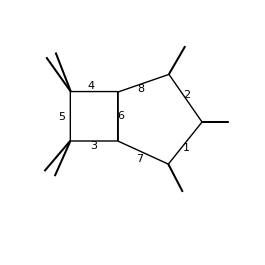

```mathematica
dlist={PD[l1,p1,0],PD[l1,p1+p2,0],PD[l2,0,0],PD[l2,p1+p2+p3,0],PD[l2,p1+p2+p3+p4,0],PD[l1-l2,0,0],PD[l1,0,0],PD[l1,p1+p2+p3,0],PD[l1,p1+p2+p3+p4,0],PD[l2,p1,0],PD[l2,p1+p2,0]};
kinerep={SProd[p1,p1]->0,SProd[p2,p2]->0,SProd[p3,p3]->0,SProd[p4,p4]->mm4,SProd[p1,p2]->s12/2,SProd[p1,p3]->1/2 (-s12-s23+s45),SProd[p1,p4]->1/2 (mm5-s15+s23-s45),SProd[p2,p3]->s23/2,SProd[p2,p4]->1/2 (s15-s23-s34),SProd[p3,p4]->1/2 (-mm4+s34)};
krep=Join[BaikovTrans[dlist/.kinerep][[2]],kinerep];
```

```mathematica
gmat=GramMat[{l1,l2,p1,p2,p3,p4},{l1,l2,p1,p2,p3,p4},krep];
gmat//MatrixForm
```

(x_7 | 1/2 (x_3-x_6+x_7) | 1/2 (x_1-x_7) | 1/2 (-s12-x_1+x_2) | 1/2 (s12-s45-x_2+x_8) | 1/2 (-mm5+s45-x_8+x_9)
1/2 (x_3-x_6+x_7) | x_3 | 1/2 (-x_3+x_10) | 1/2 (-s12-x_10+x_11) | 1/2 (s12-s45+x_4-x_11) | 1/2 (-mm5+s45-x_4+x_5)
1/2 (x_1-x_7) | 1/2 (-x_3+x_10) | 0 | s12/2 | 1/2 (-s12-s23+s45) | 1/2 (mm5-s15+s23-s45)
1/2 (-s12-x_1+x_2) | 1/2 (-s12-x_10+x_11) | s12/2 | 0 | s23/2 | 1/2 (s15-s23-s34)
1/2 (s12-s45-x_2+x_8) | 1/2 (s12-s45+x_4-x_11) | 1/2 (-s12-s23+s45) | s23/2 | 0 | 1/2 (-mm4+s34)
1/2 (-mm5+s45-x_8+x_9) | 1/2 (-mm5+s45-x_4+x_5) | 1/2 (mm5-s15+s23-s45) | 1/2 (s15-s23-s34) | 1/2 (-mm4+s34) | mm4)

```mathematica
CheckPosition[Position[gmat,#][[All,{1,2}]]&/@Table[Subscript[x,i],{i,1,Length[dlist]}]]
```

True: all in one column and one row; False: not in the preferred configuration

{True,True,True,True,True,True,True,True,True,True,True}

```mathematica
intStd=BaikovRep[dlist,{l1,l2},{p1,p2,p3,p4},Abst->True]//Factor
```

{{{G[{p1,p2,p3,p4},{p1,p2,p3,p4}],1/2 (1+2 ϵ)},{G[{l1,l2,p1,p2,p3,p4},{l1,l2,p1,p2,p3,p4}],1/2 (-3-2 ϵ)}},-1/(512 π^(9/2) Gamma[1/2 (-1-2 ϵ)] Gamma[-ϵ])}

```mathematica
resultmatbt=AllSectorBaikovMat[intStd,krep,Exc->{}(*,deBug->True*)];
```

```mathematica
Export["/Users/windfolgen/Documents/datafile/boxtriangle_allbaikov_mat.m",resultmatbt];
```

```mathematica
resultmatbt=Import["/Users/windfolgen/Documents/datafile/boxtriangle_allbaikov_mat.m"];
```

```mathematica
reformmatbt=ReformRep[resultmatbt];
```

### all symbol letters

Analyze  the pole structure in this family

```mathematica
polestructure=PolesAnalyze[resultmatbt,{1,2,3,4,5,6,7,8},krep,11];
```

totally 131 sectors need to be analyzed!

ResolveSingleVariable::additional: This construction may be viable by proper variable transformation but we won't include it: {poly, poly list under square root} {mm4 s12 s15 s23+mm5 s23^2 s34-s15 s23 s34 s45-mm4 s12 s15 x_8+s12 s15^2 x_8+mm5 s15 s23 x_8-s12 s15 s23 x_8-2 mm5 s23 s34 x_8+s15 s23 s34 x_8-s15^2 s45 x_8+«24»,{mm4^2-2 mm4 x_8+x_8^2-2 mm4 x_9-2 x_8 x_9+x_9^2}}.

{mm4 s12 s15 s23+mm5 s23^2 s34-s15 s23 s34 s45-mm4 s12 s15 x_8+s12 s15^2 x_8+mm5 s15 s23 x_8-s12 s15 s23 x_8-2 mm5 s23 s34 x_8+s15 s23 s34 x_8-s15^2 s45 x_8+s15 s34 s45 x_8-mm5 s15 x_8^2+s12 s15 x_8^2+s15^2 x_8^2+mm5 s34 x_8^2-s15 s34 x_8^2-mm4 s12 s23 x_9-s12 s15 s23 x_9-mm5 s23^2 x_9+s12 s23^2 x_9-s23^2 s34 x_9+s15 s23 s45 x_9+s23 s34 s45 x_9+mm4 s12 x_8 x_9-s12 s15 x_8 x_9+mm5 s23 x_8 x_9-s12 s23 x_8 x_9-2 s15 s23 x_8 x_9+s23 s34 x_8 x_9+s15 s45 x_8 x_9-s34 s45 x_8 x_9+s12 s23 x_9^2+s23^2 x_9^2-s23 s45 x_9^2,{mm4^2-2 mm4 x_8+x_8^2-2 mm4 x_9-2 x_8 x_9+x_9^2}}

ResolveSingleVariable::additional: This construction may be viable by proper variable transformation but we won't include it: {poly, poly list under square root} {mm4 s12^2 s15+mm5 s12 s23 s34-s12 s15 s34 s45-2 mm4 s12 s15 x_7+mm4 s12 s34 x_7+s12 s15 s34 x_7-mm5 s23 s34 x_7-s12 s23 s34 x_7+s23 s34^2 x_7+s15 s34 s45 x_7+«24»,{mm5^2-2 mm5 x_7+x_7^2-2 mm5 x_9-2 x_7 x_9+x_9^2}}.

{mm4 s12^2 s15+mm5 s12 s23 s34-s12 s15 s34 s45-2 mm4 s12 s15 x_7+mm4 s12 s34 x_7+s12 s15 s34 x_7-mm5 s23 s34 x_7-s12 s23 s34 x_7+s23 s34^2 x_7+s15 s34 s45 x_7-s34^2 s45 x_7+mm4 s15 x_7^2-mm4 s34 x_7^2-s15 s34 x_7^2+s23 s34 x_7^2+s34^2 x_7^2-mm4 s12^2 x_9-s12^2 s15 x_9-mm5 s12 s23 x_9+s12^2 s23 x_9-s12 s23 s34 x_9+s12 s15 s45 x_9+s12 s34 s45 x_9+mm4 s12 x_7 x_9+s12 s15 x_7 x_9+mm5 s23 x_7 x_9-s12 s23 x_7 x_9-2 s12 s34 x_7 x_9-s23 s34 x_7 x_9-s15 s45 x_7 x_9+s34 s45 x_7 x_9+s12^2 x_9^2+s12 s23 x_9^2-s12 s45 x_9^2,{mm5^2-2 mm5 x_7+x_7^2-2 mm5 x_9-2 x_7 x_9+x_9^2}}

Above warnings are some possible construction for dlogs which may be very special, but we don’t include them and the results are not influenced.

```mathematica
rllist=AllRationalLetters[polestructure]//SortBy[#,LeafCount]&
```

{mm4,mm5,s12,s15,s23,s34,s45,s12+s23,mm5-s15,mm4-s34,s15-s34,s12-s45,s23-s45,s12+s15-s34,s12+s23-s45,s15-s23-s34,mm5 s23-s15 s45,mm4 s12-s34 s45,mm5-s15+s23-s45,mm4+s12-s34-s45,mm4 s12 s15+mm5 s23 s34-s15 s34 s45,mm4 s23-mm5 s23-mm4 s45+s15 s45,mm4 s12-mm5 s12+mm5 s45-s34 s45,mm4 s15-mm4 s34-s15 s34+s23 s34+s34^2,mm5 s15-s12 s15-s15^2-mm5 s34+s15 s34,mm4^2-2 mm4 s15+s15^2-2 mm4 s23-2 s15 s23+s23^2,mm5^2-2 mm5 s12+s12^2-2 mm5 s34-2 s12 s34+s34^2,mm4^2-2 mm4 mm5+mm5^2-2 mm4 s45-2 mm5 s45+s45^2,mm4^2-2 mm4 s15+s15^2-4 mm5 s23-2 mm4 s45+2 s15 s45+s45^2,mm5^2-4 mm4 s12-2 mm5 s34+s34^2-2 mm5 s45+2 s34 s45+s45^2,mm4 s12-mm5 s15+s15^2+mm5 s23-2 s15 s23+s23^2+mm5 s34-s15 s34+s23 s34+s15 s45-s23 s45-s34 s45,mm4 s12+s12^2+mm4 s15+s12 s15+mm5 s23-mm4 s34-2 s12 s34-s15 s34+s34^2-s12 s45-s15 s45+s34 s45,mm4^2 s23-mm4 mm5 s23+mm4 s12 s23-mm4 s23 s34+mm5 s23 s34-mm4^2 s45+mm4 s15 s45+mm4 s34 s45-s15 s34 s45,mm4 mm5 s12-mm5^2 s12-mm4 s12 s15+mm5 s12 s15-mm5 s12 s23+mm5^2 s45-mm5 s15 s45-mm5 s34 s45+s15 s34 s45,mm4^2 s23^2-4 mm4 mm5 s23 s45+2 mm4 s15 s23 s45-2 mm4 s23^2 s45+s15^2 s45^2-2 s15 s23 s45^2+s23^2 s45^2,mm5^2 s12^2-4 mm4 mm5 s12 s45-2 mm5 s12^2 s45+2 mm5 s12 s34 s45+s12^2 s45^2-2 s12 s34 s45^2+s34^2 s45^2,mm4 mm5 s23-mm5^2 s23-mm4 s15 s23+mm5 s15 s23-mm5 s23^2-mm4 mm5 s45+mm4 s15 s45+mm5 s15 s45-s15^2 s45+mm5 s23 s45+s15 s23 s45-s15 s45^2,mm4^2 s12-mm4 mm5 s12+mm4 s12^2-mm4 s12 s34+mm5 s12 s34+mm4 mm5 s45-mm4 s12 s45-mm4 s34 s45-mm5 s34 s45-s12 s34 s45+s34^2 s45+s34 s45^2,mm5^2 s12 s23+mm5^2 s23^2+mm4 mm5 s12 s45-mm5 s12 s15 s45-mm5 s12 s23 s45-2 mm5 s15 s23 s45+mm5 s23 s34 s45+s12 s15 s45^2+s15^2 s45^2-s15 s34 s45^2,mm4^2 s12^2+mm4^2 s12 s23+mm4 s12 s15 s45+mm4 mm5 s23 s45-mm4 s12 s23 s45-2 mm4 s12 s34 s45-mm4 s23 s34 s45-s15 s34 s45^2+s23 s34 s45^2+s34^2 s45^2,mm4^2 s12^2+2 mm4 mm5 s12 s23+mm5^2 s23^2+2 mm4 s12 s15 s45-2 mm5 s15 s23 s45-2 mm4 s12 s34 s45+2 mm5 s23 s34 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2,mm4 s12^2+mm4 s12 s15-mm5 s12 s15+mm4 s12 s23+mm5 s12 s23+mm4 s15 s23-mm5 s15 s23+mm5 s23^2-mm4 s12 s34+mm5 s12 s34-mm4 s23 s34+mm5 s23 s34+s12 s15 s45+s15^2 s45-s12 s23 s45-s15 s23 s45-s12 s34 s45-2 s15 s34 s45+s23 s34 s45+s34^2 s45,mm4^2 s12^2-2 mm4 s12^2 s15+s12^2 s15^2+2 mm4 mm5 s12 s23-2 mm4 s12^2 s23-4 mm4 s12 s15 s23+2 mm5 s12 s15 s23-2 s12^2 s15 s23+mm5^2 s23^2-2 mm5 s12 s23^2+s12^2 s23^2+2 mm4 s12 s23 s34-4 mm5 s12 s23 s34+2 s12 s15 s23 s34-2 mm5 s23^2 s34-2 s12 s23^2 s34+s23^2 s34^2+2 mm4 s12 s15 s45-2 s12 s15^2 s45-2 mm5 s15 s23 s45+2 s12 s15 s23 s45-2 mm4 s12 s34 s45+2 s12 s15 s34 s45+2 mm5 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2}

```mathematica
rllist//Length
```

43

Above are exactly the rational letters in CDE.

```mathematica
Export["/Users/windfolgen/Documents/datafile/pentabox2m_rationalletter_candidate.m",rllist];
```

```mathematica
testalg=ExtractAlgLetter[resultmatbt,{1,2,3,4,5,6,7,8},11];
```

totally 131 sectors need to be analyzed!

```mathematica
poles=ExtractPoleInfo[polestructure,11];
```

All possible square roots when constructing UT basis are needed as an input. They can be extracted from the output of PolesAnalyze

```mathematica
permsqlist=ExtractSquareRoots[polestructure]
```

{(mm4^2-2 mm4 mm5+mm5^2-2 mm4 s45-2 mm5 s45+s45^2) (mm4^2 s12^2-2 mm4 s12^2 s15+s12^2 s15^2+2 mm4 mm5 s12 s23-2 mm4 s12^2 s23-4 mm4 s12 s15 s23+2 mm5 s12 s15 s23-2 s12^2 s15 s23+mm5^2 s23^2-2 mm5 s12 s23^2+s12^2 s23^2+2 mm4 s12 s23 s34-4 mm5 s12 s23 s34+2 s12 s15 s23 s34-2 mm5 s23^2 s34-2 s12 s23^2 s34+s23^2 s34^2+2 mm4 s12 s15 s45-2 s12 s15^2 s45-2 mm5 s15 s23 s45+2 s12 s15 s23 s45-2 mm4 s12 s34 s45+2 s12 s15 s34 s45+2 mm5 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2),mm4^2 s12^2-2 mm4 s12^2 s15+s12^2 s15^2+2 mm4 mm5 s12 s23-2 mm4 s12^2 s23-4 mm4 s12 s15 s23+2 mm5 s12 s15 s23-2 s12^2 s15 s23+mm5^2 s23^2-2 mm5 s12 s23^2+s12^2 s23^2+2 mm4 s12 s23 s34-4 mm5 s12 s23 s34+2 s12 s15 s23 s34-2 mm5 s23^2 s34-2 s12 s23^2 s34+s23^2 s34^2+2 mm4 s12 s15 s45-2 s12 s15^2 s45-2 mm5 s15 s23 s45+2 s12 s15 s23 s45-2 mm4 s12 s34 s45+2 s12 s15 s34 s45+2 mm5 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2,mm4^2-2 mm4 mm5+mm5^2-2 mm4 s45-2 mm5 s45+s45^2,mm5^2 s12^2-4 mm4 mm5 s12 s45-2 mm5 s12^2 s45+2 mm5 s12 s34 s45+s12^2 s45^2-2 s12 s34 s45^2+s34^2 s45^2,mm4^2 s23^2-4 mm4 mm5 s23 s45+2 mm4 s15 s23 s45-2 mm4 s23^2 s45+s15^2 s45^2-2 s15 s23 s45^2+s23^2 s45^2,mm4^2 s12^2+2 mm4 mm5 s12 s23+mm5^2 s23^2+2 mm4 s12 s15 s45-2 mm5 s15 s23 s45-2 mm4 s12 s34 s45+2 mm5 s23 s34 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2,mm5^2-4 mm4 s12-2 mm5 s34+s34^2-2 mm5 s45+2 s34 s45+s45^2,mm5^2-2 mm5 s12+s12^2-2 mm5 s34-2 s12 s34+s34^2,mm4^2-2 mm4 s15+s15^2-2 mm4 s23-2 s15 s23+s23^2,mm4^2-2 mm4 s15+s15^2-4 mm5 s23-2 mm4 s45+2 s15 s45+s45^2}

```mathematica
(*above are all input*)
```

Generate all algebraic letters

```mathematica
testresult=AllAlgLettersPL[poles,testalg,reformmatbt,krep,PermSq->permsqlist];
```

totally 131 sectors need to be analyzed

analyzing first type construction...

session time: 1325.27845

Substituting poles into expressions...

session time: 1723.57196

analyzing second type construction...

session time: 1796.85442

```mathematica
Export["/Users/windfolgen/Documents/datafile/pentabox2m_testresult_new.m",testresult];
```

```mathematica
LetterInfo[mm4^2 s12^2+2 mm4 mm5 s12 s23+mm5^2 s23^2+2 mm4 s12 s15 s45-2 mm5 s15 s23 s45-2 mm4 s12 s34 s45+2 mm5 s23 s34 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2,testresult,polestructure]
```

This letter can be generated from following sectors: {{1,2,3,4,5,6}}

The corresponding path is: {{{x_9,x_8,x_7}}}

To see more information, search the following position of output of PolesAnalyze[]: {37}

We can see that this square root exactly comes from above sectors from the UT basis if we remove those super sectors

```mathematica
algcand=Cases[testresult,Log[_?(FreeQ[#,G]&)],Infinity]//DeleteCases[#,_?(FreeQ[#,Power[_,1/2]]&)]&//DeleteSameAlgLetter;
```

```mathematica
algselect=SelectAlgLetter[algcand,rllist];
```

```mathematica
algselect//Length
```

182

To get all independent algebraic letters.

```mathematica
algind=GetAllAlgIndepLetter[algselect];
```

totally 28 different square roots

```mathematica
algind//Flatten//Length
```

61

```mathematica
Length/@algind
```

{5,3,3,1,1,1,1,1,1,4,4,3,4,12,2,3,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Export["/Users/windfolgen/Documents/datafile/pentabox2m_algind.m",algind];
```

```mathematica
(*Export["/Users/windfolgen/Documents/datafile/pentabox2m_additional_algletter.m",Join[algindsubadd,algindsub1add,algindsub2add]];*)
```

```mathematica
LetterInfo[algind[[5,1]],testresult,polestructure]
```

This letter comes from the first type construction.

It can come from the following gram and poles: {{Log[(G[{p1+p2+p3,p4,l1},{p1+p2+p3,p4,p3}]+√(-G[{p1+p2+p3,p4},{p1+p2+p3,p4}] G[{l1,p3,p1+p2+p3,p4},{l1,p3,p1+p2+p3,p4}]))/(G[{p1+p2+p3,p4,l1},{p1+p2+p3,p4,p3}]-√(-G[{p1+p2+p3,p4},{p1+p2+p3,p4}] G[{l1,p3,p1+p2+p3,p4},{l1,p3,p1+p2+p3,p4}]))],{{x_1→0,x_2→0,x_3→0,x_4→0,x_5→0,x_6→0,x_7→0,x_10→0,x_11→0},{x_8→∞,x_9→∞,x_8→x_9,x_9→0}}},{Log[(G[{l2,p1+p2+p3,p4},{p1+p2+p3,p3,p4}]+√(-G[{p1+p2+p3,p4},{p1+p2+p3,p4}] G[{l2,p3,p1+p2+p3,p4},{l2,p3,p1+p2+p3,p4}]))/(G[{l2,p1+p2+p3,p4},{p1+p2+p3,p3,p4}]-√(-G[{p1+p2+p3,p4},{p1+p2+p3,p4}] G[{l2,p3,p1+p2+p3,p4},{l2,p3,p1+p2+p3,p4}]))],{{x_1→0,x_2→0,x_4→0,x_5→0,x_6→0,x_7→0,x_8→0,x_9→0,x_10→0},{x_3→∞,x_11→∞,x_3→x_11,x_11→0}}}}

## Non-planar Hexa-box in 2107.14180

### zmz configurations

```mathematica
dlist={PD[k1,0,0],PD[k1,-p1-p2-p3-p4,0],PD[k1,-p2-p3-p4,0],PD[k1,-p3-p4,0],PD[k1+k2,-p4,0],PD[k1+k2,0,0],PD[k2,0,0],PD[k2,p3,0],PD[k2,-p1-p2-p3-p4,0],PD[k1,p3,0],PD[k2,-p2-p3-p4,0]};
kinerep={p1·p1->p12,p2·p2->0,p3·p3->0,p4·p4->0,p5·p5->0,p1·p2->1/2 (-p12+s12),p1·p3->1/2 (-s12-s23+s45),p1·p4->1/2 (-s15+s23-s45),p1·p5->1/2 (-p12+s15),p2·p3->s23/2,p2·p4->1/2 (s15-s23-s34),p2·p5->1/2 (p12-s12-s15+s34),p3·p4->s34/2,p3·p5->1/2 (s12-s34-s45),p4·p5->s45/2};
rep=BaikovTrans[dlist/.kinerep];
krep=Join[rep[[2]],kinerep];
```

```mathematica
gmat=GramMat[{k1,k2,p1,p2,p3,p4},{k1,k2,p1,p2,p3,p4},krep];
gmat//MatrixForm
```

(x_1 | 1/2 (-x_1+x_6-x_7) | 1/2 (-s15-x_2+x_3) | 1/2 (s15-s34-x_3+x_4) | 1/2 (-x_1+x_10) | 1/2 (s34+2 x_1-x_4-x_10)
1/2 (-x_1+x_6-x_7) | x_7 | 1/2 (-s15-x_9+x_11) | 1/2 (s15+s34+2 x_1-x_4+x_5-x_6+2 x_7-x_8-x_10-x_11) | 1/2 (-x_7+x_8) | 1/2 (-s34-2 x_1+x_4-x_5+x_6+x_10)
1/2 (-s15-x_2+x_3) | 1/2 (-s15-x_9+x_11) | p12 | 1/2 (-p12+s12) | 1/2 (-s12-s23+s45) | 1/2 (-s15+s23-s45)
1/2 (s15-s34-x_3+x_4) | 1/2 (s15+s34+2 x_1-x_4+x_5-x_6+2 x_7-x_8-x_10-x_11) | 1/2 (-p12+s12) | 0 | s23/2 | 1/2 (s15-s23-s34)
1/2 (-x_1+x_10) | 1/2 (-x_7+x_8) | 1/2 (-s12-s23+s45) | s23/2 | 0 | s34/2
1/2 (s34+2 x_1-x_4-x_10) | 1/2 (-s34-2 x_1+x_4-x_5+x_6+x_10) | 1/2 (-s15+s23-s45) | 1/2 (s15-s23-s34) | s34/2 | 0)

```mathematica
CheckPosition[Position[gmat,#][[All,{1,2}]]&/@Table[Subscript[x,i],{i,1,Length[dlist]}]]
```

True: all in one column and one row; False: not in the preferred configuration

{False,True,True,False,True,True,True,True,True,False,True}

We then perform  a variable transformation which makes sure that propagator x1 will not appear in more than one column and one row. In this way, the non-planar family can be solved just as planar family.

```mathematica
gmat=GramMat[{k1,k2,p1,p2,p3,p4},{k1,k2,p1,p2,p3,p4},krep]/.{Subscript[x, 10]->Subscript[x, 10]+2 Subscript[x, 1]-Subscript[x, 4]}//Factor;
gmat//MatrixForm
```

(x_1 | 1/2 (-x_1+x_6-x_7) | 1/2 (-s15-x_2+x_3) | 1/2 (s15-s34-x_3+x_4) | 1/2 (x_1-x_4+x_10) | 1/2 (s34-x_10)
1/2 (-x_1+x_6-x_7) | x_7 | 1/2 (-s15-x_9+x_11) | 1/2 (s15+s34+x_5-x_6+2 x_7-x_8-x_10-x_11) | 1/2 (-x_7+x_8) | 1/2 (-s34-x_5+x_6+x_10)
1/2 (-s15-x_2+x_3) | 1/2 (-s15-x_9+x_11) | p12 | 1/2 (-p12+s12) | 1/2 (-s12-s23+s45) | 1/2 (-s15+s23-s45)
1/2 (s15-s34-x_3+x_4) | 1/2 (s15+s34+x_5-x_6+2 x_7-x_8-x_10-x_11) | 1/2 (-p12+s12) | 0 | s23/2 | 1/2 (s15-s23-s34)
1/2 (x_1-x_4+x_10) | 1/2 (-x_7+x_8) | 1/2 (-s12-s23+s45) | s23/2 | 0 | s34/2
1/2 (s34-x_10) | 1/2 (-s34-x_5+x_6+x_10) | 1/2 (-s15+s23-s45) | 1/2 (s15-s23-s34) | s34/2 | 0)

```mathematica
CheckPosition[Position[gmat,#][[All,{1,2}]]&/@Table[Subscript[x,i],{i,1,Length[dlist]}]]
```

True: all in one column and one row; False: not in the preferred configuration

{True,True,True,True,True,True,True,True,True,False,True}

```mathematica
intStd=BaikovRep[dlist,{k1,k2},{p1,p2,p3,p4},Abst->True]//Factor
```

{{{G[{p1,p2,p3,p4},{p1,p2,p3,p4}],1/2 (1+2 ϵ)},{G[{k1,k2,p1,p2,p3,p4},{k1,k2,p1,p2,p3,p4}],1/2 (-3-2 ϵ)}},1/(512 π^(9/2) Gamma[1/2 (-1-2 ϵ)] Gamma[-ϵ])}

```mathematica
(*change the replacement rule as we have redefined Subscript[x, 10]*)
```

```mathematica
krepref=krep/.{Subscript[x, 10]->Subscript[x, 10]+2 Subscript[x, 1]-Subscript[x, 4]}
```

{k1·k1→x_1,k1·p1→1/2 (-s15-x_2+x_3),k1·p2→1/2 (s15-s34-x_3+x_4),k1·p3→1/2 (x_1-x_4+x_10),k1·p4→1/2 (s34-x_10),k1·k2→1/2 (-x_1+x_6-x_7),k2·k2→x_7,k2·p4→1/2 (-s34-x_5+x_6+x_10),k2·p3→1/2 (-x_7+x_8),k2·p1→1/2 (-s15-x_9+x_11),k2·p2→1/2 (s15+s34+x_5-x_6+2 x_7-x_8-x_10-x_11),p1·p1→p12,p2·p2→0,p3·p3→0,p4·p4→0,p5·p5→0,p1·p2→1/2 (-p12+s12),p1·p3→1/2 (-s12-s23+s45),p1·p4→1/2 (-s15+s23-s45),p1·p5→1/2 (-p12+s15),p2·p3→s23/2,p2·p4→1/2 (s15-s23-s34),p2·p5→1/2 (p12-s12-s15+s34),p3·p4→s34/2,p3·p5→1/2 (s12-s34-s45),p4·p5→s45/2}

```mathematica
resultmatzmzref=AllSectorBaikovMat[intStd,krepref,Exc->{}];
```

```mathematica
(*Export["/Users/windfolgen/Documents/datafile/hexabox_zmz_baikov_all.m",resultmatzmzref];*)
```

```mathematica
(*resultmatzmzref=Import["/Users/windfolgen/Documents/datafile/hexabox_zmz_baikov_all.m"];*)
```

```mathematica
reformmatzmzref=ReformRep[resultmatzmz];
```

### all symbol letters

Analyze  the pole structure in this family

```mathematica
polestructure=PolesAnalyze[resultmatzmzref,{1,2,3,4,5,6,7,8},krepref,11];
```

totally 125 sectors need to be analyzed!

```mathematica
rllist=AllRationalLetters[polestructure]//SortBy[#,LeafCount]&
```

{p12,s12,s15,s23,s34,s45,s23+s34,s34+s45,p12-s12,p12-s15,s15-s23,s12-s34,s15-s34,s12-s45,s12+s23-s45,s15-s23+s45,s15-s23-s34,s12 s15-p12 s34,s12-s34-s45,p12-s12-s15+s34,s12 s23-p12 s34+s12 s34,s12 s15-s12 s23-p12 s34,s12 s15-p12 s34-s15 s45,p12 s34-s15 s34-s15 s45,s12 s15-s12 s23-p12 s34-p12 s45+s12 s45,s12 s15-p12 s23+s15 s23-p12 s34-s15 s45,p12 s12-s12^2-s12 s23-p12 s45+s12 s45,p12 s15-s15^2-p12 s23+s15 s23-s15 s45,p12^2-2 p12 s23+s23^2-2 p12 s45-2 s23 s45+s45^2,s12 s15-s12 s23+s15 s23-s23^2-p12 s34+s12 s45-s15 s45+2 s23 s45-s45^2,p12^2-2 p12 s12+s12^2-2 p12 s15-2 s12 s15+s15^2+2 p12 s23+2 s12 s23-2 s15 s23+s23^2+4 p12 s34+2 p12 s45-2 s12 s45+2 s15 s45-2 s23 s45+s45^2,s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2+2 s12 s15 s23 s34-2 s12 s23^2 s34+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 s12 s15 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2,s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2}

```mathematica
(*then we get all the rational letters*)
```

Above are exactly all 33 rational letters in this family.

```mathematica
testalg=ExtractAlgLetter[resultmatzmzref,{1,2,3,4,5,6,7,8},11];
```

totally 125 sectors need to be analyzed!

```mathematica
poles=ExtractPoleInfo[polestructure,11];(*all the poles we will use, pay attention the second argument need to be the number of all Baikov variables in this family which is 11 in this case.*)
```

original total 591 poles

final total 221 poles

maximal clique: 5; # of cliques: 679

All possible square roots when constructing UT basis are needed as an input. They can be extracted from the output of PolesAnalyze[]

```mathematica
permsqlist=ExtractSquareRoots[polestructure]
```

{s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2,s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2+2 s12 s15 s23 s34-2 s12 s23^2 s34+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 s12 s15 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2,p12^2-2 p12 s23+s23^2-2 p12 s45-2 s23 s45+s45^2,p12^2-2 p12 s12+s12^2-2 p12 s15-2 s12 s15+s15^2+2 p12 s23+2 s12 s23-2 s15 s23+s23^2+4 p12 s34+2 p12 s45-2 s12 s45+2 s15 s45-2 s23 s45+s45^2}

Generate all algebraic letters

Here we use the parallel version of AllAlgLetters[].

```mathematica
testresult=AllAlgLettersPL[poles,testalg,reformmatzmzref,krepref,PermSq->permsqlist];
```

totally 125 sectors need to be analyzed

analyzing first type construction...

session time: 4099.09465

Substituting poles into expressions...

session time: 4691.20419

analyzing second type construction...

session time: 4817.29242

Next remove equivalent letters

```mathematica
algcand=Cases[testresult,Log[_?(FreeQ[#,G]&)],Infinity]//DeleteCases[#,_?(FreeQ[#,Power[_,1/2]]&)]&//DeleteSameAlgLetter;
```

Put on the constraints from rational letters

```mathematica
algselect=SelectAlgLetter[algcand//RegularizeSquareRoots,rllist];
```

```mathematica
algselect//Length
```

111

get all independent algebraic letters.

```mathematica
algind=GetAllAlgIndepLetter[algselect,deBug->True];
```

totally 7 different square roots

square root: {√(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2)}

length: 74

square root: {√(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2+2 s12 s15 s23 s34-2 s12 s23^2 s34+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 s12 s15 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2)}

length: 11

square root: {√(p12^2-2 p12 s12+s12^2-2 p12 s15-2 s12 s15+s15^2+2 p12 s23+2 s12 s23-2 s15 s23+s23^2+4 p12 s34+2 p12 s45-2 s12 s45+2 s15 s45-2 s23 s45+s45^2)}

length: 12

square root: {√(p12^2-2 p12 s23+s23^2-2 p12 s45-2 s23 s45+s45^2)}

length: 11

square root: {√((p12^2-2 p12 s23+s23^2-2 p12 s45-2 s23 s45+s45^2) (s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2))}

length: 1

square root: {√((s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2+2 s12 s15 s23 s34-2 s12 s23^2 s34+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 s12 s15 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2) (s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2))}

length: 1

square root: {√((p12^2-2 p12 s12+s12^2-2 p12 s15-2 s12 s15+s15^2+2 p12 s23+2 s12 s23-2 s15 s23+s23^2+4 p12 s34+2 p12 s45-2 s12 s45+2 s15 s45-2 s23 s45+s45^2) (s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2))}

length: 1

```mathematica
algind//Flatten//Length
```

23

```mathematica
Length/@algind
```

{8,4,4,4,1,1,1}

The result has been checked to be the same as provided in 2107.14180. See next section

### Compared with 2107.14180

run the code usageExample.m provided in the ancillary files in 2107.14180 first!

```mathematica
letterlist=Cases[Mbar//Normal,dlog[W[z_]]->z,Infinity]//DeleteDuplicates//Sort
```

{1,2,5,6,7,8,9,10,11,12,13,14,15,16,19,21,22,24,27,28,29,30,31,32,33,70,72,91,93,118,119,122,123,124,125,128,129,130,131,132,133,134,135,136,137,162,164,183,185,186,187,189,195,196,198,199}

```mathematica
letterlist//Length
```

56

```mathematica
alphabet[[letterlist]]
```

{p1s,s12,s15,s23,s15-s23-s34,p1s-s12-s15+s34,s34,s12-s34-s45,s45,-p1s+s12,-s12-s23+s45,-s15+s23-s45,-p1s+s15,s15-s34,-s23-s34,-s12+s45,-s15+s23,-s34-s45,s12-s34,s12 s15-p1s s34,-s12 s15+s12 s23+p1s s34+p1s s45-s12 s45,p1s s12-s12^2-s12 s23-p1s s45+s12 s45,-s12 s15+p1s s23-s15 s23+p1s s34+s15 s45,s12 s15-s12 s23+s15 s23-s23^2-p1s s34+s12 s45-s15 s45+2 s23 s45-s45^2,p1s s15-s15^2-p1s s23+s15 s23-s15 s45,s12 s15-s12 s23-p1s s34,s12 s15-s12 (s15-s23-s34)-p1s s34,s12 s15-p1s s34-s15 (s12-s34-s45),s12 s15-p1s s34-s15 s45,(p1s-s23+s45+sqrtG3[1])/(p1s-s23+s45-sqrtG3[1]),(p1s+s12-s15+s23-s45+sqrtG3[2])/(p1s+s12-s15+s23-s45-sqrtG3[2]),(-p1s+s12-s15+s23-s45-sqrtG3[2])/(-p1s+s12-s15+s23-s45+sqrtG3[2]),(p1s+s23-s45+sqrtG3[1])/(p1s+s23-s45-sqrtG3[1]),(p1s-2 s12-s23+s45-sqrtG3[1])/(p1s-2 s12-s23+s45+sqrtG3[1]),-(-p1s+s12+s15-s23+s45+sqrtG3[2])/(p1s-s12-s15+s23-s45+sqrtG3[2]),-(p1s-s12-s15-s23+s45+sqrtG3[2])/(-p1s+s12+s15+s23-s45+sqrtG3[2]),(p1s-2 s15+s23-s45-sqrtG3[1])/(p1s-2 s15+s23-s45+sqrtG3[1]),(-s12 s15+s12 s23+p1s s34+s23 s34+s15 s45-s34 s45-sqrtDelta5)/(-s12 s15+s12 s23+p1s s34+s23 s34+s15 s45-s34 s45+sqrtDelta5),(s12 s23-s12 (p1s-s15+s23-s45)+p1s (s12-s34-s45)+s23 (s12-s34-s45)+(p1s-s15+s23-s45) s45-(s12-s34-s45) s45-sqrtDelta5)/(s12 s23-s12 (p1s-s15+s23-s45)+p1s (s12-s34-s45)+s23 (s12-s34-s45)+(p1s-s15+s23-s45) s45-(s12-s34-s45) s45+sqrtDelta5),(-s12 s15+s12 (s15-s23-s34)+p1s s34+(s15-s23-s34) s34+s15 (s12-s34-s45)-s34 (s12-s34-s45)-sqrtDelta5)/(-s12 s15+s12 (s15-s23-s34)+p1s s34+(s15-s23-s34) s34+s15 (s12-s34-s45)-s34 (s12-s34-s45)+sqrtDelta5),(s12 (s15-s23-s34)+p1s s45+(s15-s23-s34) s45-(s12-s34-s45) s45-s12 (p1s-s12-s23+s45)+(s12-s34-s45) (p1s-s12-s23+s45)-sqrtDelta5)/(s12 (s15-s23-s34)+p1s s45+(s15-s23-s34) s45-(s12-s34-s45) s45-s12 (p1s-s12-s23+s45)+(s12-s34-s45) (p1s-s12-s23+s45)+sqrtDelta5),(s12 (p1s-s12-s15+s34)-s12 (p1s-s15+s23-s45)+s34 (p1s-s15+s23-s45)+p1s (s12-s34-s45)-s34 (s12-s34-s45)+(p1s-s12-s15+s34) (s12-s34-s45)-sqrtDelta5)/(s12 (p1s-s12-s15+s34)-s12 (p1s-s15+s23-s45)+s34 (p1s-s15+s23-s45)+p1s (s12-s34-s45)-s34 (s12-s34-s45)+(p1s-s12-s15+s34) (s12-s34-s45)+sqrtDelta5),(p1s (s15-s23-s34)+s23 (s15-s23-s34)+s15 s45-(s15-s23-s34) s45-s15 (p1s-s12-s23+s45)+s23 (p1s-s12-s23+s45)-sqrtDelta5)/(p1s (s15-s23-s34)+s23 (s15-s23-s34)+s15 s45-(s15-s23-s34) s45-s15 (p1s-s12-s23+s45)+s23 (p1s-s12-s23+s45)+sqrtDelta5),(p1s (p1s-s12-s15+s34)+s23 (p1s-s12-s15+s34)-(p1s-s12-s15+s34) s45+(p1s-s15+s23-s45) s45+s23 (p1s-s12-s23+s45)-(p1s-s15+s23-s45) (p1s-s12-s23+s45)-sqrtDelta5)/(p1s (p1s-s12-s15+s34)+s23 (p1s-s12-s15+s34)-(p1s-s12-s15+s34) s45+(p1s-s15+s23-s45) s45+s23 (p1s-s12-s23+s45)-(p1s-s15+s23-s45) (p1s-s12-s23+s45)+sqrtDelta5),(p1s (p1s-s12-s15+s34)+(s15-s23-s34) (p1s-s12-s15+s34)+(s15-s23-s34) (p1s-s15+s23-s45)-(p1s-s12-s15+s34) (s12-s34-s45)-(p1s-s15+s23-s45) (p1s-s12-s23+s45)+(s12-s34-s45) (p1s-s12-s23+s45)-sqrtDelta5)/(p1s (p1s-s12-s15+s34)+(s15-s23-s34) (p1s-s12-s15+s34)+(s15-s23-s34) (p1s-s15+s23-s45)-(p1s-s12-s15+s34) (s12-s34-s45)-(p1s-s15+s23-s45) (p1s-s12-s23+s45)+(s12-s34-s45) (p1s-s12-s23+s45)+sqrtDelta5),(-s12 s15+s12 s23+s23 s34+s15 s45-s34 s45+sqrtSigma5[1])/(-s12 s15+s12 s23+s23 s34+s15 s45-s34 s45-sqrtSigma5[1]),(-s12 s15+s12 (s15-s23-s34)+(s15-s23-s34) s34+s15 (s12-s34-s45)-s34 (s12-s34-s45)+sqrtSigma5[1])/(-s12 s15+s12 (s15-s23-s34)+(s15-s23-s34) s34+s15 (s12-s34-s45)-s34 (s12-s34-s45)-sqrtSigma5[1]),(-s12 s15+s12 (s15-s23-s34)-(s15-s23-s34) s34+s15 (s12-s34-s45)+s34 (s12-s34-s45)+sqrtSigma5[1])/(-s12 s15+s12 (s15-s23-s34)-(s15-s23-s34) s34+s15 (s12-s34-s45)+s34 (s12-s34-s45)-sqrtSigma5[1]),(-s12 s15+s12 s23-s23 s34+s15 s45+s34 s45+sqrtSigma5[1])/(-s12 s15+s12 s23-s23 s34+s15 s45+s34 s45-sqrtSigma5[1]),(p1s^2 s34+s23^2 s34+s15 s23 s45-2 s23 s34 s45-s15 s45^2+s34 s45^2+s12 s23 (-s23+s45)+s12 s15 (s23+s45)+p1s (s12 (-s15+s23)+(s15-2 s34) s45-2 s23 (s34+s45))+sqrtDelta5 sqrtG3[1])/(p1s^2 s34+s23^2 s34+s15 s23 s45-2 s23 s34 s45-s15 s45^2+s34 s45^2+s12 s23 (-s23+s45)+s12 s15 (s23+s45)+p1s (s12 (-s15+s23)+(s15-2 s34) s45-2 s23 (s34+s45))-sqrtDelta5 sqrtG3[1]),(s12^2 (p1s-s15-s45)-s23 (p1s-s15+s23-s45) (s12-s34-s45)-(p1s-s15+s23-s45)^2 s45+(p1s-s15+s23-s45) (s12-s34-s45) s45+p1s (s12-s34-s45) (-p1s+s15-s23+2 (s12+s23-s34)+s45)+s12 ((p1s-s15+s23-s45)^2-(s12-s34-s45) (p1s-s23+s45)-(p1s-s15+s23-s45) (s23+2 (s12-s34-s45)+s45))-sqrtDelta5 sqrtG3[2])/(s12^2 (p1s-s15-s45)-s23 (p1s-s15+s23-s45) (s12-s34-s45)-(p1s-s15+s23-s45)^2 s45+(p1s-s15+s23-s45) (s12-s34-s45) s45+p1s (s12-s34-s45) (-p1s+s15-s23+2 (s12+s23-s34)+s45)+s12 ((p1s-s15+s23-s45)^2-(s12-s34-s45) (p1s-s23+s45)-(p1s-s15+s23-s45) (s23+2 (s12-s34-s45)+s45))+sqrtDelta5 sqrtG3[2]),((p1s s34-sqrtDelta5-sqrtSigma5[1]) (p1s s34+sqrtDelta5+sqrtSigma5[1]))/((p1s s34+sqrtDelta5-sqrtSigma5[1]) (p1s s34-sqrtDelta5+sqrtSigma5[1])),sqrtG3[1],sqrtG3[2],sqrtDelta5,sqrtSigma5[1]}

```mathematica
Cases[alphabet[[letterlist]]/.roots,Power[_,1/2]]/.{Power[z_,1/2]:>z}//Factor
```

{p1s^2-2 p1s s23+s23^2-2 p1s s45-2 s23 s45+s45^2,p1s^2-2 p1s s12+s12^2-2 p1s s15-2 s12 s15+s15^2+2 p1s s23+2 s12 s23-2 s15 s23+s23^2+4 p1s s34+2 p1s s45-2 s12 s45+2 s15 s45-2 s23 s45+s45^2,s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p1s s12 s15 s34+2 p1s s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p1s^2 s34^2-2 p1s s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p1s s15 s34 s45+2 s12 s15 s34 s45-4 p1s s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p1s s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2,s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2+2 s12 s15 s23 s34-2 s12 s23^2 s34+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 s12 s15 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2}

```mathematica
rationalletterzmz=Join[alphabet[[letterlist]]/.roots//DeleteCases[#,_?(!FreeQ[#,Power[_,1/2]]&)]&,Cases[alphabet[[letterlist]]/.roots,Power[_,1/2]]/.{Power[z_,1/2]:>z}]//Factor
```

{p1s,s12,s15,s23,s15-s23-s34,p1s-s12-s15+s34,s34,s12-s34-s45,s45,-p1s+s12,-s12-s23+s45,-s15+s23-s45,-p1s+s15,s15-s34,-s23-s34,-s12+s45,-s15+s23,-s34-s45,s12-s34,s12 s15-p1s s34,-s12 s15+s12 s23+p1s s34+p1s s45-s12 s45,p1s s12-s12^2-s12 s23-p1s s45+s12 s45,-s12 s15+p1s s23-s15 s23+p1s s34+s15 s45,s12 s15-s12 s23+s15 s23-s23^2-p1s s34+s12 s45-s15 s45+2 s23 s45-s45^2,p1s s15-s15^2-p1s s23+s15 s23-s15 s45,s12 s15-s12 s23-p1s s34,s12 s23-p1s s34+s12 s34,-p1s s34+s15 s34+s15 s45,s12 s15-p1s s34-s15 s45,p1s^2-2 p1s s23+s23^2-2 p1s s45-2 s23 s45+s45^2,p1s^2-2 p1s s12+s12^2-2 p1s s15-2 s12 s15+s15^2+2 p1s s23+2 s12 s23-2 s15 s23+s23^2+4 p1s s34+2 p1s s45-2 s12 s45+2 s15 s45-2 s23 s45+s45^2,s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p1s s12 s15 s34+2 p1s s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p1s^2 s34^2-2 p1s s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p1s s15 s34 s45+2 s12 s15 s34 s45-4 p1s s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p1s s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2,s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2+2 s12 s15 s23 s34-2 s12 s23^2 s34+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 s12 s15 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2}

```mathematica
rationalletterzmz//Length
```

33

```mathematica
algebraicletter=alphabet[[letterlist]]/.roots//DeleteCases[#,_?(FreeQ[#,Power[_,1/2]]&)]&//DeleteCases[#,Power[_,1/2]]&
```

{(p1s-s23+s45+√(p1s^2+(s23-s45)^2-2 p1s (s23+s45)))/(p1s-s23+s45-√(p1s^2+(s23-s45)^2-2 p1s (s23+s45))),(p1s+s12-s15+s23+√(p1s^2+(s12-s15+s23-s45)^2-2 p1s (s12+s15-s23-2 s34-s45))-s45)/(p1s+s12-s15+s23-√(p1s^2+(s12-s15+s23-s45)^2-2 p1s (s12+s15-s23-2 s34-s45))-s45),(-p1s+s12-s15+s23-√(p1s^2+(s12-s15+s23-s45)^2-2 p1s (s12+s15-s23-2 s34-s45))-s45)/(-p1s+s12-s15+s23+√(p1s^2+(s12-s15+s23-s45)^2-2 p1s (s12+s15-s23-2 s34-s45))-s45),(p1s+s23-s45+√(p1s^2+(s23-s45)^2-2 p1s (s23+s45)))/(p1s+s23-s45-√(p1s^2+(s23-s45)^2-2 p1s (s23+s45))),(p1s-2 s12-s23+s45-√(p1s^2+(s23-s45)^2-2 p1s (s23+s45)))/(p1s-2 s12-s23+s45+√(p1s^2+(s23-s45)^2-2 p1s (s23+s45))),-(-p1s+s12+s15-s23+√(p1s^2+(s12-s15+s23-s45)^2-2 p1s (s12+s15-s23-2 s34-s45))+s45)/(p1s-s12-s15+s23+√(p1s^2+(s12-s15+s23-s45)^2-2 p1s (s12+s15-s23-2 s34-s45))-s45),-(p1s-s12-s15-s23+√(p1s^2+(s12-s15+s23-s45)^2-2 p1s (s12+s15-s23-2 s34-s45))+s45)/(-p1s+s12+s15+s23+√(p1s^2+(s12-s15+s23-s45)^2-2 p1s (s12+s15-s23-2 s34-s45))-s45),(p1s-2 s15+s23-s45-√(p1s^2+(s23-s45)^2-2 p1s (s23+s45)))/(p1s-2 s15+s23-s45+√(p1s^2+(s23-s45)^2-2 p1s (s23+s45))),(-s12 s15+s12 s23+p1s s34+s23 s34+s15 s45-s34 s45-√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45))))/(-s12 s15+s12 s23+p1s s34+s23 s34+s15 s45-s34 s45+√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45)))),(s12 s23-s12 (p1s-s15+s23-s45)+p1s (s12-s34-s45)+s23 (s12-s34-s45)+(p1s-s15+s23-s45) s45-(s12-s34-s45) s45-√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45))))/(s12 s23-s12 (p1s-s15+s23-s45)+p1s (s12-s34-s45)+s23 (s12-s34-s45)+(p1s-s15+s23-s45) s45-(s12-s34-s45) s45+√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45)))),(-s12 s15+s12 (s15-s23-s34)+p1s s34+(s15-s23-s34) s34+s15 (s12-s34-s45)-s34 (s12-s34-s45)-√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45))))/(-s12 s15+s12 (s15-s23-s34)+p1s s34+(s15-s23-s34) s34+s15 (s12-s34-s45)-s34 (s12-s34-s45)+√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45)))),(s12 (s15-s23-s34)+p1s s45+(s15-s23-s34) s45-(s12-s34-s45) s45-s12 (p1s-s12-s23+s45)+(s12-s34-s45) (p1s-s12-s23+s45)-√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45))))/(s12 (s15-s23-s34)+p1s s45+(s15-s23-s34) s45-(s12-s34-s45) s45-s12 (p1s-s12-s23+s45)+(s12-s34-s45) (p1s-s12-s23+s45)+√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45)))),(s12 (p1s-s12-s15+s34)-s12 (p1s-s15+s23-s45)+s34 (p1s-s15+s23-s45)+p1s (s12-s34-s45)-s34 (s12-s34-s45)+(p1s-s12-s15+s34) (s12-s34-s45)-√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45))))/(s12 (p1s-s12-s15+s34)-s12 (p1s-s15+s23-s45)+s34 (p1s-s15+s23-s45)+p1s (s12-s34-s45)-s34 (s12-s34-s45)+(p1s-s12-s15+s34) (s12-s34-s45)+√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45)))),(p1s (s15-s23-s34)+s23 (s15-s23-s34)+s15 s45-(s15-s23-s34) s45-s15 (p1s-s12-s23+s45)+s23 (p1s-s12-s23+s45)-√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45))))/(p1s (s15-s23-s34)+s23 (s15-s23-s34)+s15 s45-(s15-s23-s34) s45-s15 (p1s-s12-s23+s45)+s23 (p1s-s12-s23+s45)+√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45)))),(p1s (p1s-s12-s15+s34)+s23 (p1s-s12-s15+s34)-(p1s-s12-s15+s34) s45+(p1s-s15+s23-s45) s45+s23 (p1s-s12-s23+s45)-(p1s-s15+s23-s45) (p1s-s12-s23+s45)-√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45))))/(p1s (p1s-s12-s15+s34)+s23 (p1s-s12-s15+s34)-(p1s-s12-s15+s34) s45+(p1s-s15+s23-s45) s45+s23 (p1s-s12-s23+s45)-(p1s-s15+s23-s45) (p1s-s12-s23+s45)+√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45)))),(p1s (p1s-s12-s15+s34)+(s15-s23-s34) (p1s-s12-s15+s34)+(s15-s23-s34) (p1s-s15+s23-s45)-(p1s-s12-s15+s34) (s12-s34-s45)-(p1s-s15+s23-s45) (p1s-s12-s23+s45)+(s12-s34-s45) (p1s-s12-s23+s45)-√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45))))/(p1s (p1s-s12-s15+s34)+(s15-s23-s34) (p1s-s12-s15+s34)+(s15-s23-s34) (p1s-s15+s23-s45)-(p1s-s12-s15+s34) (s12-s34-s45)-(p1s-s15+s23-s45) (p1s-s12-s23+s45)+(s12-s34-s45) (p1s-s12-s23+s45)+√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45)))),(-s12 s15+s12 s23+s23 s34+s15 s45-s34 s45+√(s12^2 (s15-s23)^2+(s23 s34+(s15-s34) s45)^2+2 s12 (-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))))/(-s12 s15+s12 s23+s23 s34+s15 s45-s34 s45-√(s12^2 (s15-s23)^2+(s23 s34+(s15-s34) s45)^2+2 s12 (-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45)))),(-s12 s15+s12 (s15-s23-s34)+(s15-s23-s34) s34+s15 (s12-s34-s45)-s34 (s12-s34-s45)+√(s12^2 (s15-s23)^2+(s23 s34+(s15-s34) s45)^2+2 s12 (-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))))/(-s12 s15+s12 (s15-s23-s34)+(s15-s23-s34) s34+s15 (s12-s34-s45)-s34 (s12-s34-s45)-√(s12^2 (s15-s23)^2+(s23 s34+(s15-s34) s45)^2+2 s12 (-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45)))),(-s12 s15+s12 (s15-s23-s34)-(s15-s23-s34) s34+s15 (s12-s34-s45)+s34 (s12-s34-s45)+√(s12^2 (s15-s23)^2+(s23 s34+(s15-s34) s45)^2+2 s12 (-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))))/(-s12 s15+s12 (s15-s23-s34)-(s15-s23-s34) s34+s15 (s12-s34-s45)+s34 (s12-s34-s45)-√(s12^2 (s15-s23)^2+(s23 s34+(s15-s34) s45)^2+2 s12 (-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45)))),(-s12 s15+s12 s23-s23 s34+s15 s45+s34 s45+√(s12^2 (s15-s23)^2+(s23 s34+(s15-s34) s45)^2+2 s12 (-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))))/(-s12 s15+s12 s23-s23 s34+s15 s45+s34 s45-√(s12^2 (s15-s23)^2+(s23 s34+(s15-s34) s45)^2+2 s12 (-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45)))),(p1s^2 s34+s23^2 s34+s15 s23 s45-2 s23 s34 s45-s15 s45^2+s34 s45^2+s12 s23 (-s23+s45)+s12 s15 (s23+s45)+p1s (s12 (-s15+s23)+(s15-2 s34) s45-2 s23 (s34+s45))+√(p1s^2+(s23-s45)^2-2 p1s (s23+s45)) √(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45))))/(p1s^2 s34+s23^2 s34+s15 s23 s45-2 s23 s34 s45-s15 s45^2+s34 s45^2+s12 s23 (-s23+s45)+s12 s15 (s23+s45)+p1s (s12 (-s15+s23)+(s15-2 s34) s45-2 s23 (s34+s45))-√(p1s^2+(s23-s45)^2-2 p1s (s23+s45)) √(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45)))),(s12^2 (p1s-s15-s45)-s23 (p1s-s15+s23-s45) (s12-s34-s45)-(p1s-s15+s23-s45)^2 s45+(p1s-s15+s23-s45) (s12-s34-s45) s45+p1s (s12-s34-s45) (-p1s+s15-s23+2 (s12+s23-s34)+s45)+s12 ((p1s-s15+s23-s45)^2-(s12-s34-s45) (p1s-s23+s45)-(p1s-s15+s23-s45) (s23+2 (s12-s34-s45)+s45))-√(p1s^2+(s12-s15+s23-s45)^2-2 p1s (s12+s15-s23-2 s34-s45)) √(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45))))/(s12^2 (p1s-s15-s45)-s23 (p1s-s15+s23-s45) (s12-s34-s45)-(p1s-s15+s23-s45)^2 s45+(p1s-s15+s23-s45) (s12-s34-s45) s45+p1s (s12-s34-s45) (-p1s+s15-s23+2 (s12+s23-s34)+s45)+s12 ((p1s-s15+s23-s45)^2-(s12-s34-s45) (p1s-s23+s45)-(p1s-s15+s23-s45) (s23+2 (s12-s34-s45)+s45))+√(p1s^2+(s12-s15+s23-s45)^2-2 p1s (s12+s15-s23-2 s34-s45)) √(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45)))),((p1s s34-√(s12^2 (s15-s23)^2+(s23 s34+(s15-s34) s45)^2+2 s12 (-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45)))-√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45)))) (p1s s34+√(s12^2 (s15-s23)^2+(s23 s34+(s15-s34) s45)^2+2 s12 (-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45)))+√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45)))))/((p1s s34+√(s12^2 (s15-s23)^2+(s23 s34+(s15-s34) s45)^2+2 s12 (-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45)))-√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45)))) (p1s s34-√(s12^2 (s15-s23)^2+(s23 s34+(s15-s34) s45)^2+2 s12 (-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45)))+√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45)))))}

```mathematica
algebraicletter//Length
```

23

```mathematica
(*check algebraic letters with known results*)
```

```mathematica
algcheck=algebraicletter//GatherBy[#,(Cases[#,Power[_,1/2],Infinity]//DeleteDuplicates)&]&;
```

```mathematica
Length/@algcheck
```

{4,4,8,4,1,1,1}

You can further check all letters above are equivalent to what we have constructed by using function GetAllAlgIndepLetter[] or FindLetterLinearRelation[] to check all letters can be expressed as linear combinations of our sets.

### mzz configurations

```mathematica
dlist={PD[k1,0,0],PD[k1,p1,0],PD[k1,p1+p2,0],PD[k1,p1+p2+p3,0],PD[k1+k2,p1+p2+p3+p4,0],PD[k1+k2,0,0],PD[k2,0,0],PD[k2,p4,0],PD[k2,p1,0],PD[k1,p4,0],PD[k2,p1+p2,0]};
kinerep={p1·p1->p12,p2·p2->0,p3·p3->0,p4·p4->0,p5·p5->0,p1·p2->1/2 (-p12+s12),p1·p3->1/2 (-s12-s23+s45),p1·p4->1/2 (-s15+s23-s45),p1·p5->1/2 (-p12+s15),p2·p3->s23/2,p2·p4->1/2 (s15-s23-s34),p2·p5->1/2 (p12-s12-s15+s34),p3·p4->s34/2,p3·p5->1/2 (s12-s34-s45),p4·p5->s45/2};
rep=BaikovTrans[dlist/.kinerep];
krep=Join[rep[[2]],kinerep];
```

```mathematica
gmat=GramMat[{k1,k2,p1,p2,p3,p4},{k1,k2,p1,p2,p3,p4},krep];
gmat//MatrixForm
```

(x_1 | 1/2 (-x_1+x_6-x_7) | 1/2 (-p12-x_1+x_2) | 1/2 (p12-s12-x_2+x_3) | 1/2 (s12-s45-x_3+x_4) | 1/2 (-x_1+x_10)
1/2 (-x_1+x_6-x_7) | x_7 | 1/2 (-p12-x_7+x_9) | 1/2 (p12-s12-x_9+x_11) | 1/2 (s12+s45+2 x_1-x_4+x_5-x_6+2 x_7-x_8-x_10-x_11) | 1/2 (-x_7+x_8)
1/2 (-p12-x_1+x_2) | 1/2 (-p12-x_7+x_9) | p12 | 1/2 (-p12+s12) | 1/2 (-s12-s23+s45) | 1/2 (-s15+s23-s45)
1/2 (p12-s12-x_2+x_3) | 1/2 (p12-s12-x_9+x_11) | 1/2 (-p12+s12) | 0 | s23/2 | 1/2 (s15-s23-s34)
1/2 (s12-s45-x_3+x_4) | 1/2 (s12+s45+2 x_1-x_4+x_5-x_6+2 x_7-x_8-x_10-x_11) | 1/2 (-s12-s23+s45) | s23/2 | 0 | s34/2
1/2 (-x_1+x_10) | 1/2 (-x_7+x_8) | 1/2 (-s15+s23-s45) | 1/2 (s15-s23-s34) | s34/2 | 0)

```mathematica
CheckPosition[Position[gmat,#][[All,{1,2}]]&/@Table[Subscript[x,i],{i,1,Length[dlist]}]]
```

True: all in one column and one row; False: not in the preferred configuration

{False,True,True,True,True,True,True,True,True,False,True}

We then perform  a variable transformation which makes sure that propagator x1 will not appear in more than one column and one row. In this way, the non-planar family can be solved just as planar family.

```mathematica
gmat=GramMat[{k1,k2,p1,p2,p3,p4},{k1,k2,p1,p2,p3,p4},krep]/.{Subscript[x, 10]->Subscript[x, 10]+2 Subscript[x, 1]-Subscript[x, 4]}//Factor;
gmat//MatrixForm
```

(x_1 | 1/2 (-x_1+x_6-x_7) | 1/2 (-p12-x_1+x_2) | 1/2 (p12-s12-x_2+x_3) | 1/2 (s12-s45-x_3+x_4) | 1/2 (x_1-x_4+x_10)
1/2 (-x_1+x_6-x_7) | x_7 | 1/2 (-p12-x_7+x_9) | 1/2 (p12-s12-x_9+x_11) | 1/2 (s12+s45+x_5-x_6+2 x_7-x_8-x_10-x_11) | 1/2 (-x_7+x_8)
1/2 (-p12-x_1+x_2) | 1/2 (-p12-x_7+x_9) | p12 | 1/2 (-p12+s12) | 1/2 (-s12-s23+s45) | 1/2 (-s15+s23-s45)
1/2 (p12-s12-x_2+x_3) | 1/2 (p12-s12-x_9+x_11) | 1/2 (-p12+s12) | 0 | s23/2 | 1/2 (s15-s23-s34)
1/2 (s12-s45-x_3+x_4) | 1/2 (s12+s45+x_5-x_6+2 x_7-x_8-x_10-x_11) | 1/2 (-s12-s23+s45) | s23/2 | 0 | s34/2
1/2 (x_1-x_4+x_10) | 1/2 (-x_7+x_8) | 1/2 (-s15+s23-s45) | 1/2 (s15-s23-s34) | s34/2 | 0)

```mathematica
CheckPosition[Position[gmat,#][[All,{1,2}]]&/@Table[Subscript[x,i],{i,1,Length[dlist]}]]
```

True: all in one column and one row; False: not in the preferred configuration

{True,True,True,True,True,True,True,True,True,False,True}

```mathematica
intStd=BaikovRep[dlist,{k1,k2},{p1,p2,p3,p4},Abst->True]//Factor
```

{{{G[{p1,p2,p3,p4},{p1,p2,p3,p4}],1/2 (1+2 ϵ)},{G[{k1,k2,p1,p2,p3,p4},{k1,k2,p1,p2,p3,p4}],1/2 (-3-2 ϵ)}},-1/(512 π^(9/2) Gamma[1/2 (-1-2 ϵ)] Gamma[-ϵ])}

```mathematica
(*change the replacement rule as we have redefined Subscript[x, 10]*)
```

```mathematica
krepref=krep/.{Subscript[x, 10]->Subscript[x, 10]+2 Subscript[x, 1]-Subscript[x, 4]}
```

{k1·k1→x_1,k1·p1→1/2 (-p12-x_1+x_2),k1·p2→1/2 (p12-s12-x_2+x_3),k1·p3→1/2 (s12-s45-x_3+x_4),k1·k2→1/2 (-x_1+x_6-x_7),k2·k2→x_7,k1·p4→1/2 (x_1-x_4+x_10),k2·p1→1/2 (-p12-x_7+x_9),k2·p2→1/2 (p12-s12-x_9+x_11),k2·p3→1/2 (s12+s45+x_5-x_6+2 x_7-x_8-x_10-x_11),k2·p4→1/2 (-x_7+x_8),p1·p1→p12,p2·p2→0,p3·p3→0,p4·p4→0,p5·p5→0,p1·p2→1/2 (-p12+s12),p1·p3→1/2 (-s12-s23+s45),p1·p4→1/2 (-s15+s23-s45),p1·p5→1/2 (-p12+s15),p2·p3→s23/2,p2·p4→1/2 (s15-s23-s34),p2·p5→1/2 (p12-s12-s15+s34),p3·p4→s34/2,p3·p5→1/2 (s12-s34-s45),p4·p5→s45/2}

```mathematica
resultmatmzz=AllSectorBaikovMat[intStd,krepref,Exc->{}];
```

```mathematica
(*Export["/Users/windfolgen/Documents/datafile/hexabox_mzz_baikov_all.m",resultmatmzz];*)
```

```mathematica
(*resultmatmzz=Import["/Users/windfolgen/Documents/datafile/hexabox_mzz_baikov_all.m"];*)
```

```mathematica
reformmatmzz=ReformRep[resultmatmzz];
```

### all symbol letters

Analyze  the pole structure in this family

```mathematica
polestructure=PolesAnalyze[resultmatmzz,{1,2,3,4,5,6,7,8},krepref,11];
```

totally 127 sectors need to be analyzed!

```mathematica
rllist=AllRationalLetters[polestructure]//SortBy[#,LeafCount]&
```

{p12,s12,s15,s23,s34,s45,s34+s45,p12-s12,p12-s15,s15-s23,s12-s34,s15-s34,s12-s45,s15-s23+s45,s15-s23-s34,s12 s15-p12 s34,p12-s15-s45,s12-s34-s45,p12-s12-s15+s34,p12-s15+s23-s45,p12-s12-s15+s23+s34,s12 s15-s12 s23-p12 s34,s12 s15-p12 s34-p12 s45+s12 s45,s12 s15-s12 s23-p12 s34-p12 s45+s12 s45,p12 s12-s12^2-s12 s23-p12 s45+s12 s45,p12 s15-s15^2-p12 s23+s15 s23-s15 s45,p12^2-2 p12 s23+s23^2-2 p12 s45-2 s23 s45+s45^2,s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2}

```mathematica
rllist//Length
```

28

```mathematica
(*then we get all the rational letters*)
```

Above are exactly all 28 rational letters in this family.

```mathematica
testalg=ExtractAlgLetter[resultmatmzz,{1,2,3,4,5,6,7,8},11];
```

totally 127 sectors need to be analyzed!

```mathematica
poles=ExtractPoleInfo[polestructure,11];(*all the poles we will use, pay attention the second argument need to be the number of all Baikov variables in this family which is 11 in this case.*)
```

original total 630 poles

final total 244 poles

maximal clique: 5; # of cliques: 1088

```mathematica
(*when the number of poles are huge, we can use the enhanced version of selection of repeated poles*)
```

```mathematica
poles=ExtractPoleInfo[polestructure,11,Enhanced->True];(*all the poles we will use, pay attention the second argument need to be the number of all Baikov variables in this family which is 11 in this case.*)
```

original total 630 poles

final total 148 poles

maximal clique: 5; # of cliques: 513

All possible square roots when constructing UT basis are needed as an input. They can be extracted from the output of PolesAnalyze[]

```mathematica
permsqlist=ExtractSquareRoots[polestructure]
```

{s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2,p12^2-2 p12 s23+s23^2-2 p12 s45-2 s23 s45+s45^2}

Generate all algebraic letters

Here we use the parallel version of AllAlgLetters[].

```mathematica
testresult=AllAlgLettersPL[poles,testalg,reformmatmzz,krepref,PermSq->permsqlist];
```

session time: 4482.64719

Substituting poles into expressions...

session time: 5765.83075

analyzing second type construction...

session time: 5960.52281

Next remove equivalent letters

```mathematica
algcand=Cases[testresult,Log[_?(FreeQ[#,G]&)],Infinity]//DeleteCases[#,_?(FreeQ[#,Power[_,1/2]]&)]&//DeleteSameAlgLetter;
```

Put on the constraints from rational letters

```mathematica
algselect=SelectAlgLetter[algcand//RegularizeSquareRoots,rllist];
```

```mathematica
Cases[algselect,Power[_,1/2],Infinity]//DeleteDuplicates
```

{√(p12^2-2 p12 s23+s23^2-2 p12 s45-2 s23 s45+s45^2),√(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2),√((p12^2-2 p12 s23+s23^2-2 p12 s45-2 s23 s45+s45^2) (s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2))}

```mathematica
algselect//Length
```

111

get all independent algebraic letters.

```mathematica
algind=GetAllAlgIndepLetter[algselect,deBug->True];
```

totally 3 different square roots

square root: {√(p12^2-2 p12 s23+s23^2-2 p12 s45-2 s23 s45+s45^2)}

length: 35

square root: {√(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2)}

length: 75

square root: {√((p12^2-2 p12 s23+s23^2-2 p12 s45-2 s23 s45+s45^2) (s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2))}

length: 1

```mathematica
algind//Flatten//Length
```

11

```mathematica
Length/@algind
```

{4,6,1}

The result has been checked to be the same as provided in 2107.14180. See next section

### Compared with results 2107.14180

run the code usageExample.m provided in the ancillary files in 2107.14180 first!

```mathematica
letterlist=Cases[Mbar//Normal,dlog[W[z_]]->z,Infinity]//DeleteDuplicates//Sort
```

{1,2,4,5,6,7,8,9,10,11,12,14,15,16,17,21,22,24,25,27,28,29,30,33,70,71,118,123,124,129,130,131,132,133,134,137,186,195,198}

```mathematica
letterlist//Length
```

39

```mathematica
alphabet[[letterlist]]
```

{p1s,s12,p1s-s15+s23-s45,s15,s23,s15-s23-s34,p1s-s12-s15+s34,s34,s12-s34-s45,s45,-p1s+s12,-s15+s23-s45,-p1s+s15,s15-s34,p1s-s12-s15+s23+s34,-s12+s45,-s15+s23,-s34-s45,p1s-s15-s45,s12-s34,s12 s15-p1s s34,-s12 s15+s12 s23+p1s s34+p1s s45-s12 s45,p1s s12-s12^2-s12 s23-p1s s45+s12 s45,p1s s15-s15^2-p1s s23+s15 s23-s15 s45,s12 s15-s12 s23-p1s s34,-s12 s23+s12 (p1s-s15+s23-s45)-p1s (s12-s34-s45),(p1s-s23+s45+sqrtG3[1])/(p1s-s23+s45-sqrtG3[1]),(p1s+s23-s45+sqrtG3[1])/(p1s+s23-s45-sqrtG3[1]),(p1s-2 s12-s23+s45-sqrtG3[1])/(p1s-2 s12-s23+s45+sqrtG3[1]),(p1s-2 s15+s23-s45-sqrtG3[1])/(p1s-2 s15+s23-s45+sqrtG3[1]),(-s12 s15+s12 s23+p1s s34+s23 s34+s15 s45-s34 s45-sqrtDelta5)/(-s12 s15+s12 s23+p1s s34+s23 s34+s15 s45-s34 s45+sqrtDelta5),(s12 s23-s12 (p1s-s15+s23-s45)+p1s (s12-s34-s45)+s23 (s12-s34-s45)+(p1s-s15+s23-s45) s45-(s12-s34-s45) s45-sqrtDelta5)/(s12 s23-s12 (p1s-s15+s23-s45)+p1s (s12-s34-s45)+s23 (s12-s34-s45)+(p1s-s15+s23-s45) s45-(s12-s34-s45) s45+sqrtDelta5),(-s12 s15+s12 (s15-s23-s34)+p1s s34+(s15-s23-s34) s34+s15 (s12-s34-s45)-s34 (s12-s34-s45)-sqrtDelta5)/(-s12 s15+s12 (s15-s23-s34)+p1s s34+(s15-s23-s34) s34+s15 (s12-s34-s45)-s34 (s12-s34-s45)+sqrtDelta5),(s12 (s15-s23-s34)+p1s s45+(s15-s23-s34) s45-(s12-s34-s45) s45-s12 (p1s-s12-s23+s45)+(s12-s34-s45) (p1s-s12-s23+s45)-sqrtDelta5)/(s12 (s15-s23-s34)+p1s s45+(s15-s23-s34) s45-(s12-s34-s45) s45-s12 (p1s-s12-s23+s45)+(s12-s34-s45) (p1s-s12-s23+s45)+sqrtDelta5),(s12 (p1s-s12-s15+s34)-s12 (p1s-s15+s23-s45)+s34 (p1s-s15+s23-s45)+p1s (s12-s34-s45)-s34 (s12-s34-s45)+(p1s-s12-s15+s34) (s12-s34-s45)-sqrtDelta5)/(s12 (p1s-s12-s15+s34)-s12 (p1s-s15+s23-s45)+s34 (p1s-s15+s23-s45)+p1s (s12-s34-s45)-s34 (s12-s34-s45)+(p1s-s12-s15+s34) (s12-s34-s45)+sqrtDelta5),(p1s (p1s-s12-s15+s34)+(s15-s23-s34) (p1s-s12-s15+s34)+(s15-s23-s34) (p1s-s15+s23-s45)-(p1s-s12-s15+s34) (s12-s34-s45)-(p1s-s15+s23-s45) (p1s-s12-s23+s45)+(s12-s34-s45) (p1s-s12-s23+s45)-sqrtDelta5)/(p1s (p1s-s12-s15+s34)+(s15-s23-s34) (p1s-s12-s15+s34)+(s15-s23-s34) (p1s-s15+s23-s45)-(p1s-s12-s15+s34) (s12-s34-s45)-(p1s-s15+s23-s45) (p1s-s12-s23+s45)+(s12-s34-s45) (p1s-s12-s23+s45)+sqrtDelta5),(p1s^2 s34+s23^2 s34+s15 s23 s45-2 s23 s34 s45-s15 s45^2+s34 s45^2+s12 s23 (-s23+s45)+s12 s15 (s23+s45)+p1s (s12 (-s15+s23)+(s15-2 s34) s45-2 s23 (s34+s45))+sqrtDelta5 sqrtG3[1])/(p1s^2 s34+s23^2 s34+s15 s23 s45-2 s23 s34 s45-s15 s45^2+s34 s45^2+s12 s23 (-s23+s45)+s12 s15 (s23+s45)+p1s (s12 (-s15+s23)+(s15-2 s34) s45-2 s23 (s34+s45))-sqrtDelta5 sqrtG3[1]),sqrtG3[1],sqrtDelta5}

```mathematica
Cases[alphabet[[letterlist]]/.roots,Power[_,1/2]]/.{Power[z_,1/2]:>z}//Factor
```

{p1s^2-2 p1s s23+s23^2-2 p1s s45-2 s23 s45+s45^2,s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p1s s12 s15 s34+2 p1s s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p1s^2 s34^2-2 p1s s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p1s s15 s34 s45+2 s12 s15 s34 s45-4 p1s s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p1s s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2}

```mathematica
rationallettermzz=Join[alphabet[[letterlist]]/.roots//DeleteCases[#,_?(!FreeQ[#,Power[_,1/2]]&)]&,Cases[alphabet[[letterlist]]/.roots,Power[_,1/2]]/.{Power[z_,1/2]:>z}]//Factor
```

{p1s,s12,p1s-s15+s23-s45,s15,s23,s15-s23-s34,p1s-s12-s15+s34,s34,s12-s34-s45,s45,-p1s+s12,-s15+s23-s45,-p1s+s15,s15-s34,p1s-s12-s15+s23+s34,-s12+s45,-s15+s23,-s34-s45,p1s-s15-s45,s12-s34,s12 s15-p1s s34,-s12 s15+s12 s23+p1s s34+p1s s45-s12 s45,p1s s12-s12^2-s12 s23-p1s s45+s12 s45,p1s s15-s15^2-p1s s23+s15 s23-s15 s45,s12 s15-s12 s23-p1s s34,-s12 s15+p1s s34+p1s s45-s12 s45,p1s^2-2 p1s s23+s23^2-2 p1s s45-2 s23 s45+s45^2,s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p1s s12 s15 s34+2 p1s s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p1s^2 s34^2-2 p1s s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p1s s15 s34 s45+2 s12 s15 s34 s45-4 p1s s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p1s s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2}

```mathematica
rationallettermzz//Length
```

28

```mathematica
algebraicletter=alphabet[[letterlist]]/.roots//DeleteCases[#,_?(FreeQ[#,Power[_,1/2]]&)]&//DeleteCases[#,Power[_,1/2]]&
```

{(p1s-s23+s45+√(p1s^2+(s23-s45)^2-2 p1s (s23+s45)))/(p1s-s23+s45-√(p1s^2+(s23-s45)^2-2 p1s (s23+s45))),(p1s+s23-s45+√(p1s^2+(s23-s45)^2-2 p1s (s23+s45)))/(p1s+s23-s45-√(p1s^2+(s23-s45)^2-2 p1s (s23+s45))),(p1s-2 s12-s23+s45-√(p1s^2+(s23-s45)^2-2 p1s (s23+s45)))/(p1s-2 s12-s23+s45+√(p1s^2+(s23-s45)^2-2 p1s (s23+s45))),(p1s-2 s15+s23-s45-√(p1s^2+(s23-s45)^2-2 p1s (s23+s45)))/(p1s-2 s15+s23-s45+√(p1s^2+(s23-s45)^2-2 p1s (s23+s45))),(-s12 s15+s12 s23+p1s s34+s23 s34+s15 s45-s34 s45-√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45))))/(-s12 s15+s12 s23+p1s s34+s23 s34+s15 s45-s34 s45+√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45)))),(s12 s23-s12 (p1s-s15+s23-s45)+p1s (s12-s34-s45)+s23 (s12-s34-s45)+(p1s-s15+s23-s45) s45-(s12-s34-s45) s45-√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45))))/(s12 s23-s12 (p1s-s15+s23-s45)+p1s (s12-s34-s45)+s23 (s12-s34-s45)+(p1s-s15+s23-s45) s45-(s12-s34-s45) s45+√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45)))),(-s12 s15+s12 (s15-s23-s34)+p1s s34+(s15-s23-s34) s34+s15 (s12-s34-s45)-s34 (s12-s34-s45)-√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45))))/(-s12 s15+s12 (s15-s23-s34)+p1s s34+(s15-s23-s34) s34+s15 (s12-s34-s45)-s34 (s12-s34-s45)+√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45)))),(s12 (s15-s23-s34)+p1s s45+(s15-s23-s34) s45-(s12-s34-s45) s45-s12 (p1s-s12-s23+s45)+(s12-s34-s45) (p1s-s12-s23+s45)-√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45))))/(s12 (s15-s23-s34)+p1s s45+(s15-s23-s34) s45-(s12-s34-s45) s45-s12 (p1s-s12-s23+s45)+(s12-s34-s45) (p1s-s12-s23+s45)+√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45)))),(s12 (p1s-s12-s15+s34)-s12 (p1s-s15+s23-s45)+s34 (p1s-s15+s23-s45)+p1s (s12-s34-s45)-s34 (s12-s34-s45)+(p1s-s12-s15+s34) (s12-s34-s45)-√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45))))/(s12 (p1s-s12-s15+s34)-s12 (p1s-s15+s23-s45)+s34 (p1s-s15+s23-s45)+p1s (s12-s34-s45)-s34 (s12-s34-s45)+(p1s-s12-s15+s34) (s12-s34-s45)+√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45)))),(p1s (p1s-s12-s15+s34)+(s15-s23-s34) (p1s-s12-s15+s34)+(s15-s23-s34) (p1s-s15+s23-s45)-(p1s-s12-s15+s34) (s12-s34-s45)-(p1s-s15+s23-s45) (p1s-s12-s23+s45)+(s12-s34-s45) (p1s-s12-s23+s45)-√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45))))/(p1s (p1s-s12-s15+s34)+(s15-s23-s34) (p1s-s12-s15+s34)+(s15-s23-s34) (p1s-s15+s23-s45)-(p1s-s12-s15+s34) (s12-s34-s45)-(p1s-s15+s23-s45) (p1s-s12-s23+s45)+(s12-s34-s45) (p1s-s12-s23+s45)+√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45)))),(p1s^2 s34+s23^2 s34+s15 s23 s45-2 s23 s34 s45-s15 s45^2+s34 s45^2+s12 s23 (-s23+s45)+s12 s15 (s23+s45)+p1s (s12 (-s15+s23)+(s15-2 s34) s45-2 s23 (s34+s45))+√(p1s^2+(s23-s45)^2-2 p1s (s23+s45)) √(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45))))/(p1s^2 s34+s23^2 s34+s15 s23 s45-2 s23 s34 s45-s15 s45^2+s34 s45^2+s12 s23 (-s23+s45)+s12 s15 (s23+s45)+p1s (s12 (-s15+s23)+(s15-2 s34) s45-2 s23 (s34+s45))-√(p1s^2+(s23-s45)^2-2 p1s (s23+s45)) √(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45))))}

```mathematica
algebraicletter//Length
```

11

```mathematica
tem=RIntersection[rationallettermzz,rllist/.{p12->p1s}];
```

```mathematica
Complement[rationallettermzz,tem[[1]]]
```

{}

```mathematica
Complement[rllist/.{p12->p1s},tem[[2]]]
```

{}

```mathematica
(*check with known results*)
```

```mathematica
algcheck=algebraicletter//GatherBy[#,(Cases[#,Power[_,1/2],Infinity]//DeleteDuplicates)&]&;
```

```mathematica
Length/@algcheck
```

{4,6,1}

```mathematica
GetAllAlgIndepLetter[Join[algind[[2]],Log/@(algcheck[[2]]/.{p1s->p12}//.{Power[a_,1/2]:>Power[a//Factor,1/2],Power[a_,1/2]*Power[b_,1/2]:>Power[a*b//Factor,1/2]})]]
```

totally 1 different square roots

{{Log[(-s12 s15+s12 s23+p12 s34+s23 s34+s15 s45-s34 s45-√(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2))/(-s12 s15+s12 s23+p12 s34+s23 s34+s15 s45-s34 s45+√(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2))],Log[-((-s12 s15-s12 s23+p12 s34+s23 s34+s15 s45-s34 s45+√(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2))/(s12 s15+s12 s23-p12 s34-s23 s34-s15 s45+s34 s45+√(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2)))],Log[-((-s12 s15+s12 s23+p12 s34-s23 s34-s15 s45+s34 s45+√(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2))/(s12 s15-s12 s23-p12 s34+s23 s34+s15 s45-s34 s45+√(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2)))],Log[-((s12 s15-s12 s23-p12 s34+s23 s34-s15 s45+s34 s45+√(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2))/(-s12 s15+s12 s23+p12 s34-s23 s34+s15 s45-s34 s45+√(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2)))],Log[-((s12 s15-s12 s23+p12 s34-2 s12 s34-s23 s34-s15 s45+s34 s45+√(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2))/(-s12 s15+s12 s23-p12 s34+2 s12 s34+s23 s34+s15 s45-s34 s45+√(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2)))],Log[-((-s12 s15+s12 s23-p12 s34+2 s15 s34-s23 s34+s15 s45+s34 s45+√(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2))/(s12 s15-s12 s23+p12 s34-2 s15 s34+s23 s34-s15 s45-s34 s45+√(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2)))]}}

### zzz configurations

```mathematica
dlist={PD[k1,0,0],PD[k1,p2,0],PD[k1,p2+p3,0],PD[k1,p2+p3+p4,0],PD[k1+k2,p1+p2+p3+p4,0],PD[k1+k2,0,0],PD[k2,0,0],PD[k2,p1,0],PD[k2,p2,0],PD[k1,p1,0],PD[k2,p2+p3,0]};
kinerep={p1·p1->p12,p2·p2->0,p3·p3->0,p4·p4->0,p5·p5->0,p1·p2->1/2 (-p12+s12),p1·p3->1/2 (-s12-s23+s45),p1·p4->1/2 (-s15+s23-s45),p1·p5->1/2 (-p12+s15),p2·p3->s23/2,p2·p4->1/2 (s15-s23-s34),p2·p5->1/2 (p12-s12-s15+s34),p3·p4->s34/2,p3·p5->1/2 (s12-s34-s45),p4·p5->s45/2};
rep=BaikovTrans[dlist/.kinerep];
krep=Join[rep[[2]],kinerep];
```

```mathematica
gmat=GramMat[{k1,k2,p1,p2,p3,p4},{k1,k2,p1,p2,p3,p4},krep];
gmat//MatrixForm
```

(x_1 | 1/2 (-x_1+x_6-x_7) | 1/2 (-p12-x_1+x_10) | 1/2 (-x_1+x_2) | 1/2 (-s23-x_2+x_3) | 1/2 (-s15+s23-x_3+x_4)
1/2 (-x_1+x_6-x_7) | x_7 | 1/2 (-p12-x_7+x_8) | 1/2 (-x_7+x_9) | 1/2 (-s23-x_9+x_11) | 1/2 (2 p12+s15+s23+2 x_1-x_4+x_5-x_6+2 x_7-x_8-x_10-x_11)
1/2 (-p12-x_1+x_10) | 1/2 (-p12-x_7+x_8) | p12 | 1/2 (-p12+s12) | 1/2 (-s12-s23+s45) | 1/2 (-s15+s23-s45)
1/2 (-x_1+x_2) | 1/2 (-x_7+x_9) | 1/2 (-p12+s12) | 0 | s23/2 | 1/2 (s15-s23-s34)
1/2 (-s23-x_2+x_3) | 1/2 (-s23-x_9+x_11) | 1/2 (-s12-s23+s45) | s23/2 | 0 | s34/2
1/2 (-s15+s23-x_3+x_4) | 1/2 (2 p12+s15+s23+2 x_1-x_4+x_5-x_6+2 x_7-x_8-x_10-x_11) | 1/2 (-s15+s23-s45) | 1/2 (s15-s23-s34) | s34/2 | 0)

```mathematica
CheckPosition[Position[gmat,#][[All,{1,2}]]&/@Table[Subscript[x,i],{i,1,Length[dlist]}]]
```

True: all in one column and one row; False: not in the preferred configuration

{False,True,True,True,True,True,True,True,True,False,True}

We then perform  a variable transformation which makes sure that propagator x1 will not appear in more than one column and one row. In this way, the non-planar family can be solved just as planar family.

```mathematica
gmat=GramMat[{k1,k2,p1,p2,p3,p4},{k1,k2,p1,p2,p3,p4},krep]/.{Subscript[x, 10]->Subscript[x, 10]+2 Subscript[x, 1]-Subscript[x, 4]}//Factor;
gmat//MatrixForm
```

(x_1 | 1/2 (-x_1+x_6-x_7) | 1/2 (-p12+x_1-x_4+x_10) | 1/2 (-x_1+x_2) | 1/2 (-s23-x_2+x_3) | 1/2 (-s15+s23-x_3+x_4)
1/2 (-x_1+x_6-x_7) | x_7 | 1/2 (-p12-x_7+x_8) | 1/2 (-x_7+x_9) | 1/2 (-s23-x_9+x_11) | 1/2 (2 p12+s15+s23+x_5-x_6+2 x_7-x_8-x_10-x_11)
1/2 (-p12+x_1-x_4+x_10) | 1/2 (-p12-x_7+x_8) | p12 | 1/2 (-p12+s12) | 1/2 (-s12-s23+s45) | 1/2 (-s15+s23-s45)
1/2 (-x_1+x_2) | 1/2 (-x_7+x_9) | 1/2 (-p12+s12) | 0 | s23/2 | 1/2 (s15-s23-s34)
1/2 (-s23-x_2+x_3) | 1/2 (-s23-x_9+x_11) | 1/2 (-s12-s23+s45) | s23/2 | 0 | s34/2
1/2 (-s15+s23-x_3+x_4) | 1/2 (2 p12+s15+s23+x_5-x_6+2 x_7-x_8-x_10-x_11) | 1/2 (-s15+s23-s45) | 1/2 (s15-s23-s34) | s34/2 | 0)

```mathematica
CheckPosition[Position[gmat,#][[All,{1,2}]]&/@Table[Subscript[x,i],{i,1,Length[dlist]}]]
```

True: all in one column and one row; False: not in the preferred configuration

{True,True,True,True,True,True,True,True,True,False,True}

```mathematica
intStd=BaikovRep[dlist,{k1,k2},{p1,p2,p3,p4},Abst->True]//Factor
```

{{{G[{p1,p2,p3,p4},{p1,p2,p3,p4}],1/2 (1+2 ϵ)},{G[{k1,k2,p1,p2,p3,p4},{k1,k2,p1,p2,p3,p4}],1/2 (-3-2 ϵ)}},1/(512 π^(9/2) Gamma[1/2 (-1-2 ϵ)] Gamma[-ϵ])}

```mathematica
(*change the replacement rule as we have redefined Subscript[x, 10]*)
```

```mathematica
krepref=krep/.{Subscript[x, 10]->Subscript[x, 10]+2 Subscript[x, 1]-Subscript[x, 4]}
```

{k1·k1→x_1,k1·p2→1/2 (-x_1+x_2),k1·p3→1/2 (-s23-x_2+x_3),k1·p4→1/2 (-s15+s23-x_3+x_4),k1·k2→1/2 (-x_1+x_6-x_7),k2·k2→x_7,k1·p1→1/2 (-p12+x_1-x_4+x_10),k2·p1→1/2 (-p12-x_7+x_8),k2·p2→1/2 (-x_7+x_9),k2·p3→1/2 (-s23-x_9+x_11),k2·p4→1/2 (2 p12+s15+s23+x_5-x_6+2 x_7-x_8-x_10-x_11),p1·p1→p12,p2·p2→0,p3·p3→0,p4·p4→0,p5·p5→0,p1·p2→1/2 (-p12+s12),p1·p3→1/2 (-s12-s23+s45),p1·p4→1/2 (-s15+s23-s45),p1·p5→1/2 (-p12+s15),p2·p3→s23/2,p2·p4→1/2 (s15-s23-s34),p2·p5→1/2 (p12-s12-s15+s34),p3·p4→s34/2,p3·p5→1/2 (s12-s34-s45),p4·p5→s45/2}

```mathematica
resultmatzzz=AllSectorBaikovMat[intStd,krepref,Exc->{}];
```

```mathematica
(*Export["/Users/windfolgen/Documents/datafile/hexabox_zzz_baikov_all.m",resultmatzzz];*)
```

```mathematica
(*resultmatzzz=Import["/Users/windfolgen/Documents/datafile/hexabox_zzz_baikov_all.m"];*)
```

```mathematica
reformmatzzz=ReformRep[resultmatzzz];
```

### all symbol letters

Analyze  the pole structure in this family

```mathematica
polestructure=PolesAnalyze[resultmatzzz,{1,2,3,4,5,6,7,8},krepref,11];
```

totally 135 sectors need to be analyzed!

ResolveSingleVariable::additional: This construction may be viable by proper variable transformation but we won't include it: {poly, poly list under square root} {4 p12^2 s15 s23-2 p12 s12 s15 s23-4 p12^2 s23^2+2 p12 s12 s23^2-2 p12^2 s23 s34-2 p12 s23^2 s34-2 p12 s15 s23 s45+s12 s15 s23 s45+p12 s23 s34 s45+2 p12 s12 s15 x_1+«32»,{p12^2-6 p12 x_1+x_1^2-2 p12 x_10+2 x_1 x_10+x_10^2}}.

{4 p12^2 s15 s23-2 p12 s12 s15 s23-4 p12^2 s23^2+2 p12 s12 s23^2-2 p12^2 s23 s34-2 p12 s23^2 s34-2 p12 s15 s23 s45+s12 s15 s23 s45+p12 s23 s34 s45+2 p12 s12 s15 x_1-2 p12 s12 s23 x_1-2 p12^2 s34 x_1+2 p12 s23 s34 x_1-2 p12 s15 s45 x_1-s12 s15 s45 x_1+4 p12 s23 s45 x_1-s12 s23 s45 x_1+3 p12 s34 s45 x_1+s23 s34 s45 x_1+s15 s45^2 x_1-s34 s45^2 x_1+s12 s45 x_1^2-s34 s45 x_1^2-s45^2 x_1^2-4 p12 s15 s23 x_10+s12 s15 s23 x_10+4 p12 s23^2 x_10-s12 s23^2 x_10+3 p12 s23 s34 x_10+s23^2 s34 x_10+s15 s23 s45 x_10-s23 s34 s45 x_10-s12 s15 x_1 x_10+s12 s23 x_1 x_10+p12 s34 x_1 x_10-s23 s34 x_1 x_10+s15 s45 x_1 x_10-2 s23 s45 x_1 x_10-s34 s45 x_1 x_10+s15 s23 x_10^2-s23^2 x_10^2-s23 s34 x_10^2,{p12^2-6 p12 x_1+x_1^2-2 p12 x_10+2 x_1 x_10+x_10^2}}

ResolveSingleVariable::additional: This construction may be viable by proper variable transformation but we won't include it: {poly, poly list under square root} {4 p12^2 s15 s34-2 p12 s12 s15 s34-4 p12^2 s23 s34+2 p12 s12 s23 s34-2 p12^2 s34^2-2 p12 s23 s34^2-2 p12 s15 s34 s45+s12 s15 s34 s45+p12 s34^2 s45-2 p12 s12 s15 x_4+«47»,{4 p12^2+4 p12 s15+s15^2+2 s15 x_4+x_4^2-4 p12 x_10-2 s15 x_10-2 x_4 x_10+x_10^2}}.

{4 p12^2 s15 s34-2 p12 s12 s15 s34-4 p12^2 s23 s34+2 p12 s12 s23 s34-2 p12^2 s34^2-2 p12 s23 s34^2-2 p12 s15 s34 s45+s12 s15 s34 s45+p12 s34^2 s45-2 p12 s12 s15 x_4+s12^2 s15 x_4+2 p12 s12 s23 x_4-s12^2 s23 x_4-2 p12^2 s34 x_4+3 p12 s12 s34 x_4+4 p12 s15 s34 x_4-s12 s15 s34 x_4-2 p12 s23 s34 x_4+2 s12 s23 s34 x_4-3 p12 s34^2 x_4-s23 s34^2 x_4+2 p12 s15 s45 x_4-s12 s15 s45 x_4-s12 s34 s45 x_4-s15 s34 s45 x_4+s34^2 s45 x_4+p12 s12 x_4^2-s12^2 x_4^2-s12 s15 x_4^2-p12 s34 x_4^2+2 s12 s34 x_4^2+s15 s34 x_4^2-s34^2 x_4^2-p12 s45 x_4^2+s12 s45 x_4^2+s15 s45 x_4^2-s34 s45 x_4^2-4 p12 s15 s34 x_10+s12 s15 s34 x_10+4 p12 s23 s34 x_10-s12 s23 s34 x_10+3 p12 s34^2 x_10+s23 s34^2 x_10+s15 s34 s45 x_10-s34^2 s45 x_10+s12 s15 x_4 x_10-s12 s23 x_4 x_10+p12 s34 x_4 x_10-2 s12 s34 x_4 x_10-2 s15 s34 x_4 x_10+s23 s34 x_4 x_10+2 s34^2 x_4 x_10-s15 s45 x_4 x_10+s34 s45 x_4 x_10+s15 s34 x_10^2-s23 s34 x_10^2-s34^2 x_10^2,{4 p12^2+4 p12 s15+s15^2+2 s15 x_4+x_4^2-4 p12 x_10-2 s15 x_10-2 x_4 x_10+x_10^2}}

ResolveSingleVariable::additional: This construction may be viable by proper variable transformation but we won't include it: {poly, poly list under square root} {4 p12^2 s15 s23 s34-2 p12 s12 s15 s23 s34-4 p12^2 s23^2 s34+2 p12 s12 s23^2 s34-2 p12^2 s23 s34^2-2 p12 s23^2 s34^2-2 p12 s15 s23 s34 s45+s12 s15 s23 s34 s45+p12 s23 s34^2 s45+2 p12 s12 s15 s34 x_1+«85»,{p12^2-6 p12 x_1+x_1^2+2 p12 x_4-2 x_1 x_4+x_4^2-2 p12 x_10+2 x_1 x_10-2 x_4 x_10+x_10^2}}.

General::stop: Further output of ResolveSingleVariable::additional will be suppressed during this calculation.

{4 p12^2 s15 s23 s34-2 p12 s12 s15 s23 s34-4 p12^2 s23^2 s34+2 p12 s12 s23^2 s34-2 p12^2 s23 s34^2-2 p12 s23^2 s34^2-2 p12 s15 s23 s34 s45+s12 s15 s23 s34 s45+p12 s23 s34^2 s45+2 p12 s12 s15 s34 x_1-2 p12 s12 s23 s34 x_1-2 p12^2 s34^2 x_1+2 p12 s23 s34^2 x_1-2 p12 s15 s34 s45 x_1-s12 s15 s34 s45 x_1+4 p12 s23 s34 s45 x_1-s12 s23 s34 s45 x_1+3 p12 s34^2 s45 x_1+s23 s34^2 s45 x_1+s15 s34 s45^2 x_1-s34^2 s45^2 x_1+s12 s34 s45 x_1^2-s34^2 s45 x_1^2-s34 s45^2 x_1^2-2 p12 s12 s15 s23 x_4+s12^2 s15 s23 x_4+2 p12 s12 s23^2 x_4-s12^2 s23^2 x_4-2 p12^2 s23 s34 x_4+3 p12 s12 s23 s34 x_4+4 p12 s15 s23 s34 x_4-s12 s15 s23 s34 x_4-2 p12 s23^2 s34 x_4+2 s12 s23^2 s34 x_4-3 p12 s23 s34^2 x_4-s23^2 s34^2 x_4+2 p12 s15 s23 s45 x_4-s12 s15 s23 s45 x_4-s12 s23 s34 s45 x_4-s15 s23 s34 s45 x_4+s23 s34^2 s45 x_4-s12^2 s15 x_1 x_4+s12^2 s23 x_1 x_4+p12 s12 s34 x_1 x_4+«15»+s23 s34 s45 x_1 x_4+s34^2 s45 x_1 x_4-s15 s45^2 x_1 x_4+s34 s45^2 x_1 x_4+p12 s12 s23 x_4^2-s12^2 s23 x_4^2-s12 s15 s23 x_4^2-p12 s23 s34 x_4^2+2 s12 s23 s34 x_4^2+s15 s23 s34 x_4^2-s23 s34^2 x_4^2-p12 s23 s45 x_4^2+s12 s23 s45 x_4^2+s15 s23 s45 x_4^2-s23 s34 s45 x_4^2-4 p12 s15 s23 s34 x_10+s12 s15 s23 s34 x_10+4 p12 s23^2 s34 x_10-s12 s23^2 s34 x_10+3 p12 s23 s34^2 x_10+s23^2 s34^2 x_10+s15 s23 s34 s45 x_10-s23 s34^2 s45 x_10-s12 s15 s34 x_1 x_10+s12 s23 s34 x_1 x_10+p12 s34^2 x_1 x_10-s23 s34^2 x_1 x_10+s15 s34 s45 x_1 x_10-2 s23 s34 s45 x_1 x_10-s34^2 s45 x_1 x_10+s12 s15 s23 x_4 x_10-s12 s23^2 x_4 x_10+p12 s23 s34 x_4 x_10-2 s12 s23 s34 x_4 x_10-2 s15 s23 s34 x_4 x_10+s23^2 s34 x_4 x_10+2 s23 s34^2 x_4 x_10-s15 s23 s45 x_4 x_10+s23 s34 s45 x_4 x_10+s15 s23 s34 x_10^2-s23^2 s34 x_10^2-s23 s34^2 x_10^2,{p12^2-6 p12 x_1+x_1^2+«6»+2 x_1 x_10-2 x_4 x_10+x_10^2}}

{4 p12^2 s15 s23 s34-2 p12 s12 s15 s23 s34-4 p12^2 s23^2 s34+2 p12 s12 s23^2 s34-2 p12^2 s23 s34^2-2 p12 s23^2 s34^2-2 p12 s15 s23 s34 s45+s12 s15 s23 s34 s45+p12 s23 s34^2 s45+2 p12 s12 s15 s34 x_1-2 p12 s12 s23 s34 x_1-2 p12^2 s34^2 x_1+2 p12 s23 s34^2 x_1-2 p12 s15 s34 s45 x_1-s12 s15 s34 s45 x_1+4 p12 s23 s34 s45 x_1-s12 s23 s34 s45 x_1+3 p12 s34^2 s45 x_1+s23 s34^2 s45 x_1+s15 s34 s45^2 x_1-s34^2 s45^2 x_1+s12 s34 s45 x_1^2-s34^2 s45 x_1^2-s34 s45^2 x_1^2-2 p12 s12 s15 s23 x_4+s12^2 s15 s23 x_4+2 p12 s12 s23^2 x_4-s12^2 s23^2 x_4-2 p12^2 s23 s34 x_4+3 p12 s12 s23 s34 x_4+4 p12 s15 s23 s34 x_4-s12 s15 s23 s34 x_4-2 p12 s23^2 s34 x_4+2 s12 s23^2 s34 x_4-3 p12 s23 s34^2 x_4-s23^2 s34^2 x_4+2 p12 s15 s23 s45 x_4-s12 s15 s23 s45 x_4-s12 s23 s34 s45 x_4-s15 s23 s34 s45 x_4+s23 s34^2 s45 x_4-s12^2 s15 x_1 x_4+s12^2 s23 x_1 x_4+p12 s12 s34 x_1 x_4+«15»+s23 s34 s45 x_1 x_4+s34^2 s45 x_1 x_4-s15 s45^2 x_1 x_4+s34 s45^2 x_1 x_4+p12 s12 s23 x_4^2-s12^2 s23 x_4^2-s12 s15 s23 x_4^2-p12 s23 s34 x_4^2+2 s12 s23 s34 x_4^2+s15 s23 s34 x_4^2-s23 s34^2 x_4^2-p12 s23 s45 x_4^2+s12 s23 s45 x_4^2+s15 s23 s45 x_4^2-s23 s34 s45 x_4^2-4 p12 s15 s23 s34 x_10+s12 s15 s23 s34 x_10+4 p12 s23^2 s34 x_10-s12 s23^2 s34 x_10+3 p12 s23 s34^2 x_10+s23^2 s34^2 x_10+s15 s23 s34 s45 x_10-s23 s34^2 s45 x_10-s12 s15 s34 x_1 x_10+s12 s23 s34 x_1 x_10+p12 s34^2 x_1 x_10-s23 s34^2 x_1 x_10+s15 s34 s45 x_1 x_10-2 s23 s34 s45 x_1 x_10-s34^2 s45 x_1 x_10+s12 s15 s23 x_4 x_10-s12 s23^2 x_4 x_10+p12 s23 s34 x_4 x_10-2 s12 s23 s34 x_4 x_10-2 s15 s23 s34 x_4 x_10+s23^2 s34 x_4 x_10+2 s23 s34^2 x_4 x_10-s15 s23 s45 x_4 x_10+s23 s34 s45 x_4 x_10+s15 s23 s34 x_10^2-s23^2 s34 x_10^2-s23 s34^2 x_10^2,{4 p12^2+4 p12 s15+«14»+2 x_1 x_10-2 x_4 x_10+x_10^2}}

```mathematica
rllist=AllRationalLetters[polestructure]//SortBy[#,LeafCount]&
```

{p12,s12,s15,s23,s34,s45,p12-s12,p12-s15,s15-s23,s12-s34,s15-s34,s12-s45,s12+s23-s45,s15-s23+s45,s15-s23-s34,s12 s15-p12 s34,p12-s15-s45,s12-s34-s45,p12-s12-s15+s34,p12-s15+s23-s45,s12+s23-s34-s45,p12 s12-2 p12 s34+s15 s34,p12 s15-p12 s23-s15 s45,s12^2+2 s12 s15+s15^2-4 p12 s34,s12 s15+s15^2-p12 s34-s15 s34,p12^2-p12 s15-p12 s23+s15 s23-p12 s45,s12 s15-p12 s23+s15 s23-p12 s34-s15 s45,p12 s12-s12^2-s12 s23-p12 s45+s12 s45,p12 s15-s15^2-p12 s23+s15 s23-s15 s45,p12^2-2 p12 s23+s23^2-2 p12 s45-2 s23 s45+s45^2,p12 s12+p12 s23-2 p12 s34+s15 s34-s23 s34-p12 s45+s34 s45,p12^2 s15-p12 s12 s15-p12^2 s23+p12 s12 s23-p12 s23 s34-p12 s15 s45+s12 s15 s45,p12^2 s12-p12 s12 s15-p12 s12 s23+s12 s15 s23-p12^2 s45+p12 s15 s45-p12 s34 s45,s12 s15-s12 s23+s15 s23-s23^2-p12 s34+s12 s45-s15 s45+2 s23 s45-s45^2,s12 s15^2+s15^3-s12 s15 s23-s15^2 s23-p12 s15 s34-s15^2 s34+s15 s23 s34+s12 s15 s45+s15^2 s45-p12 s34 s45-s15 s34 s45,p12^2 s12-p12 s12 s15+p12 s12 s23-2 p12^2 s34+3 p12 s15 s34-s15^2 s34-2 p12 s23 s34+s15 s23 s34-p12^2 s45+p12 s15 s45+p12 s34 s45-s15 s34 s45,s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2,p12^2 s12^2-2 p12 s12^2 s15+s12^2 s15^2+2 p12 s12^2 s23-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+s23^2 s34^2-2 p12^2 s12 s45+4 p12 s12 s15 s45-2 s12 s15^2 s45-2 p12 s12 s23 s45+2 s12 s15 s23 s45-2 p12 s12 s34 s45+2 s12 s15 s34 s45-2 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 s23 s34^2 s45+p12^2 s45^2-2 p12 s15 s45^2+s15^2 s45^2+2 p12 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2}

```mathematica
rllist//Length
```

38

```mathematica
(*then we get all the rational letters*)
```

There is one spurious letter, p12 s12+p12 s23-2 p12 s34+s15 s34-s23 s34-p12 s45+s34 s45.

```mathematica
p12 s12+p12 s23-2 p12 s34+s15 s34-s23 s34-p12 s45+s34 s45//Simplify
```

p12 (s12+s23-2 s34-s45)+s34 (s15-s23+s45)

```mathematica
testalg=ExtractAlgLetter[resultmatzzz,{1,2,3,4,5,6,7,8},11];
```

totally 135 sectors need to be analyzed!

```mathematica
poles=ExtractPoleInfo[polestructure,11];(*all the poles we will use, pay attention the second argument need to be the number of all Baikov variables in this family which is 11 in this case.*)
```

original total 655 poles

final total 232 poles

maximal clique: 6; # of cliques: 897

```mathematica
(*when the number of poles are huge, we can use the enhanced version of selection of repeated poles*)
```

```mathematica
poles=ExtractPoleInfo[polestructure,11,Enhanced->True];(*all the poles we will use, pay attention the second argument need to be the number of all Baikov variables in this family which is 11 in this case.*)
```

original total 655 poles

final total 147 poles

maximal clique: 5; # of cliques: 447

All possible square roots when constructing UT basis are needed as an input. They can be extracted from the output of PolesAnalyze[]

```mathematica
permsqlist=ExtractSquareRoots[polestructure]
```

{s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2,s12^2+2 s12 s15+s15^2-4 p12 s34,p12^2 s12^2-2 p12 s12^2 s15+s12^2 s15^2+2 p12 s12^2 s23-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+s23^2 s34^2-2 p12^2 s12 s45+4 p12 s12 s15 s45-2 s12 s15^2 s45-2 p12 s12 s23 s45+2 s12 s15 s23 s45-2 p12 s12 s34 s45+2 s12 s15 s34 s45-2 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 s23 s34^2 s45+p12^2 s45^2-2 p12 s15 s45^2+s15^2 s45^2+2 p12 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2,p12^2-2 p12 s23+s23^2-2 p12 s45-2 s23 s45+s45^2}

Generate all algebraic letters

Here we use the parallel version of AllAlgLetters[].

```mathematica
testresult=AllAlgLettersPL[poles,testalg,reformmatzzz,krepref,PermSq->permsqlist];
```

totally 135 sectors need to be analyzed

analyzing first type construction...

session time: 5602.69244

Substituting poles into expressions...

session time: 6820.23865

analyzing second type construction...

session time: 6985.95819

Next remove equivalent letters

```mathematica
algcand=Cases[testresult,Log[_?(FreeQ[#,G]&)],Infinity]//DeleteCases[#,_?(FreeQ[#,Power[_,1/2]]&)]&//DeleteSameAlgLetter;
```

```mathematica
Cases[algselect,Power[_,1/2],Infinity]//DeleteDuplicates
```

{√(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2),√(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2+2 s12 s15 s23 s34-2 s12 s23^2 s34+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 s12 s15 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2),√(p12^2-2 p12 s12+s12^2-2 p12 s15-2 s12 s15+s15^2+2 p12 s23+2 s12 s23-2 s15 s23+s23^2+4 p12 s34+2 p12 s45-2 s12 s45+2 s15 s45-2 s23 s45+s45^2),√(p12^2-2 p12 s23+s23^2-2 p12 s45-2 s23 s45+s45^2),√((p12^2-2 p12 s23+s23^2-2 p12 s45-2 s23 s45+s45^2) (s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2)),√((s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2+2 s12 s15 s23 s34-2 s12 s23^2 s34+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 s12 s15 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2) (s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2)),√((p12^2-2 p12 s12+s12^2-2 p12 s15-2 s12 s15+s15^2+2 p12 s23+2 s12 s23-2 s15 s23+s23^2+4 p12 s34+2 p12 s45-2 s12 s45+2 s15 s45-2 s23 s45+s45^2) (s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2))}

Put on the constraints from rational letters

```mathematica
algselect=SelectAlgLetter[algcand//RegularizeSquareRoots,rllist];
```

```mathematica
algselect//Length
```

147

get all independent algebraic letters. .

```mathematica
algind=GetAllAlgIndepLetter[algselect,deBug->True];
```

totally 7 different square roots

square root: {√(s12^2+2 s12 s15+s15^2-4 p12 s34)}

length: 14

square root: {√(s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2)}

length: 95

square root: {√(p12^2-2 p12 s23+s23^2-2 p12 s45-2 s23 s45+s45^2)}

length: 23

square root: {√(p12^2 s12^2-2 p12 s12^2 s15+s12^2 s15^2+2 p12 s12^2 s23-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+s23^2 s34^2-2 p12^2 s12 s45+4 p12 s12 s15 s45-2 s12 s15^2 s45-2 p12 s12 s23 s45+2 s12 s15 s23 s45-2 p12 s12 s34 s45+2 s12 s15 s34 s45-2 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 s23 s34^2 s45+p12^2 s45^2-2 p12 s15 s45^2+s15^2 s45^2+2 p12 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2)}

length: 12

square root: {√((s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2) (p12^2 s12^2-2 p12 s12^2 s15+s12^2 s15^2+2 p12 s12^2 s23-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+s23^2 s34^2-2 p12^2 s12 s45+4 p12 s12 s15 s45-2 s12 s15^2 s45-2 p12 s12 s23 s45+2 s12 s15 s23 s45-2 p12 s12 s34 s45+2 s12 s15 s34 s45-2 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 s23 s34^2 s45+p12^2 s45^2-2 p12 s15 s45^2+s15^2 s45^2+2 p12 s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2))}

length: 1

square root: {√((p12^2-2 p12 s23+s23^2-2 p12 s45-2 s23 s45+s45^2) (s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2))}

length: 1

square root: {√((s12^2+2 s12 s15+s15^2-4 p12 s34) (s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2))}

length: 1

```mathematica
algind//Flatten//Length
```

26

```mathematica
Length/@algind
```

{4,11,4,4,1,1,1}

The result has been checked to be the same as provided in 2107.14180. See next section

### Compared with 2107.14180

run the code usageExample.m provided in the ancillary files in 2107.14180 first!

```mathematica
letterlist=Cases[Mbar//Normal,dlog[W[z_]]->z,Infinity]//DeleteDuplicates//Sort
```

{1,2,4,5,6,7,8,9,10,11,12,13,14,15,16,20,21,22,25,27,28,30,31,32,33,46,52,67,69,94,108,112,117,118,120,121,123,124,126,127,129,131,132,133,134,135,136,137,138,152,156,161,163,166,177,179,186,188,190,195,197,198,200}

```mathematica
letterlist//Length
```

63

```mathematica
alphabet[[letterlist]]
```

{p1s,s12,p1s-s15+s23-s45,s15,s23,s15-s23-s34,p1s-s12-s15+s34,s34,s12-s34-s45,s45,-p1s+s12,-s12-s23+s45,-s15+s23-s45,-p1s+s15,s15-s34,-s12-s23+s34+s45,-s12+s45,-s15+s23,p1s-s15-s45,s12-s34,s12 s15-p1s s34,p1s s12-s12^2-s12 s23-p1s s45+s12 s45,-s12 s15+p1s s23-s15 s23+p1s s34+s15 s45,s12 s15-s12 s23+s15 s23-s23^2-p1s s34+s12 s45-s15 s45+2 s23 s45-s45^2,p1s s15-s15^2-p1s s23+s15 s23-s15 s45,-p1s s15+p1s s23+s15 s45,-p1s s15+p1s s34+s15 (p1s-s12-s15+s34),-((-p1s+s15) s34)+p1s (-s12+s34),-((-p1s+s15) s23)+p1s (-p1s+s15+s45),p1s^2 s15-p1s s12 s15-p1s^2 s23+p1s s12 s23-p1s s23 s34-p1s s15 s45+s12 s15 s45,p1s^2 s15-p1s^2 s34-p1s s23 s34-p1s s15 (p1s-s12-s15+s34)-p1s s15 (p1s-s15+s23-s45)+p1s s34 (p1s-s15+s23-s45)+s15 (p1s-s12-s15+s34) (p1s-s15+s23-s45),-p1s^2 (p1s-s12-s15+s34)+p1s s15 (p1s-s12-s15+s34)-p1s s23 (p1s-s12-s15+s34)+p1s^2 (p1s-s15+s23-s45)-p1s s15 (p1s-s15+s23-s45)-p1s s34 (p1s-s15+s23-s45)+s15 s34 (p1s-s15+s23-s45),p1s^2 s12-p1s s12 s15-p1s s12 s23+s12 s15 s23-p1s^2 s45+p1s s15 s45-p1s s34 s45,(p1s-s23+s45+sqrtG3[1])/(p1s-s23+s45-sqrtG3[1]),(s12+s15+sqrtG3[3])/(s12+s15-sqrtG3[3]),(-2 p1s+s12+s15-sqrtG3[3])/(-2 p1s+s12+s15+sqrtG3[3]),(p1s+s23-s45+sqrtG3[1])/(p1s+s23-s45-sqrtG3[1]),(p1s-2 s12-s23+s45-sqrtG3[1])/(p1s-2 s12-s23+s45+sqrtG3[1]),-(s12-s15+sqrtG3[3])/(-s12+s15+sqrtG3[3]),-(-s12+s15-2 s23+2 s45+sqrtG3[3])/(s12-s15+2 s23-2 s45+sqrtG3[3]),(p1s-2 s15+s23-s45-sqrtG3[1])/(p1s-2 s15+s23-s45+sqrtG3[1]),(s12 s23-s12 (p1s-s15+s23-s45)+p1s (s12-s34-s45)+s23 (s12-s34-s45)+(p1s-s15+s23-s45) s45-(s12-s34-s45) s45-sqrtDelta5)/(s12 s23-s12 (p1s-s15+s23-s45)+p1s (s12-s34-s45)+s23 (s12-s34-s45)+(p1s-s15+s23-s45) s45-(s12-s34-s45) s45+sqrtDelta5),(-s12 s15+s12 (s15-s23-s34)+p1s s34+(s15-s23-s34) s34+s15 (s12-s34-s45)-s34 (s12-s34-s45)-sqrtDelta5)/(-s12 s15+s12 (s15-s23-s34)+p1s s34+(s15-s23-s34) s34+s15 (s12-s34-s45)-s34 (s12-s34-s45)+sqrtDelta5),(s12 (s15-s23-s34)+p1s s45+(s15-s23-s34) s45-(s12-s34-s45) s45-s12 (p1s-s12-s23+s45)+(s12-s34-s45) (p1s-s12-s23+s45)-sqrtDelta5)/(s12 (s15-s23-s34)+p1s s45+(s15-s23-s34) s45-(s12-s34-s45) s45-s12 (p1s-s12-s23+s45)+(s12-s34-s45) (p1s-s12-s23+s45)+sqrtDelta5),(s12 (p1s-s12-s15+s34)-s12 (p1s-s15+s23-s45)+s34 (p1s-s15+s23-s45)+p1s (s12-s34-s45)-s34 (s12-s34-s45)+(p1s-s12-s15+s34) (s12-s34-s45)-sqrtDelta5)/(s12 (p1s-s12-s15+s34)-s12 (p1s-s15+s23-s45)+s34 (p1s-s15+s23-s45)+p1s (s12-s34-s45)-s34 (s12-s34-s45)+(p1s-s12-s15+s34) (s12-s34-s45)+sqrtDelta5),(p1s (s15-s23-s34)+s23 (s15-s23-s34)+s15 s45-(s15-s23-s34) s45-s15 (p1s-s12-s23+s45)+s23 (p1s-s12-s23+s45)-sqrtDelta5)/(p1s (s15-s23-s34)+s23 (s15-s23-s34)+s15 s45-(s15-s23-s34) s45-s15 (p1s-s12-s23+s45)+s23 (p1s-s12-s23+s45)+sqrtDelta5),(p1s (p1s-s12-s15+s34)+s23 (p1s-s12-s15+s34)-(p1s-s12-s15+s34) s45+(p1s-s15+s23-s45) s45+s23 (p1s-s12-s23+s45)-(p1s-s15+s23-s45) (p1s-s12-s23+s45)-sqrtDelta5)/(p1s (p1s-s12-s15+s34)+s23 (p1s-s12-s15+s34)-(p1s-s12-s15+s34) s45+(p1s-s15+s23-s45) s45+s23 (p1s-s12-s23+s45)-(p1s-s15+s23-s45) (p1s-s12-s23+s45)+sqrtDelta5),(p1s (p1s-s12-s15+s34)+(s15-s23-s34) (p1s-s12-s15+s34)+(s15-s23-s34) (p1s-s15+s23-s45)-(p1s-s12-s15+s34) (s12-s34-s45)-(p1s-s15+s23-s45) (p1s-s12-s23+s45)+(s12-s34-s45) (p1s-s12-s23+s45)-sqrtDelta5)/(p1s (p1s-s12-s15+s34)+(s15-s23-s34) (p1s-s12-s15+s34)+(s15-s23-s34) (p1s-s15+s23-s45)-(p1s-s12-s15+s34) (s12-s34-s45)-(p1s-s15+s23-s45) (p1s-s12-s23+s45)+(s12-s34-s45) (p1s-s12-s23+s45)+sqrtDelta5),(2 p1s s12-s12 s15-s12 s23-p1s s34+s23 s34-2 p1s s45+s15 s45-s34 s45+sqrtDelta5)/(2 p1s s12-s12 s15-s12 s23-p1s s34+s23 s34-2 p1s s45+s15 s45-s34 s45-sqrtDelta5),(-p1s s23+s23 s34-2 p1s (p1s-s12-s15+s34)+s15 (p1s-s12-s15+s34)-s23 (p1s-s12-s15+s34)+2 p1s (p1s-s15+s23-s45)-s15 (p1s-s15+s23-s45)-s34 (p1s-s15+s23-s45)+sqrtDelta5)/(-p1s s23+s23 s34-2 p1s (p1s-s12-s15+s34)+s15 (p1s-s12-s15+s34)-s23 (p1s-s12-s15+s34)+2 p1s (p1s-s15+s23-s45)-s15 (p1s-s15+s23-s45)-s34 (p1s-s15+s23-s45)-sqrtDelta5),(2 p1s s15-p1s s23-2 p1s s34-s23 s34-s15 (p1s-s12-s15+s34)+s23 (p1s-s12-s15+s34)-s15 (p1s-s15+s23-s45)+s34 (p1s-s15+s23-s45)+sqrtDelta5)/(2 p1s s15-p1s s23-2 p1s s34-s23 s34-s15 (p1s-s12-s15+s34)+s23 (p1s-s12-s15+s34)-s15 (p1s-s15+s23-s45)+s34 (p1s-s15+s23-s45)-sqrtDelta5),(2 p1s s15-s12 s15-2 p1s s23+s12 s23-p1s s34-s23 s34-s15 s45+s34 s45+sqrtDelta5)/(2 p1s s15-s12 s15-2 p1s s23+s12 s23-p1s s34-s23 s34-s15 s45+s34 s45-sqrtDelta5),(s12 s23-s12 (p1s-s15+s23-s45)+s23 (s12-s34-s45)+(p1s-s15+s23-s45) s45-(s12-s34-s45) s45+sqrtSigma5[2])/(s12 s23-s12 (p1s-s15+s23-s45)+s23 (s12-s34-s45)+(p1s-s15+s23-s45) s45-(s12-s34-s45) s45-sqrtSigma5[2]),(s12 (p1s-s12-s15+s34)-s12 (p1s-s15+s23-s45)+s34 (p1s-s15+s23-s45)-s34 (s12-s34-s45)+(p1s-s12-s15+s34) (s12-s34-s45)+sqrtSigma5[2])/(s12 (p1s-s12-s15+s34)-s12 (p1s-s15+s23-s45)+s34 (p1s-s15+s23-s45)-s34 (s12-s34-s45)+(p1s-s12-s15+s34) (s12-s34-s45)-sqrtSigma5[2]),(s12 (p1s-s12-s15+s34)-s12 (p1s-s15+s23-s45)+s34 (p1s-s15+s23-s45)+s34 (s12-s34-s45)-(p1s-s12-s15+s34) (s12-s34-s45)+sqrtSigma5[2])/(s12 (p1s-s12-s15+s34)-s12 (p1s-s15+s23-s45)+s34 (p1s-s15+s23-s45)+s34 (s12-s34-s45)-(p1s-s12-s15+s34) (s12-s34-s45)-sqrtSigma5[2]),(s12 s23-s12 (p1s-s15+s23-s45)-s23 (s12-s34-s45)+(p1s-s15+s23-s45) s45+(s12-s34-s45) s45+sqrtSigma5[2])/(s12 s23-s12 (p1s-s15+s23-s45)-s23 (s12-s34-s45)+(p1s-s15+s23-s45) s45+(s12-s34-s45) s45-sqrtSigma5[2]),(p1s^2 s34+s23^2 s34+s15 s23 s45-2 s23 s34 s45-s15 s45^2+s34 s45^2+s12 s23 (-s23+s45)+s12 s15 (s23+s45)+p1s (s12 (-s15+s23)+(s15-2 s34) s45-2 s23 (s34+s45))+sqrtDelta5 sqrtG3[1])/(p1s^2 s34+s23^2 s34+s15 s23 s45-2 s23 s34 s45-s15 s45^2+s34 s45^2+s12 s23 (-s23+s45)+s12 s15 (s23+s45)+p1s (s12 (-s15+s23)+(s15-2 s34) s45-2 s23 (s34+s45))-sqrtDelta5 sqrtG3[1]),(s12^2 (s15-s23)-s15 s23 s34-s15^2 s45+s15 s34 s45+p1s s34 (-s15+2 (s23+s34+s45))+s12 (s15^2-s34 (p1s-s23+s45)-s15 (s23+2 s34+s45))-sqrtDelta5 sqrtG3[3])/(s12^2 (s15-s23)-s15 s23 s34-s15^2 s45+s15 s34 s45+p1s s34 (-s15+2 (s23+s34+s45))+s12 (s15^2-s34 (p1s-s23+s45)-s15 (s23+2 s34+s45))+sqrtDelta5 sqrtG3[3]),-((-p1s s12^2 s15+s12^2 s15^2+p1s s12^2 s23-2 s12^2 s15 s23+s12^2 s23^2+p1s^2 s12 s34-p1s s12 s15 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34-p1s s23 s34^2+s23^2 s34^2+2 p1s s12 s15 s45-2 s12 s15^2 s45-p1s s12 s23 s45+2 s12 s15 s23 s45-p1s^2 s34 s45-p1s s12 s34 s45+p1s s15 s34 s45+2 s12 s15 s34 s45-3 p1s s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-p1s s34^2 s45-2 s23 s34^2 s45-p1s s15 s45^2+s15^2 s45^2+p1s s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2+sqrtDelta5 sqrtSigma5[2])/(p1s s12^2 s15-s12^2 s15^2-p1s s12^2 s23+2 s12^2 s15 s23-s12^2 s23^2-p1s^2 s12 s34+p1s s12 s15 s34-2 s12 s15 s23 s34+2 s12 s23^2 s34+p1s s23 s34^2-s23^2 s34^2-2 p1s s12 s15 s45+2 s12 s15^2 s45+p1s s12 s23 s45-2 s12 s15 s23 s45+p1s^2 s34 s45+p1s s12 s34 s45-p1s s15 s34 s45-2 s12 s15 s34 s45+3 p1s s23 s34 s45-2 s12 s23 s34 s45-2 s15 s23 s34 s45+p1s s34^2 s45+2 s23 s34^2 s45+p1s s15 s45^2-s15^2 s45^2-p1s s34 s45^2+2 s15 s34 s45^2-s34^2 s45^2+sqrtDelta5 sqrtSigma5[2])),sqrtG3[1],sqrtG3[3],sqrtDelta5,sqrtSigma5[2]}

```mathematica
Cases[alphabet[[letterlist]]/.roots,Power[_,1/2]]/.{Power[z_,1/2]:>z}//Factor(*square roots invloved*)
```

{p1s^2-2 p1s s23+s23^2-2 p1s s45-2 s23 s45+s45^2,s12^2+2 s12 s15+s15^2-4 p1s s34,s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p1s s12 s15 s34+2 p1s s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p1s^2 s34^2-2 p1s s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p1s s15 s34 s45+2 s12 s15 s34 s45-4 p1s s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p1s s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2,p1s^2 s12^2-2 p1s s12^2 s15+s12^2 s15^2+2 p1s s12^2 s23-2 s12^2 s15 s23+s12^2 s23^2-2 p1s s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+s23^2 s34^2-2 p1s^2 s12 s45+4 p1s s12 s15 s45-2 s12 s15^2 s45-2 p1s s12 s23 s45+2 s12 s15 s23 s45-2 p1s s12 s34 s45+2 s12 s15 s34 s45-2 p1s s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 s23 s34^2 s45+p1s^2 s45^2-2 p1s s15 s45^2+s15^2 s45^2+2 p1s s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2}

```mathematica
rationalletterzzz=Join[alphabet[[letterlist]]/.roots//DeleteCases[#,_?(!FreeQ[#,Power[_,1/2]]&)]&,Cases[alphabet[[letterlist]]/.roots,Power[_,1/2]]/.{Power[z_,1/2]:>z}]//Factor
```

{p1s,s12,p1s-s15+s23-s45,s15,s23,s15-s23-s34,p1s-s12-s15+s34,s34,s12-s34-s45,s45,-p1s+s12,-s12-s23+s45,-s15+s23-s45,-p1s+s15,s15-s34,-s12-s23+s34+s45,-s12+s45,-s15+s23,p1s-s15-s45,s12-s34,s12 s15-p1s s34,p1s s12-s12^2-s12 s23-p1s s45+s12 s45,-s12 s15+p1s s23-s15 s23+p1s s34+s15 s45,s12 s15-s12 s23+s15 s23-s23^2-p1s s34+s12 s45-s15 s45+2 s23 s45-s45^2,p1s s15-s15^2-p1s s23+s15 s23-s15 s45,-p1s s15+p1s s23+s15 s45,-s12 s15-s15^2+p1s s34+s15 s34,-p1s s12+2 p1s s34-s15 s34,-p1s^2+p1s s15+p1s s23-s15 s23+p1s s45,p1s^2 s15-p1s s12 s15-p1s^2 s23+p1s s12 s23-p1s s23 s34-p1s s15 s45+s12 s15 s45,s12 s15^2+s15^3-s12 s15 s23-s15^2 s23-p1s s15 s34-s15^2 s34+s15 s23 s34+s12 s15 s45+s15^2 s45-p1s s34 s45-s15 s34 s45,p1s^2 s12-p1s s12 s15+p1s s12 s23-2 p1s^2 s34+3 p1s s15 s34-s15^2 s34-2 p1s s23 s34+s15 s23 s34-p1s^2 s45+p1s s15 s45+p1s s34 s45-s15 s34 s45,p1s^2 s12-p1s s12 s15-p1s s12 s23+s12 s15 s23-p1s^2 s45+p1s s15 s45-p1s s34 s45,p1s^2-2 p1s s23+s23^2-2 p1s s45-2 s23 s45+s45^2,s12^2+2 s12 s15+s15^2-4 p1s s34,s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p1s s12 s15 s34+2 p1s s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p1s^2 s34^2-2 p1s s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p1s s15 s34 s45+2 s12 s15 s34 s45-4 p1s s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p1s s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2,p1s^2 s12^2-2 p1s s12^2 s15+s12^2 s15^2+2 p1s s12^2 s23-2 s12^2 s15 s23+s12^2 s23^2-2 p1s s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+s23^2 s34^2-2 p1s^2 s12 s45+4 p1s s12 s15 s45-2 s12 s15^2 s45-2 p1s s12 s23 s45+2 s12 s15 s23 s45-2 p1s s12 s34 s45+2 s12 s15 s34 s45-2 p1s s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 s23 s34^2 s45+p1s^2 s45^2-2 p1s s15 s45^2+s15^2 s45^2+2 p1s s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2}

```mathematica
rationalletterzzz//Length
```

37

```mathematica
algebraicletter=alphabet[[letterlist]]/.roots//DeleteCases[#,_?(FreeQ[#,Power[_,1/2]]&)]&//DeleteCases[#,Power[_,1/2]]&
```

{(p1s-s23+s45+√(p1s^2+(s23-s45)^2-2 p1s (s23+s45)))/(p1s-s23+s45-√(p1s^2+(s23-s45)^2-2 p1s (s23+s45))),(s12+s15+√(s12^2+2 s12 s15+s15^2-4 p1s s34))/(s12+s15-√(s12^2+2 s12 s15+s15^2-4 p1s s34)),(-2 p1s+s12+s15-√(s12^2+2 s12 s15+s15^2-4 p1s s34))/(-2 p1s+s12+s15+√(s12^2+2 s12 s15+s15^2-4 p1s s34)),(p1s+s23-s45+√(p1s^2+(s23-s45)^2-2 p1s (s23+s45)))/(p1s+s23-s45-√(p1s^2+(s23-s45)^2-2 p1s (s23+s45))),(p1s-2 s12-s23+s45-√(p1s^2+(s23-s45)^2-2 p1s (s23+s45)))/(p1s-2 s12-s23+s45+√(p1s^2+(s23-s45)^2-2 p1s (s23+s45))),-(s12-s15+√(s12^2+2 s12 s15+s15^2-4 p1s s34))/(-s12+s15+√(s12^2+2 s12 s15+s15^2-4 p1s s34)),-(-s12+s15-2 s23+√(s12^2+2 s12 s15+s15^2-4 p1s s34)+2 s45)/(s12-s15+2 s23+√(s12^2+2 s12 s15+s15^2-4 p1s s34)-2 s45),(p1s-2 s15+s23-s45-√(p1s^2+(s23-s45)^2-2 p1s (s23+s45)))/(p1s-2 s15+s23-s45+√(p1s^2+(s23-s45)^2-2 p1s (s23+s45))),(s12 s23-s12 (p1s-s15+s23-s45)+p1s (s12-s34-s45)+s23 (s12-s34-s45)+(p1s-s15+s23-s45) s45-(s12-s34-s45) s45-√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45))))/(s12 s23-s12 (p1s-s15+s23-s45)+p1s (s12-s34-s45)+s23 (s12-s34-s45)+(p1s-s15+s23-s45) s45-(s12-s34-s45) s45+√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45)))),(-s12 s15+s12 (s15-s23-s34)+p1s s34+(s15-s23-s34) s34+s15 (s12-s34-s45)-s34 (s12-s34-s45)-√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45))))/(-s12 s15+s12 (s15-s23-s34)+p1s s34+(s15-s23-s34) s34+s15 (s12-s34-s45)-s34 (s12-s34-s45)+√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45)))),(s12 (s15-s23-s34)+p1s s45+(s15-s23-s34) s45-(s12-s34-s45) s45-s12 (p1s-s12-s23+s45)+(s12-s34-s45) (p1s-s12-s23+s45)-√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45))))/(s12 (s15-s23-s34)+p1s s45+(s15-s23-s34) s45-(s12-s34-s45) s45-s12 (p1s-s12-s23+s45)+(s12-s34-s45) (p1s-s12-s23+s45)+√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45)))),(s12 (p1s-s12-s15+s34)-s12 (p1s-s15+s23-s45)+s34 (p1s-s15+s23-s45)+p1s (s12-s34-s45)-s34 (s12-s34-s45)+(p1s-s12-s15+s34) (s12-s34-s45)-√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45))))/(s12 (p1s-s12-s15+s34)-s12 (p1s-s15+s23-s45)+s34 (p1s-s15+s23-s45)+p1s (s12-s34-s45)-s34 (s12-s34-s45)+(p1s-s12-s15+s34) (s12-s34-s45)+√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45)))),(p1s (s15-s23-s34)+s23 (s15-s23-s34)+s15 s45-(s15-s23-s34) s45-s15 (p1s-s12-s23+s45)+s23 (p1s-s12-s23+s45)-√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45))))/(p1s (s15-s23-s34)+s23 (s15-s23-s34)+s15 s45-(s15-s23-s34) s45-s15 (p1s-s12-s23+s45)+s23 (p1s-s12-s23+s45)+√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45)))),(p1s (p1s-s12-s15+s34)+s23 (p1s-s12-s15+s34)-(p1s-s12-s15+s34) s45+(p1s-s15+s23-s45) s45+s23 (p1s-s12-s23+s45)-(p1s-s15+s23-s45) (p1s-s12-s23+s45)-√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45))))/(p1s (p1s-s12-s15+s34)+s23 (p1s-s12-s15+s34)-(p1s-s12-s15+s34) s45+(p1s-s15+s23-s45) s45+s23 (p1s-s12-s23+s45)-(p1s-s15+s23-s45) (p1s-s12-s23+s45)+√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45)))),(p1s (p1s-s12-s15+s34)+(s15-s23-s34) (p1s-s12-s15+s34)+(s15-s23-s34) (p1s-s15+s23-s45)-(p1s-s12-s15+s34) (s12-s34-s45)-(p1s-s15+s23-s45) (p1s-s12-s23+s45)+(s12-s34-s45) (p1s-s12-s23+s45)-√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45))))/(p1s (p1s-s12-s15+s34)+(s15-s23-s34) (p1s-s12-s15+s34)+(s15-s23-s34) (p1s-s15+s23-s45)-(p1s-s12-s15+s34) (s12-s34-s45)-(p1s-s15+s23-s45) (p1s-s12-s23+s45)+(s12-s34-s45) (p1s-s12-s23+s45)+√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45)))),(2 p1s s12-s12 s15-s12 s23-p1s s34+s23 s34-2 p1s s45+s15 s45-s34 s45+√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45))))/(2 p1s s12-s12 s15-s12 s23-p1s s34+s23 s34-2 p1s s45+s15 s45-s34 s45-√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45)))),(-p1s s23+s23 s34-2 p1s (p1s-s12-s15+s34)+s15 (p1s-s12-s15+s34)-s23 (p1s-s12-s15+s34)+2 p1s (p1s-s15+s23-s45)-s15 (p1s-s15+s23-s45)-s34 (p1s-s15+s23-s45)+√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45))))/(-p1s s23+s23 s34-2 p1s (p1s-s12-s15+s34)+s15 (p1s-s12-s15+s34)-s23 (p1s-s12-s15+s34)+2 p1s (p1s-s15+s23-s45)-s15 (p1s-s15+s23-s45)-s34 (p1s-s15+s23-s45)-√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45)))),(2 p1s s15-p1s s23-2 p1s s34-s23 s34-s15 (p1s-s12-s15+s34)+s23 (p1s-s12-s15+s34)-s15 (p1s-s15+s23-s45)+s34 (p1s-s15+s23-s45)+√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45))))/(2 p1s s15-p1s s23-2 p1s s34-s23 s34-s15 (p1s-s12-s15+s34)+s23 (p1s-s12-s15+s34)-s15 (p1s-s15+s23-s45)+s34 (p1s-s15+s23-s45)-√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45)))),(2 p1s s15-s12 s15-2 p1s s23+s12 s23-p1s s34-s23 s34-s15 s45+s34 s45+√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45))))/(2 p1s s15-s12 s15-2 p1s s23+s12 s23-p1s s34-s23 s34-s15 s45+s34 s45-√(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45)))),(s12 s23-s12 (p1s-s15+s23-s45)+s23 (s12-s34-s45)+(p1s-s15+s23-s45) s45-(s12-s34-s45) s45+√(s12^2 (s15-s23)^2+p1s^2 (s12-s45)^2+(s23 s34+(s15-s34) s45)^2-2 p1s (s12^2 (s15-s23)+s23 s34 s45+s12 (-2 s15+s34) s45+(s15-s34) s45^2+s12 s23 (s34+s45))+2 s12 (-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))))/(s12 s23-s12 (p1s-s15+s23-s45)+s23 (s12-s34-s45)+(p1s-s15+s23-s45) s45-(s12-s34-s45) s45-√(s12^2 (s15-s23)^2+p1s^2 (s12-s45)^2+(s23 s34+(s15-s34) s45)^2-2 p1s (s12^2 (s15-s23)+s23 s34 s45+s12 (-2 s15+s34) s45+(s15-s34) s45^2+s12 s23 (s34+s45))+2 s12 (-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45)))),(s12 (p1s-s12-s15+s34)-s12 (p1s-s15+s23-s45)+s34 (p1s-s15+s23-s45)-s34 (s12-s34-s45)+(p1s-s12-s15+s34) (s12-s34-s45)+√(s12^2 (s15-s23)^2+p1s^2 (s12-s45)^2+(s23 s34+(s15-s34) s45)^2-2 p1s (s12^2 (s15-s23)+s23 s34 s45+s12 (-2 s15+s34) s45+(s15-s34) s45^2+s12 s23 (s34+s45))+2 s12 (-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))))/(s12 (p1s-s12-s15+s34)-s12 (p1s-s15+s23-s45)+s34 (p1s-s15+s23-s45)-s34 (s12-s34-s45)+(p1s-s12-s15+s34) (s12-s34-s45)-√(s12^2 (s15-s23)^2+p1s^2 (s12-s45)^2+(s23 s34+(s15-s34) s45)^2-2 p1s (s12^2 (s15-s23)+s23 s34 s45+s12 (-2 s15+s34) s45+(s15-s34) s45^2+s12 s23 (s34+s45))+2 s12 (-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45)))),(s12 (p1s-s12-s15+s34)-s12 (p1s-s15+s23-s45)+s34 (p1s-s15+s23-s45)+s34 (s12-s34-s45)-(p1s-s12-s15+s34) (s12-s34-s45)+√(s12^2 (s15-s23)^2+p1s^2 (s12-s45)^2+(s23 s34+(s15-s34) s45)^2-2 p1s (s12^2 (s15-s23)+s23 s34 s45+s12 (-2 s15+s34) s45+(s15-s34) s45^2+s12 s23 (s34+s45))+2 s12 (-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))))/(s12 (p1s-s12-s15+s34)-s12 (p1s-s15+s23-s45)+s34 (p1s-s15+s23-s45)+s34 (s12-s34-s45)-(p1s-s12-s15+s34) (s12-s34-s45)-√(s12^2 (s15-s23)^2+p1s^2 (s12-s45)^2+(s23 s34+(s15-s34) s45)^2-2 p1s (s12^2 (s15-s23)+s23 s34 s45+s12 (-2 s15+s34) s45+(s15-s34) s45^2+s12 s23 (s34+s45))+2 s12 (-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45)))),(s12 s23-s12 (p1s-s15+s23-s45)-s23 (s12-s34-s45)+(p1s-s15+s23-s45) s45+(s12-s34-s45) s45+√(s12^2 (s15-s23)^2+p1s^2 (s12-s45)^2+(s23 s34+(s15-s34) s45)^2-2 p1s (s12^2 (s15-s23)+s23 s34 s45+s12 (-2 s15+s34) s45+(s15-s34) s45^2+s12 s23 (s34+s45))+2 s12 (-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))))/(s12 s23-s12 (p1s-s15+s23-s45)-s23 (s12-s34-s45)+(p1s-s15+s23-s45) s45+(s12-s34-s45) s45-√(s12^2 (s15-s23)^2+p1s^2 (s12-s45)^2+(s23 s34+(s15-s34) s45)^2-2 p1s (s12^2 (s15-s23)+s23 s34 s45+s12 (-2 s15+s34) s45+(s15-s34) s45^2+s12 s23 (s34+s45))+2 s12 (-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45)))),(p1s^2 s34+s23^2 s34+s15 s23 s45-2 s23 s34 s45-s15 s45^2+s34 s45^2+s12 s23 (-s23+s45)+s12 s15 (s23+s45)+p1s (s12 (-s15+s23)+(s15-2 s34) s45-2 s23 (s34+s45))+√(p1s^2+(s23-s45)^2-2 p1s (s23+s45)) √(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45))))/(p1s^2 s34+s23^2 s34+s15 s23 s45-2 s23 s34 s45-s15 s45^2+s34 s45^2+s12 s23 (-s23+s45)+s12 s15 (s23+s45)+p1s (s12 (-s15+s23)+(s15-2 s34) s45-2 s23 (s34+s45))-√(p1s^2+(s23-s45)^2-2 p1s (s23+s45)) √(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45)))),(s12^2 (s15-s23)-s15 s23 s34-s15^2 s45+s15 s34 s45+p1s s34 (-s15+2 (s23+s34+s45))+s12 (s15^2-s34 (p1s-s23+s45)-s15 (s23+2 s34+s45))-√(s12^2+2 s12 s15+s15^2-4 p1s s34) √(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45))))/(s12^2 (s15-s23)-s15 s23 s34-s15^2 s45+s15 s34 s45+p1s s34 (-s15+2 (s23+s34+s45))+s12 (s15^2-s34 (p1s-s23+s45)-s15 (s23+2 s34+s45))+√(s12^2+2 s12 s15+s15^2-4 p1s s34) √(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45)))),-((-p1s s12^2 s15+s12^2 s15^2+p1s s12^2 s23-2 s12^2 s15 s23+s12^2 s23^2+p1s^2 s12 s34-p1s s12 s15 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34-p1s s23 s34^2+s23^2 s34^2+2 p1s s12 s15 s45-2 s12 s15^2 s45-p1s s12 s23 s45+2 s12 s15 s23 s45-p1s^2 s34 s45-p1s s12 s34 s45+p1s s15 s34 s45+2 s12 s15 s34 s45-3 p1s s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-p1s s34^2 s45-2 s23 s34^2 s45-p1s s15 s45^2+s15^2 s45^2+p1s s34 s45^2-2 s15 s34 s45^2+s34^2 s45^2+√(s12^2 (s15-s23)^2+p1s^2 (s12-s45)^2+(s23 s34+(s15-s34) s45)^2-2 p1s (s12^2 (s15-s23)+s23 s34 s45+s12 (-2 s15+s34) s45+(s15-s34) s45^2+s12 s23 (s34+s45))+2 s12 (-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))) √(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45))))/(p1s s12^2 s15-s12^2 s15^2-p1s s12^2 s23+2 s12^2 s15 s23-s12^2 s23^2-p1s^2 s12 s34+p1s s12 s15 s34-2 s12 s15 s23 s34+2 s12 s23^2 s34+p1s s23 s34^2-s23^2 s34^2-2 p1s s12 s15 s45+2 s12 s15^2 s45+p1s s12 s23 s45-2 s12 s15 s23 s45+p1s^2 s34 s45+p1s s12 s34 s45-p1s s15 s34 s45-2 s12 s15 s34 s45+3 p1s s23 s34 s45-2 s12 s23 s34 s45-2 s15 s23 s34 s45+p1s s34^2 s45+2 s23 s34^2 s45+p1s s15 s45^2-s15^2 s45^2-p1s s34 s45^2+2 s15 s34 s45^2-s34^2 s45^2+√(s12^2 (s15-s23)^2+p1s^2 (s12-s45)^2+(s23 s34+(s15-s34) s45)^2-2 p1s (s12^2 (s15-s23)+s23 s34 s45+s12 (-2 s15+s34) s45+(s15-s34) s45^2+s12 s23 (s34+s45))+2 s12 (-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))) √(s12^2 (s15-s23)^2+p1s^2 s34^2+(s23 s34+(s15-s34) s45)^2+2 s12 (p1s (-s15+s23) s34-s15^2 s45+s15 s34 s45+s23 s34 (-s23+s45)+s15 s23 (s34+s45))-2 p1s s34 ((-s15+s34) s45+s23 (s34+2 s45)))))}

```mathematica
algebraicletter//Length
```

26

```mathematica
tem=RIntersection[rationalletterzzz,rllist/.{p12->p1s}];
```

```mathematica
Complement[rationalletterzzz,tem[[1]]]
```

{}

```mathematica
Complement[rllist/.{p12->p1s},tem[[2]]]
```

{p1s s12+p1s s23-2 p1s s34+s15 s34-s23 s34-p1s s45+s34 s45}

There is one more rational letter provided by our code, which is spurious for CDE of this family. However, we will show at last it is a real singularity for the loop-by-loop Baikov representation, though it is not a physical singularity for this Feynman integral system.

```mathematica
(*check with known results*)
```

```mathematica
algcheck=algebraicletter//GatherBy[#,(Cases[#,Power[_,1/2],Infinity]//DeleteDuplicates)&]&;
```

```mathematica
Length/@algcheck
```

{4,4,11,4,1,1,1}

```mathematica
(*next we show this extra rational letter is physical for this loop-by-loop Baikov representation though not for this Feynman integral system. Because the system of loop-by-loop Baikov representations can be a little larger for Feynman integral system*)
```

```mathematica
Position[polestructure,p12 s12+p12 s23-2 p12 s34+s15 s34-s23 s34-p12 s45+s34 s45]
```

{{49,1,1,2,6},{49,2,7},{49,3,5}}

```mathematica
(*the sector where this spurious letter appears*)
```

```mathematica
polestructure[[49,-1]]
```

{2,3,5,7,8}

```mathematica
(*the Baikov representation for this sector*)
```

```mathematica
(GetBaikovMatRep[resultmatzzz,{2,3,5,7,8},11]//Gram2Poly[#,krepref]&)/.{Subscript[x, 2|3|5|7|8]->0}//Factor
```

{{{x_11,x_9,x_6},{{{1/16 (s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 p12 s12 s15 s34+2 p12 s12 s23 s34+2 s12 s15 s23 s34-2 s12 s23^2 s34+p12^2 s34^2-2 p12 s23 s34^2+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 p12 s15 s34 s45+2 s12 s15 s34 s45-4 p12 s23 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 p12 s34^2 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2),1/2 (1+2 ϵ)},{1/16 (-4 p12^2 s15 s23 s34+2 p12 s12 s15 s23 s34+4 p12^2 s23^2 s34-2 p12 s12 s23^2 s34+2 p12^2 s23 s34^2+2 p12 s23^2 s34^2+2 p12 s15 s23 s34 s45-s12 s15 s23 s34 s45-p12 s23 s34^2 s45-2 p12 s12 s15 s34 x_1+2 p12 s12 s23 s34 x_1+2 p12^2 s34^2 x_1-2 p12 s23 s34^2 x_1+2 p12 s15 s34 s45 x_1+s12 s15 s34 s45 x_1-4 p12 s23 s34 s45 x_1+s12 s23 s34 s45 x_1-3 p12 s34^2 s45 x_1-s23 s34^2 s45 x_1-s15 s34 s45^2 x_1+s34^2 s45^2 x_1-s12 s34 s45 x_1^2+s34^2 s45 x_1^2+s34 s45^2 x_1^2+2 p12 s12 s15 s23 x_4-s12^2 s15 s23 x_4-2 p12 s12 s23^2 x_4+s12^2 s23^2 x_4+2 p12^2 s23 s34 x_4-3 p12 s12 s23 s34 x_4-4 p12 s15 s23 s34 x_4+s12 s15 s23 s34 x_4+2 p12 s23^2 s34 x_4-2 s12 s23^2 s34 x_4+3 p12 s23 s34^2 x_4+s23^2 s34^2 x_4-2 p12 s15 s23 s45 x_4+s12 s15 s23 s45 x_4+s12 s23 s34 s45 x_4+s15 s23 s34 s45 x_4-s23 s34^2 s45 x_4+s12^2 s15 x_1 x_4-s12^2 s23 x_1 x_4-p12 s12 s34 x_1 x_4-s12 s15 s34 x_1 x_4+2 s12 s23 s34 x_1 x_4+p12 s34^2 x_1 x_4-s23 s34^2 x_1 x_4-2 s12 s15 s45 x_1 x_4+s12 s23 s45 x_1 x_4+p12 s34 s45 x_1 x_4+s12 s34 s45 x_1 x_4+s15 s34 s45 x_1 x_4-s23 s34 s45 x_1 x_4-s34^2 s45 x_1 x_4+s15 s45^2 x_1 x_4-s34 s45^2 x_1 x_4-p12 s12 s23 x_4^2+s12^2 s23 x_4^2+s12 s15 s23 x_4^2+p12 s23 s34 x_4^2-2 s12 s23 s34 x_4^2-s15 s23 s34 x_4^2+s23 s34^2 x_4^2+p12 s23 s45 x_4^2-s12 s23 s45 x_4^2-s15 s23 s45 x_4^2+s23 s34 s45 x_4^2+4 p12 s15 s23 s34 x_10-s12 s15 s23 s34 x_10-4 p12 s23^2 s34 x_10+s12 s23^2 s34 x_10-3 p12 s23 s34^2 x_10-s23^2 s34^2 x_10-s15 s23 s34 s45 x_10+s23 s34^2 s45 x_10+s12 s15 s34 x_1 x_10-s12 s23 s34 x_1 x_10-p12 s34^2 x_1 x_10+s23 s34^2 x_1 x_10-s15 s34 s45 x_1 x_10+2 s23 s34 s45 x_1 x_10+s34^2 s45 x_1 x_10-s12 s15 s23 x_4 x_10+s12 s23^2 x_4 x_10-p12 s23 s34 x_4 x_10+2 s12 s23 s34 x_4 x_10+2 s15 s23 s34 x_4 x_10-s23^2 s34 x_4 x_10-2 s23 s34^2 x_4 x_10+s15 s23 s45 x_4 x_10-s23 s34 s45 x_4 x_10-s15 s23 s34 x_10^2+s23^2 s34 x_10^2+s23 s34^2 x_10^2),-1-ϵ},{1/4 (4 p12^2+4 p12 s15+s15^2-4 p12 x_1-2 s15 x_1+x_1^2+2 s15 x_4-2 x_1 x_4+x_4^2-4 p12 x_10-2 s15 x_10+2 x_1 x_10-2 x_4 x_10+x_10^2),1/2 (-1+2 ϵ)},{1/4 p12 x_4 (p12+s15-x_1-x_10),-ϵ}},((-1)^-ϵ ϵ)/(64 π^3 Gamma[1-ϵ]^2)}}}

```mathematica
(*find a set of random rational number for the solution of this rational letter*)
```

```mathematica
FindInstance[{p12 s12+p12 s23-2 p12 s34+s15 s34-s23 s34-p12 s45+s34 s45==0,p12>0,s12!=0,s23!=0,s34!=0,s45!=0,s15!=0},{p12,s23,s34,s45,s15,s12},Rationals,2]
```

{{p12→66,s23→-132,s34→82,s45→84,s15→-28,s12→4832/33},{p12→2,s23→-41/13,s34→-75,s45→-49,s15→80,s12→14104/13}}

```mathematica
(*calculate the dimension of cohomology group of this representation under maximal cut*)
```

```mathematica
GetDimension[Power[-4 p12^2 s15 s23 s34+2 p12 s12 s15 s23 s34+4 p12^2 s23^2 s34-2 p12 s12 s23^2 s34+2 p12^2 s23 s34^2+2 p12 s23^2 s34^2+2 p12 s15 s23 s34 s45-s12 s15 s23 s34 s45-p12 s23 s34^2 s45-2 p12 s12 s15 s34 Subscript[x, 1]+2 p12 s12 s23 s34 Subscript[x, 1]+2 p12^2 s34^2 Subscript[x, 1]-2 p12 s23 s34^2 Subscript[x, 1]+2 p12 s15 s34 s45 Subscript[x, 1]+s12 s15 s34 s45 Subscript[x, 1]-4 p12 s23 s34 s45 Subscript[x, 1]+s12 s23 s34 s45 Subscript[x, 1]-3 p12 s34^2 s45 Subscript[x, 1]-s23 s34^2 s45 Subscript[x, 1]-s15 s34 s45^2 Subscript[x, 1]+s34^2 s45^2 Subscript[x, 1]-s12 s34 s45 Subscript[x, 1]^2+s34^2 s45 Subscript[x, 1]^2+s34 s45^2 Subscript[x, 1]^2+2 p12 s12 s15 s23 Subscript[x, 4]-s12^2 s15 s23 Subscript[x, 4]-2 p12 s12 s23^2 Subscript[x, 4]+s12^2 s23^2 Subscript[x, 4]+2 p12^2 s23 s34 Subscript[x, 4]-3 p12 s12 s23 s34 Subscript[x, 4]-4 p12 s15 s23 s34 Subscript[x, 4]+s12 s15 s23 s34 Subscript[x, 4]+2 p12 s23^2 s34 Subscript[x, 4]-2 s12 s23^2 s34 Subscript[x, 4]+3 p12 s23 s34^2 Subscript[x, 4]+s23^2 s34^2 Subscript[x, 4]-2 p12 s15 s23 s45 Subscript[x, 4]+s12 s15 s23 s45 Subscript[x, 4]+s12 s23 s34 s45 Subscript[x, 4]+s15 s23 s34 s45 Subscript[x, 4]-s23 s34^2 s45 Subscript[x, 4]+s12^2 s15 Subscript[x, 1] Subscript[x, 4]-s12^2 s23 Subscript[x, 1] Subscript[x, 4]-p12 s12 s34 Subscript[x, 1] Subscript[x, 4]-s12 s15 s34 Subscript[x, 1] Subscript[x, 4]+2 s12 s23 s34 Subscript[x, 1] Subscript[x, 4]+p12 s34^2 Subscript[x, 1] Subscript[x, 4]-s23 s34^2 Subscript[x, 1] Subscript[x, 4]-2 s12 s15 s45 Subscript[x, 1] Subscript[x, 4]+s12 s23 s45 Subscript[x, 1] Subscript[x, 4]+p12 s34 s45 Subscript[x, 1] Subscript[x, 4]+s12 s34 s45 Subscript[x, 1] Subscript[x, 4]+s15 s34 s45 Subscript[x, 1] Subscript[x, 4]-s23 s34 s45 Subscript[x, 1] Subscript[x, 4]-s34^2 s45 Subscript[x, 1] Subscript[x, 4]+s15 s45^2 Subscript[x, 1] Subscript[x, 4]-s34 s45^2 Subscript[x, 1] Subscript[x, 4]-p12 s12 s23 Subscript[x, 4]^2+s12^2 s23 Subscript[x, 4]^2+s12 s15 s23 Subscript[x, 4]^2+p12 s23 s34 Subscript[x, 4]^2-2 s12 s23 s34 Subscript[x, 4]^2-s15 s23 s34 Subscript[x, 4]^2+s23 s34^2 Subscript[x, 4]^2+p12 s23 s45 Subscript[x, 4]^2-s12 s23 s45 Subscript[x, 4]^2-s15 s23 s45 Subscript[x, 4]^2+s23 s34 s45 Subscript[x, 4]^2+4 p12 s15 s23 s34 Subscript[x, 10]-s12 s15 s23 s34 Subscript[x, 10]-4 p12 s23^2 s34 Subscript[x, 10]+s12 s23^2 s34 Subscript[x, 10]-3 p12 s23 s34^2 Subscript[x, 10]-s23^2 s34^2 Subscript[x, 10]-s15 s23 s34 s45 Subscript[x, 10]+s23 s34^2 s45 Subscript[x, 10]+s12 s15 s34 Subscript[x, 1] Subscript[x, 10]-s12 s23 s34 Subscript[x, 1] Subscript[x, 10]-p12 s34^2 Subscript[x, 1] Subscript[x, 10]+s23 s34^2 Subscript[x, 1] Subscript[x, 10]-s15 s34 s45 Subscript[x, 1] Subscript[x, 10]+2 s23 s34 s45 Subscript[x, 1] Subscript[x, 10]+s34^2 s45 Subscript[x, 1] Subscript[x, 10]-s12 s15 s23 Subscript[x, 4] Subscript[x, 10]+s12 s23^2 Subscript[x, 4] Subscript[x, 10]-p12 s23 s34 Subscript[x, 4] Subscript[x, 10]+2 s12 s23 s34 Subscript[x, 4] Subscript[x, 10]+2 s15 s23 s34 Subscript[x, 4] Subscript[x, 10]-s23^2 s34 Subscript[x, 4] Subscript[x, 10]-2 s23 s34^2 Subscript[x, 4] Subscript[x, 10]+s15 s23 s45 Subscript[x, 4] Subscript[x, 10]-s23 s34 s45 Subscript[x, 4] Subscript[x, 10]-s15 s23 s34 Subscript[x, 10]^2+s23^2 s34 Subscript[x, 10]^2+s23 s34^2 Subscript[x, 10]^2,-1-eps]*Power[4 p12^2+4 p12 s15+s15^2-4 p12 Subscript[x, 1]-2 s15 Subscript[x, 1]+Subscript[x, 1]^2+2 s15 Subscript[x, 4]-2 Subscript[x, 1] Subscript[x, 4]+Subscript[x, 4]^2-4 p12 Subscript[x, 10]-2 s15 Subscript[x, 10]+2 Subscript[x, 1] Subscript[x, 10]-2 Subscript[x, 4] Subscript[x, 10]+Subscript[x, 10]^2,(-1+2eps)/2]*Power[Subscript[x, 4] (p12+s15-Subscript[x, 1]-Subscript[x, 10]),-eps],{Subscript[x, 1],Subscript[x, 4],Subscript[x, 10]}]
```

4

```mathematica
(*calculate the dimension of cohomology group of this representation under maximal cut and the constraint that above letter vanishes. We can see the dimension drop*)
```

```mathematica
GetDimension[Power[-4 p12^2 s15 s23 s34+2 p12 s12 s15 s23 s34+4 p12^2 s23^2 s34-2 p12 s12 s23^2 s34+2 p12^2 s23 s34^2+2 p12 s23^2 s34^2+2 p12 s15 s23 s34 s45-s12 s15 s23 s34 s45-p12 s23 s34^2 s45-2 p12 s12 s15 s34 Subscript[x, 1]+2 p12 s12 s23 s34 Subscript[x, 1]+2 p12^2 s34^2 Subscript[x, 1]-2 p12 s23 s34^2 Subscript[x, 1]+2 p12 s15 s34 s45 Subscript[x, 1]+s12 s15 s34 s45 Subscript[x, 1]-4 p12 s23 s34 s45 Subscript[x, 1]+s12 s23 s34 s45 Subscript[x, 1]-3 p12 s34^2 s45 Subscript[x, 1]-s23 s34^2 s45 Subscript[x, 1]-s15 s34 s45^2 Subscript[x, 1]+s34^2 s45^2 Subscript[x, 1]-s12 s34 s45 Subscript[x, 1]^2+s34^2 s45 Subscript[x, 1]^2+s34 s45^2 Subscript[x, 1]^2+2 p12 s12 s15 s23 Subscript[x, 4]-s12^2 s15 s23 Subscript[x, 4]-2 p12 s12 s23^2 Subscript[x, 4]+s12^2 s23^2 Subscript[x, 4]+2 p12^2 s23 s34 Subscript[x, 4]-3 p12 s12 s23 s34 Subscript[x, 4]-4 p12 s15 s23 s34 Subscript[x, 4]+s12 s15 s23 s34 Subscript[x, 4]+2 p12 s23^2 s34 Subscript[x, 4]-2 s12 s23^2 s34 Subscript[x, 4]+3 p12 s23 s34^2 Subscript[x, 4]+s23^2 s34^2 Subscript[x, 4]-2 p12 s15 s23 s45 Subscript[x, 4]+s12 s15 s23 s45 Subscript[x, 4]+s12 s23 s34 s45 Subscript[x, 4]+s15 s23 s34 s45 Subscript[x, 4]-s23 s34^2 s45 Subscript[x, 4]+s12^2 s15 Subscript[x, 1] Subscript[x, 4]-s12^2 s23 Subscript[x, 1] Subscript[x, 4]-p12 s12 s34 Subscript[x, 1] Subscript[x, 4]-s12 s15 s34 Subscript[x, 1] Subscript[x, 4]+2 s12 s23 s34 Subscript[x, 1] Subscript[x, 4]+p12 s34^2 Subscript[x, 1] Subscript[x, 4]-s23 s34^2 Subscript[x, 1] Subscript[x, 4]-2 s12 s15 s45 Subscript[x, 1] Subscript[x, 4]+s12 s23 s45 Subscript[x, 1] Subscript[x, 4]+p12 s34 s45 Subscript[x, 1] Subscript[x, 4]+s12 s34 s45 Subscript[x, 1] Subscript[x, 4]+s15 s34 s45 Subscript[x, 1] Subscript[x, 4]-s23 s34 s45 Subscript[x, 1] Subscript[x, 4]-s34^2 s45 Subscript[x, 1] Subscript[x, 4]+s15 s45^2 Subscript[x, 1] Subscript[x, 4]-s34 s45^2 Subscript[x, 1] Subscript[x, 4]-p12 s12 s23 Subscript[x, 4]^2+s12^2 s23 Subscript[x, 4]^2+s12 s15 s23 Subscript[x, 4]^2+p12 s23 s34 Subscript[x, 4]^2-2 s12 s23 s34 Subscript[x, 4]^2-s15 s23 s34 Subscript[x, 4]^2+s23 s34^2 Subscript[x, 4]^2+p12 s23 s45 Subscript[x, 4]^2-s12 s23 s45 Subscript[x, 4]^2-s15 s23 s45 Subscript[x, 4]^2+s23 s34 s45 Subscript[x, 4]^2+4 p12 s15 s23 s34 Subscript[x, 10]-s12 s15 s23 s34 Subscript[x, 10]-4 p12 s23^2 s34 Subscript[x, 10]+s12 s23^2 s34 Subscript[x, 10]-3 p12 s23 s34^2 Subscript[x, 10]-s23^2 s34^2 Subscript[x, 10]-s15 s23 s34 s45 Subscript[x, 10]+s23 s34^2 s45 Subscript[x, 10]+s12 s15 s34 Subscript[x, 1] Subscript[x, 10]-s12 s23 s34 Subscript[x, 1] Subscript[x, 10]-p12 s34^2 Subscript[x, 1] Subscript[x, 10]+s23 s34^2 Subscript[x, 1] Subscript[x, 10]-s15 s34 s45 Subscript[x, 1] Subscript[x, 10]+2 s23 s34 s45 Subscript[x, 1] Subscript[x, 10]+s34^2 s45 Subscript[x, 1] Subscript[x, 10]-s12 s15 s23 Subscript[x, 4] Subscript[x, 10]+s12 s23^2 Subscript[x, 4] Subscript[x, 10]-p12 s23 s34 Subscript[x, 4] Subscript[x, 10]+2 s12 s23 s34 Subscript[x, 4] Subscript[x, 10]+2 s15 s23 s34 Subscript[x, 4] Subscript[x, 10]-s23^2 s34 Subscript[x, 4] Subscript[x, 10]-2 s23 s34^2 Subscript[x, 4] Subscript[x, 10]+s15 s23 s45 Subscript[x, 4] Subscript[x, 10]-s23 s34 s45 Subscript[x, 4] Subscript[x, 10]-s15 s23 s34 Subscript[x, 10]^2+s23^2 s34 Subscript[x, 10]^2+s23 s34^2 Subscript[x, 10]^2,-1-eps]*Power[4 p12^2+4 p12 s15+s15^2-4 p12 Subscript[x, 1]-2 s15 Subscript[x, 1]+Subscript[x, 1]^2+2 s15 Subscript[x, 4]-2 Subscript[x, 1] Subscript[x, 4]+Subscript[x, 4]^2-4 p12 Subscript[x, 10]-2 s15 Subscript[x, 10]+2 Subscript[x, 1] Subscript[x, 10]-2 Subscript[x, 4] Subscript[x, 10]+Subscript[x, 10]^2,(-1+2eps)/2]*Power[Subscript[x, 4] (p12+s15-Subscript[x, 1]-Subscript[x, 10]),-eps]/.{p12->66,s23->-132,s34->82,s45->84,s15->-28,s12->4832/33},{Subscript[x, 1],Subscript[x, 4],Subscript[x, 10]}]
```

3

## Three loop Banana

### configurations

```mathematica
dlist={PD[k1,0,-m2],PD[k2,0,-m2],PD[k1-k3,0,0],PD[k2-k3,-p,0],PD[k3,0,0],PD[k1,-p,0],PD[k2,-p,0],PD[k3,-p,0],PD[k1-k2,0,0]};
kinerep={SProd[p,p]->s};
krep=Join[BaikovTrans[dlist/.kinerep][[2]],kinerep];
```

```mathematica
gmat=GramMat[{k1,k2,k3,p},{k1,k2,k3,p},krep];
gmat//MatrixForm
```

(m2+x_1 | 1/2 (2 m2+x_1+x_2-x_9) | 1/2 (m2+x_1-x_3+x_5) | 1/2 (m2+s+x_1-x_6)
1/2 (2 m2+x_1+x_2-x_9) | m2+x_2 | 1/2 (s-x_4+2 x_5+x_7-x_8) | 1/2 (m2+s+x_2-x_7)
1/2 (m2+x_1-x_3+x_5) | 1/2 (s-x_4+2 x_5+x_7-x_8) | x_5 | 1/2 (s+x_5-x_8)
1/2 (m2+s+x_1-x_6) | 1/2 (m2+s+x_2-x_7) | 1/2 (s+x_5-x_8) | s)

```mathematica
CheckPosition[Position[gmat,#][[All,{1,2}]]&/@Table[Subscript[x,i],{i,1,Length[dlist]}]]
```

True: all in one column and one row; False: not in the preferred configuration

{True,True,True,True,True,True,True,True,True}

```mathematica
intStd=BaikovRep[dlist,{k1,k2,k3},{p},Abst->True]//Factor
```

{{{G[{p},{p}],-1+ϵ},{G[{k1,k2,k3,p},{k1,k2,k3,p}],1/2 (-1-2 ϵ)}},-1/(64 π^3 Gamma[1/2 (1-2 ϵ)] Gamma[1/2 (2-2 ϵ)] Gamma[1/2 (3-2 ϵ)])}

```mathematica
resultmat=AllSectorBaikovMat[intStd,krep,Exc->{}];
```

```mathematica
reformmat=ReformRep[resultmat];
```

### all symbol letters

Analyze  the pole structure in this family

```mathematica
polestructure=PolesAnalyze[resultmat,{1,2,3,4},krep,9];
```

totally 1 sectors need to be analyzed!

```mathematica
rllist=AllRationalLetters[polestructure]//SortBy[#,LeafCount]&
```

{m2,s,m2-s,4 m2-s}

There is actually an extra rational letter m2-s which does not appear in the CDE. In the following, we analyze this spurious letter

```mathematica
(GetBaikovMatRep[resultmat,{1,2,3,4},9]//Gram2Poly[#,krep]&)/.{Subscript[x, 1|2|3|4]->0}//Factor
```

{{{x_9,x_8,x_6},{{{s,-1+ϵ},{-x_5,-1+ϵ},{-1/4 (m2-x_5)^2,1/2 (1-2 ϵ)},{-x_7,-1+ϵ},{1/4 (-m2^2+2 m2 s-s^2+2 m2 x_7+2 s x_7-x_7^2),1/2 (1-2 ϵ)},{-1/4 (x_5-x_7)^2,1/2 (1-2 ϵ)}},1/(8 π^(3/2) Gamma[3/2-ϵ]^3)}},{{x_9,x_7,x_6},{{{s,-1+ϵ},{-2 s-2 x_5+x_8,-1+ϵ},{-1/4 (m2-2 s-2 x_5+x_8)^2,1/2 (1-2 ϵ)},{-x_5,-1+ϵ},{1/4 (-s^2+2 s x_5-x_5^2+2 s x_8+2 x_5 x_8-x_8^2),1/2 (1-2 ϵ)},{-1/4 (m2-x_5)^2,1/2 (1-2 ϵ)}},1/(8 π^(3/2) Gamma[3/2-ϵ]^3)}}}

```mathematica
GetDimension[Power[Subscript[x, 5],-1+eps]*Power[m2-Subscript[x, 5],1-2eps]*Power[Subscript[x, 7],-1+eps]*Power[-m2^2+2 m2 s-s^2+2 m2 Subscript[x, 7]+2 s Subscript[x, 7]-Subscript[x, 7]^2,(1-2eps)/2]*Power[Subscript[x, 5]-Subscript[x, 7],1-2eps],{Subscript[x, 5],Subscript[x, 7]}]
```

5

```mathematica
GetDimension[Power[Subscript[x, 5],-1+eps]*Power[m2-Subscript[x, 5],1-2eps]*Power[Subscript[x, 7],-1+eps]*Power[-m2^2+2 m2 s-s^2+2 m2 Subscript[x, 7]+2 s Subscript[x, 7]-Subscript[x, 7]^2,(1-2eps)/2]*Power[Subscript[x, 5]-Subscript[x, 7],1-2eps]/.{m2->s},{Subscript[x, 5],Subscript[x, 7]}]
```

3

It is actually a singularity, but not for the Feynman integral family we are considering.

```mathematica
testalg=ExtractAlgLetter[resultmat,{1,2,3,4},9,deBug->True];
```

totally 1 sectors need to be analyzed!

subset: {1,2,3,4}

```mathematica
poles=ExtractPoleInfo[polestructure,9];(*all the poles we will use, pay attention the second argument need to be the number of all Baikov variables in this family which is 11 in this case.*)
```

All possible square roots when constructing UT basis are needed as an input. They can be extracted from the output of PolesAnalyze[]

```mathematica
permsqlist=ExtractSquareRoots[polestructure]
```

{(4 m2-s) s}

Generate all algebraic letters

Here we use the parallel version of AllAlgLetters[] to save some time.

```mathematica
testresult=AllAlgLettersPL[poles,testalg,reformmat,krep,PermSq->permsqlist];
```

totally 1 sectors need to be analyzed

analyzing first type construction...

session time: 1.53844

Substituting poles into expressions...

session time: 1.80995

analyzing second type construction...

session time: 3.13076

Next remove equivalent letters

```mathematica
algcand=Cases[testresult,Log[_?(FreeQ[#,G]&)],Infinity]//DeleteCases[#,_?(FreeQ[#,Power[_,1/2]]&)]&//DeleteSameAlgLetter//RegularizeSquareRoots;
```

Put on the constraints from rational letters

```mathematica
algselect=SelectAlgLetter[algcand,rllist];
```

```mathematica
algselect
```

{Log[-(-s+√(-((4 m2-s) s)))/(s+√(-((4 m2-s) s)))],Log[-(2 m2-s+√(-((4 m2-s) s)))/(-2 m2+s+√(-((4 m2-s) s)))],Log[-((3 m2-s) s+(m2-s) √(-((4 m2-s) s)))/(-((3 m2-s) s)+(m2-s) √(-((4 m2-s) s)))]}

get all independent algebraic letters.

```mathematica
algind=GetAllAlgIndepLetter[algselect];
```

totally 1 different square roots

```mathematica
algind//Flatten//Length
```

1

```mathematica
algind//Simplify
```

{{Log[(s-√(s (-4 m2+s)))/(s+√(s (-4 m2+s)))]}}